```mathematica
SetOptions[Notebook,"TrackCellChangeTimes"->False,PrivateNotebookOptions->{"FileOutlineCache"->False}];
```

## Machine List

V100 3.91.42.66  / 3.85.186.98
T4 18.234.171.120
K80 XXX
M60 XXX


whatever  (RUNNING MXNET)
volta (RUNNING MXNET)
turing  (RUNNING MXNET)

## TensorCore Kernels

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
data=GeneralUtilities`ToAssociations[Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/low_prec_profile/Tesla_V100-SXM2-16GB/1.json.gz"]];
data=Select[data["benchmarks"],StringContainsQ[#["name"],"CONV"]&];
```

```mathematica
kernelNames[e_]:=DeleteDuplicates[Flatten[{StringCases[#,"kernel_metric:"~~name___~~"/current_iter"~~___:>name]&/@Select[Keys[e],StringStartsQ[#,"kernel_metric:"]&]}]]
```

```mathematica
DeleteDuplicates[Flatten[kernelNames/@data]]
```

{void cudnn::detail::implicit_convolve_hhgemm<__half, 0, 6, 6, 5, 4, 4, true, 1, true>(int, int, int, __half const*, int, __half*, __half const*, kernel_conv_params, int, float, float, int, __half const*, __half const*, int, int),cudnn::gemm::computeOffsetsKernel(cudnn::gemm::ComputeOffsetsParams),void nchwToNhwcKernel<__half, __half, float, true, false>(int, int, int, int, __half const*, __half*, float, float),void nhwcToNchwKernel<__half, __half, float, false, false>(int, int, int, int, __half const*, __half*, float, float),volta_h884cudnn_256x64_ldg8_relu_exp_interior_nhwc_tn_v1,volta_h884cudnn_256x64_ldg8_relu_exp_small_nhwc_tn_v1,void cudnn::winograd_nonfused::winogradForwardData4x4<__half, __half>(cudnn::winograd_nonfused::WinogradDataParams<__half, __half>),void cudnn::winograd_nonfused::winogradForwardFilter4x4<__half, __half>(cudnn::winograd_nonfused::WinogradFilterParams<__half, __half>),void cudnn::winograd_nonfused::winogradForwardOutput4x4<__half, __half>(cudnn::winograd_nonfused::WinogradOutputParams<__half, __half>),volta_h884gemm_64x64_ldg8_nn,volta_h884cudnn_256x128_ldg8_relu_exp_interior_nhwc_tn_v1,void nchwToNhwcKernel<__half, __half, float, true, true>(int, int, int, int, __half const*, __half*, float, float),volta_h884cudnn_256x64_ldg8_relu_exp_medium_nhwc_tn_v1,volta_h884gemm_64x128_ldg8_nn,volta_h884gemm_256x64_ldg8_nn,void cudnn::conv2d::nhwcToOutBiasReLU_kernel<__half, __half>(__half const*, cudnnTensor4dStruct, __half*, cudnnTensor4dStruct, float, __half*, __half const*)}

## ** ResNet-v1 to ResNet-v2 Benchmark time saving

```mathematica
alldb=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/32.json","RawJSON"];
alldb=alldb["benchmarks"];
alldb=Select[alldb,Lookup[#,"error_occurred",False]==False&&StringContainsQ[#["name"],"CONV_FWD"]&];
```

```mathematica
convParams[e_]:=Floor@Lookup[e,{"input_batch_size","input_channels","input_height","input_size","input_width","num_filters","dilation_height","dilation_width","filter_count","filter_height","filter_width"}];
```

```mathematica
resnetv2db=Select[
Flatten[{(#["benchmark"]&/@Import[#,"RawJSON"])&/@Select[FileNames["*.json","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_32/Tesla_V100-SXM2-16GB"],
StringContainsQ[#,"v2.json"]&
]}],StringContainsQ[#["Name"],"CONV_FWD"]&];
```

```mathematica
olddb=Select[
Flatten[{(#["benchmark"]&/@Import[#,"RawJSON"])&/@Select[FileNames["*.json","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_32/Tesla_V100-SXM2-16GB"],
!StringContainsQ[#,"v2.json"]&
]}],StringContainsQ[#["Name"],"CONV_FWD"]&];
```

```mathematica
alldbparams=convParams/@olddb;
```

```mathematica
benchOf[params_]:=Select[alldb,makeConf[#]===params&];
timeOf[params_]:=Module[{bs=benchOf[params]},Table[If[MissingQ[b],0,b["iterations"]*b["cpu_time"]/1000000000],{b,bs}]]
```

```mathematica
saved=Total[Flatten[{timeOf/@Select[makeConf/@resnetv2db,MemberQ[alldbparams,#]&]}]]
```

1845.

```mathematica
nonsaved=Total[Flatten[{timeOf/@Select[makeConf/@resnetv2db,!MemberQ[alldbparams,#]&]}]]
```

553.224

```mathematica
saved/(saved+nonsaved)
```

0.76932

## Benchmark time

```mathematica
db=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/1.json","RawJSON"];
db=db["benchmarks"];
db=Select[db,Lookup[#,"error_occurred",False]==False&];
```

```mathematica
t=Total[Lookup[db,"iterations"]*Lookup[db,"cpu_time"]]/1000000000;
UnitConvert[Quantity[t,"Seconds"],"Hours"]
```

0.830546 h

## Find Layer

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/mobilenetv2/Tesla_V100-SXM2-16GB/1.json","RawJSON"];
data=data["benchmarks"];
```

```mathematica
es=Select[data,#["input[1]"]==192&&#["input[3]"]==28&&StringContainsQ[#["name"],"CONV"]&];
```

```mathematica
es=Select[data,StringContainsQ[#["name"],"CONV"]&];
```

```mathematica
Lookup[es,"group"]
```

{1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],144.,144.,144.,Missing[KeyAbsent,group],144.,144.,144.,144.,96.,96.,96.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],96.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],576.,576.,576.,Missing[KeyAbsent,group],576.,576.,576.,576.,1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],32.,32.,32.,Missing[KeyAbsent,group],32.,32.,32.,32.,384.,384.,384.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],384.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],384.,384.,384.,Missing[KeyAbsent,group],384.,384.,384.,384.,1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],144.,144.,144.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],144.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],192.,192.,192.,Missing[KeyAbsent,group],192.,192.,192.,192.,1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],960.,960.,960.,Missing[KeyAbsent,group],960.,960.,960.,960.,1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],576.,576.,576.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],576.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group],1.,1.,1.,Missing[KeyAbsent,group],1.,1.,Missing[KeyAbsent,group],Missing[KeyAbsent,group]}

## ** Our Parallel Recall for Half Precision + Fusion (ResNet50)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/fused_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfloat16data=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"float16_recall"->First[Lookup[ourfloat16data,toUniformModelName/@modelNames]],"recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100(Lookup[ds,"recall"]-Lookup[ds,"float16_recall"])/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{14.1897,22.4775,31.6337,38.0007,36.6174,40.245},{13.0341,20.1164,30.5638,35.9429,34.4402,37.0086},{10.9675,20.7962,32.6658,32.0403,29.5355,33.0563},{18.7522,27.5566,38.9955,34.7292,30.7247,33.165}}

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
Map[Transpose[{batchSizes,#}]&,edata]
```

{{{1,14.1897},{2,22.4775},{4,31.6337},{8,38.0007},{16,36.6174},{32,40.245}},{{1,13.0341},{2,20.1164},{4,30.5638},{8,35.9429},{16,34.4402},{32,37.0086}},{{1,10.9675},{2,20.7962},{4,32.6658},{8,32.0403},{16,29.5355},{32,33.0563}},{{1,18.7522},{2,27.5566},{4,38.9955},{8,34.7292},{16,30.7247},{32,33.165}}}

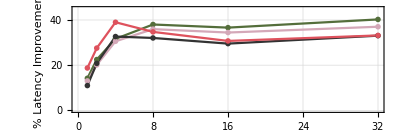

```mathematica
markers={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
colors={RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,45},
PlotMarkers->markers,
Joined->True,
PlotStyle->colors,
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[colors,Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0.3,LightGray],LegendMarkerSize->12,LegendLayout->{"Row",1}],{{0.2,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",10],None},{Style["Batch Size",10],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/fused_parallel_resnet50_v1_float16_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"fused_parallel_resnet50_v1_float16_latency_improvement.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"fused_parallel_resnet50_v1_float16_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

## ** Our Serial Recall for Half Precision + Fusion (ResNet50)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/resnet50_serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_fused_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfloat16data=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"float16_recall"->First[Lookup[ourfloat16data,toUniformModelName/@modelNames]],"recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100(Lookup[ds,"recall"]-Lookup[ds,"float16_recall"])/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{12.8635,20.481,25.9926,32.7011,34.0263,35.2998},{14.3139,17.9016,24.4854,31.3732,31.5634,31.9478},{9.24414,19.8095,27.4366,27.998,27.3453,28.4536},{18.5879,26.2961,34.6373,31.4873,28.7531,29.0158}}

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
Map[Transpose[{batchSizes,#}]&,edata]
```

{{{1,12.8635},{2,20.481},{4,25.9926},{8,32.7011},{16,34.0263},{32,35.2998}},{{1,14.3139},{2,17.9016},{4,24.4854},{8,31.3732},{16,31.5634},{32,31.9478}},{{1,9.24414},{2,19.8095},{4,27.4366},{8,27.998},{16,27.3453},{32,28.4536}},{{1,18.5879},{2,26.2961},{4,34.6373},{8,31.4873},{16,28.7531},{32,29.0158}}}

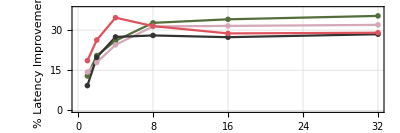

```mathematica
markers={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
colors={RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,38},
PlotMarkers->markers,
Joined->True,
PlotStyle->colors,
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[colors,Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0.3,LightGray],LegendMarkerSize->12,LegendLayout->{"Row",1}],{{0.2,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",10],None},{Style["Batch Size",10],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/fused_resnet50_v1_float16_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"fused_resnet50_v1_float16_latency_improvement.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"fused_resnet50_v1_float16_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

## ** >>> Our Serial Recall for Half Precision (ResNet50/PaddedNHCW)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
xmachines={"Tesla_V100-SXM2-16GB"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
files=ourfiles=Flatten@{
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/resnet50_serial_latency/"],
{modelName,modelNames}],
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}]
};
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
CopyToClipboard[ourraw];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;

files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_padded_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
fst=KeySort[First@Lookup[Select[Flatten[#],#["LayerName"]==="resnetv17_conv0_fwd"&],"RealTime(ms)"]&/@data];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfloat16data=data;


files=ourPaddedfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_nhwc_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
fstNHWC=KeySort[First@Lookup[Select[Flatten[#],#["LayerName"]==="resnetv17_conv0_fwd"&],"RealTime(ms)"]&/@data];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournhwcfloat16data=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"first"->First[Lookup[fst,toUniformModelName/@modelNames]],"first_nhwc"->First[Lookup[fstNHWC,toUniformModelName/@modelNames]],"float16_recall"->First[Lookup[ourfloat16data,toUniformModelName/@modelNames]],"float16_nhwc_recall"->First[Lookup[ournhwcfloat16data,toUniformModelName/@modelNames]],"recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
Table[
Table[
ds=mkFig[machine,batchSize];
{Lookup[ds,"recall"],Lookup[ds,"float16_recall"]-Lookup[ds,"first"],Lookup[ds,"float16_nhwc_recall"]-Lookup[ds,"first_nhwc"]},
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{{4.83194,5.75728,4.83436},{5.94424,6.07554,5.93645},{8.17165,6.90694,8.225},{13.2613,8.57532,12.791},{22.1835,14.1762,22.2711},{41.1215,25.9078,41.5576}},{{4.72563,5.35184,4.79064},{5.64206,5.58752,5.67327},{7.51384,6.31364,7.50339},{11.7164,7.57585,11.2261},{18.7676,12.0196,19.0739},{33.6248,21.4599,35.1084}},{{4.41751,5.6145,4.0115},{5.47649,5.91167,4.8765},{7.83089,6.66678,6.7472},{12.9614,8.44576,10.7887},{21.2005,14.4594,19.1111},{39.0928,26.9257,36.4941}},{{11.1256,17.1128,9.71707},{14.9076,18.0846,13.7035},{24.2248,20.6845,21.9208},{42.0522,26.0166,38.7018},{67.1377,42.2679,73.5217},{123.677,88.226,143.193}}}

```mathematica
Table[
Table[
ds=mkFig[machine,batchSize];
(Lookup[ds,"recall"]-Lookup[ds,"float16_nhwc_recall"]+Lookup[ds,"first_nhwc"]),
{batchSize,batchSizes[[-2;;]]}
],
{machine,machines[[-2;;]]}
]
```

{{1.68191,2.30374},{-7.42791,-22.1205}}

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100(Lookup[ds,"recall"]-Lookup[ds,"float16_nhwc_recall"]+Lookup[ds,"first_nhwc"])/(Lookup[ds,"mxnet"]-Lookup[ds,"first_nhwc"]),
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{-15.5953,-10.8763,-6.74331,2.4439,-1.552,-2.35814},{-14.6921,-10.2506,-5.12146,3.70414,-2.12618,-4.55202},{-6.92073,-1.08767,7.93223,12.4759,6.57031,5.19806},{-17.7904,-11.6188,0.494839,5.04547,-8.75548,-15.0967}}

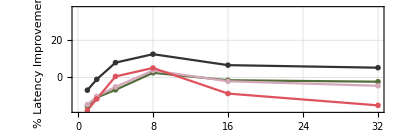

```mathematica
markers={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
colors={RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{All,37},
PlotMarkers->markers,
Joined->True,
PlotStyle->colors,
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[colors,Style[prettyName[#],Black,FontSize->16]&/@machines,LegendMarkers->markers,Background->Opacity[0.3,White],LegendMarkerSize->12,LegendLayout->{"Row",2}],{{0.4,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/resnet50_v1_nhwc_float16_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"resnet50_v1_nhwc_float16_latency_improvement.pdf",Magnify[ fig,1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"resnet50_v1_nhwc_float16_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

## ** Our Serial Recall for Half Precision (ResNet50/NHCW)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
files=ourfiles=Flatten@{
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/resnet50_serial_latency/"],
{modelName,modelNames}],
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}]
};
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
CopyToClipboard[ourraw];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;

files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfloat16data=data;


files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_nhwc_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournhwcfloat16data=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"float16_recall"->First[Lookup[ourfloat16data,toUniformModelName/@modelNames]],"float16_nhwc_recall"->First[Lookup[ournhwcfloat16data,toUniformModelName/@modelNames]],"recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
Table[
Table[
ds=mkFig[machine,batchSize];
{Lookup[ds,"recall"],Lookup[ds,"float16_recall"],Lookup[ds,"float16_nhwc_recall"]},
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{{4.83194,5.42866,4.16555},{5.94424,6.31725,4.59467},{8.17165,9.03619,5.9145},{13.2613,14.3983,8.46081},{22.1835,25.4725,13.9171},{41.1215,47.8059,24.9079}},{{4.72563,5.24576,4.27254},{5.64206,6.01638,4.60661},{7.51384,8.24611,5.58711},{11.7164,12.7177,7.58248},{18.7676,22.2118,11.9415},{33.6248,41.1712,21.0311}},{{4.41751,4.59666,3.95933},{5.47649,5.23665,4.3429},{7.83089,7.55963,5.69828},{12.9614,12.3332,8.66834},{21.2005,22.1858,14.2454},{39.0928,42.3178,26.4026}},{{11.1256,10.6646,8.86819},{14.9076,15.8143,10.6549},{24.2248,25.9737,14.9417},{42.0522,46.6755,23.921},{67.1377,89.4018,41.9557},{123.677,174.574,79.1355}}}

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100(Lookup[ds,"recall"]-Lookup[ds,"float16_nhwc_recall"])/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{13.8046,21.5722,25.8878,32.9803,33.8365,35.4021},{10.2776,18.9773,25.4551,33.1448,32.7134,32.4456},{10.3966,19.9913,26.3958,25.4884,26.0557,27.3001},{19.7538,26.4017,34.0871,30.9662,28.0763,28.5146}}

```mathematica
Map[Transpose[{batchSizes,#}]&,edata]
```

{{{1,13.8046},{2,21.5722},{4,25.8878},{8,32.9803},{16,33.8365},{32,35.4021}},{{1,10.2776},{2,18.9773},{4,25.4551},{8,33.1448},{16,32.7134},{32,32.4456}},{{1,10.3966},{2,19.9913},{4,26.3958},{8,25.4884},{16,26.0557},{32,27.3001}},{{1,19.7538},{2,26.4017},{4,34.0871},{8,30.9662},{16,28.0763},{32,28.5146}}}

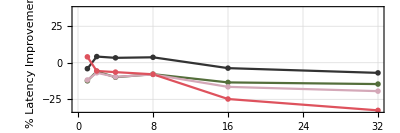

```mathematica
markers={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
colors={RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{All,37},
PlotMarkers->markers,
Joined->True,
PlotStyle->colors,
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[colors,Style[prettyName[#],Black,FontSize->16]&/@machines,LegendMarkers->markers,Background->Opacity[0.3,White],LegendMarkerSize->12,LegendLayout->{"Row",2}],{{0.4,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/resnet50_v1_nhwc_float16_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"resnet50_v1_nhwc_float16_latency_improvement.pdf",Magnify[ fig,1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"resnet50_v1_nhwc_float16_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

## ** Our Serial Recall for Half Precision (ResNet50)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32,64,128,256};
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
files=ourfiles=Flatten@{
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/resnet50_serial_latency/"],
{modelName,modelNames}],
Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}]
};
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
CopyToClipboard[ourraw];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;

files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfloat16data=data;


files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_nhwc_latency_float16/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournhwcfloat16data=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"float16_recall"->First[Lookup[ourfloat16data,toUniformModelName/@modelNames]],"float16_nhwc_recall"->First[Lookup[ournhwcfloat16data,toUniformModelName/@modelNames]],"recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
Table[
Table[
ds=mkFig[machine,batchSize];
{Lookup[ds,"recall"],Lookup[ds,"float16_recall"],Lookup[ds,"float16_nhwc_recall"]},
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{{4.83194,4.16555,5.42866},{5.94424,4.59467,6.31725},{8.17165,5.9145,9.03619},{13.2613,8.46081,14.3983},{22.1835,13.9171,25.4725},{41.1215,24.9079,47.8059},{77.5592,46.8967,92.709},{149.992,90.7556,182.676},{296.317,180.257,363.469}},{{4.72563,4.27254,5.33842},{5.64206,4.60661,6.11732},{7.51384,5.58711,8.35507},{11.7164,7.58248,12.8591},{18.7676,11.9415,22.078},{33.6248,21.0311,40.9498},{63.1683,38.9436,78.535},{121.35,73.2929,153.659},{236.541,143.641,303.696}},{{4.41751,3.95933,4.59666},{5.47649,4.3429,5.23665},{7.83089,5.69828,7.55963},{12.9614,8.66834,12.3332},{21.2005,14.2454,22.1858},{39.0928,26.4026,42.3178},{75.7772,50.9289,83.1585},{151.49,100.96,165.729},{306.002,202.368,332.718}},{{11.1256,8.86819,10.6646},{14.9076,10.6549,15.8143},{24.2248,14.9417,25.9737},{42.0522,23.921,46.6755},{67.1377,41.9557,89.4018},{123.677,79.1355,174.574},{Missing[KeyAbsent,resnet050_v1],153.099,344.424},{Missing[KeyAbsent,resnet050_v1],301.599,684.216},{Missing[KeyAbsent,resnet050_v1],599.698,1366.35}}}

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100(Lookup[ds,"recall"]-Lookup[ds,"float16_recall"](*Lookup[ds,"float16_nhwc_recall"]*))/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{13.8046,21.5722,25.8878,32.9803,33.8365,35.4021,3066.25/Missing[KeyAbsent,resnet050_v1],5923.61/Missing[KeyAbsent,resnet050_v1],11605.9/Missing[KeyAbsent,resnet050_v1]},{10.2776,18.9773,25.4551,33.1448,32.7134,32.4456,2422.46/Missing[KeyAbsent,resnet050_v1],4805.73/Missing[KeyAbsent,resnet050_v1],9289.99/Missing[KeyAbsent,resnet050_v1]},{10.3966,19.9913,26.3958,25.4884,26.0557,27.3001,2484.83/Missing[KeyAbsent,resnet050_v1],5053.07/Missing[KeyAbsent,resnet050_v1],10363.4/Missing[KeyAbsent,resnet050_v1]},{19.7538,26.4017,34.0871,30.9662,28.0763,28.5146,(100 (-153.099+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1],(100 (-301.599+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1],(100 (-599.698+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1]}}

```mathematica
Map[Transpose[{batchSizes,#}]&,edata]
```

{{{1,13.8046},{2,21.5722},{4,25.8878},{8,32.9803},{16,33.8365},{32,35.4021},{64,3066.25/Missing[KeyAbsent,resnet050_v1]},{128,5923.61/Missing[KeyAbsent,resnet050_v1]},{256,11605.9/Missing[KeyAbsent,resnet050_v1]}},{{1,10.2776},{2,18.9773},{4,25.4821},{8,32.7131},{16,32.7766},{32,32.4679},{64,2422.46/Missing[KeyAbsent,resnet050_v1]},{128,4805.73/Missing[KeyAbsent,resnet050_v1]},{256,9289.99/Missing[KeyAbsent,resnet050_v1]}},{{1,10.5089},{2,20.4379},{4,26.4021},{8,25.4911},{16,26.0336},{32,27.2793},{64,2484.83/Missing[KeyAbsent,resnet050_v1]},{128,5053.07/Missing[KeyAbsent,resnet050_v1]},{256,10363.4/Missing[KeyAbsent,resnet050_v1]}},{{1,19.7538},{2,26.4017},{4,34.0871},{8,30.9662},{16,28.0763},{32,28.5146},{64,(100 (-153.099+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1]},{128,(100 (-301.599+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1]},{256,(100 (-599.698+Missing[KeyAbsent,resnet050_v1]))/Missing[KeyAbsent,resnet050_v1]}}}

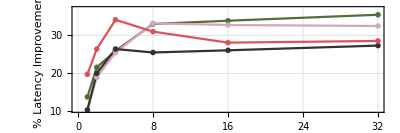

```mathematica
markers={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
colors={RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{All,37},
PlotMarkers->markers,
Joined->True,
PlotStyle->colors,
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[colors,Style[prettyName[#],Black,FontSize->16]&/@machines,LegendMarkers->markers,Background->Opacity[0.3,White],LegendMarkerSize->12,LegendLayout->{"Row",2}],{{0.4,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/resnet50_v1_float16_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"resnet50_v1_float16_latency_improvement.pdf",Magnify[ fig,1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"resnet50_v1_float16_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

## ** ResNet50 (batchsize 1 -> 1024)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32,64,128,256,512,1024};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];

files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;


<|"machine"->machineName,"batchsize"->batchSize0,"recall"->First[Lookup[ourdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
Lookup[ds,"recall"],
{batchSize,batchSizes}
],
{machine,machines}
];(*edata=Map[#/First[#]&,edata];*)
```

```mathematica
edata
```

{{22.0954,32.1351,51.6276,89.0934,143.992,290.448,202.66,303.246,1521.63,4054.19,3749.91},{16.4389,22.8435,37.9876,68.1586,122.716,239.354,200.589,318.195,1263.32,3514.73,3437.3},{5.60159,7.39286,10.7128,17.6628,29.793,57.9417,45.6889,73.4128,149.138,360.367,840.299},{4.63925,5.71889,8.18297,13.3317,21.5719,41.0247,36.2142,57.1552,111.748,253.87,601.687},{4.57603,5.42476,7.54196,11.6923,18.3468,33.6826,26.5539,40.1767,85.0479,196.252,451.842},{4.25521,5.21374,7.80527,12.9763,20.5743,38.9648,34.0285,55.8804,117.952,273.767,611.214},{10.6114,14.3208,24.2475,42.0549,65.5254,123.677,Missing[KeyAbsent,resnet050_v1],Missing[KeyAbsent,resnet050_v1],Missing[KeyAbsent,resnet050_v1],Missing[KeyAbsent,resnet050_v1],Missing[KeyAbsent,resnet050_v1]}}

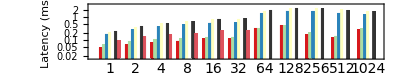

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=BarChart[
(batchSizes/Transpose[edata]),
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
ScalingFunctions->"Log",
FrameLabel->{{Style["Latency (ms)",14],None},{None(*Style["Batch Size",14]*),None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
(*fig=Magnify[fig,1.2]*)
fig
```

## ** Our Batched Serial Fused Recall for website (ResNet50)

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/resnet50_serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ournonfuseddata=data;
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/fused_serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourfuseddata=data;

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"fused_recall"->First[Lookup[ourfuseddata,toUniformModelName/@modelNames]],"non_fused_recall"->First[Lookup[ournonfuseddata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100*(Lookup[ds,"non_fused_recall"]-Lookup[ds,"fused_recall"])/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{2.18474,1.71622,1.45149,1.35701,1.72097,1.60975},{4.81671,4.7063,4.14829,4.23101,4.29106,4.42082},{4.56571,6.10118,7.42504,7.67963,8.24866,8.4343},{5.03831,5.09322,4.8954,4.53696,4.47516,4.36866},{7.25278,6.52843,6.02283,5.19062,4.98206,4.68839},{5.54845,5.52892,5.49622,3.83715,4.28381,4.53501},{4.21672,4.91309,4.47406,3.68293,4.45893,4.91223}}

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
machines
```

{Tesla_K80,Tesla_M60,TITAN_Xp,TITAN_V,Tesla_V100-SXM2-16GB,Quadro_RTX_6000,Tesla_T4}

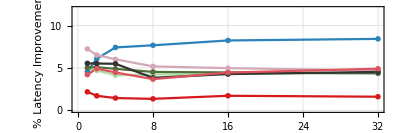

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,12},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->8,LegendLayout->{"Row",2}],{{0.005,0.69},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/resnet50_v1_fused_latency_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"resnet50_v1_fused_latency_improvement.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"resnet50_v1_fused_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

```mathematica
SystemOpen[targetDir]
```

## Speedup of MXNet on all systems using padding fix2 (geomean)

```mathematica
modelNames={"ResNet050-v1"};
modelNames={"ArcFace","BVLC_AlexNet",(*"BVLC_CaffeNet",*)(*"BVLC_GoogleNet",*)(*"BVLC_RCNN_ILSVRC13",*)"DenseNet-121","DUC",(*"Emotion-FerPlus",*)(*"Inception-v1",*)(*"Inception-v2",*)(*"MNIST",*)"MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1",(*"Tiny_YOLO-v2",*)"VGG16-BN","VGG16","VGG19-BN","VGG19"(*,"Zfnet512"*)};
batchSizes={1,2,4,8,16,32};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;


files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet_fix/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetfixraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetfixdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"fix"->Lookup[mxnetfixdata,toUniformModelName/@modelNames],"mxnet"->Lookup[mxnetdata,toUniformModelName/@modelNames]|>
]
```

```mathematica
mkFig["Tesla_M60",16]
```

<|machine→Tesla_M60,batchsize→16,fix→{205.204,14.2431,258.533,19195.9,435.655,44.8608,47.7513,75.6428,78.4904,136.574,135.086,232.319,224.393,338.161,321.976,104.718,27.0432,234.269,200.694,270.94,233.922},mxnet→{230.654,14.2133,283.422,20268.4,442.542,45.3797,48.2675,76.3695,79.2319,155.889,154.626,262.128,254.25,380.666,364.577,104.297,30.2696,234.206,200.95,271.341,234.266}|>

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100*GeometricMean[Map[If[#<=0,0.01,#]&,(Lookup[ds,"fix"]-Lookup[ds,"mxnet"])/Lookup[ds,"mxnet"]]],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{0.647195,0.436462,0.55272,0.690186,0.728209,0.767951},{1.12039,0.921812,0.907931,0.735489,0.748569,0.848362},{1.11066,1.04505,0.883754,0.829388,0.973683,0.887358},{0.704601,0.911709,0.84512,0.810535,0.910299,0.848849},{0.873032,0.826631,0.55904,0.990173,0.747488,0.71092},{0.932185,0.6288,0.784403,0.856645,0.663616,0.750664},{0.722502,0.531931,0.506583,0.471007,0.801375,0.507394}}

## ** Speedup of MXNet on all systems using padding fix

```mathematica
modelNames={"ResNet050-v1"};
batchSizes={1,2,4,8,16,32};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];

files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;


files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet_fix/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetfixraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetfixdata=data;

<|"machine"->machineName,"batchsize"->batchSize0,"fix"->First[Lookup[mxnetfixdata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
edata=Table[
Table[
ds=mkFig[machine,batchSize];
100*(Lookup[ds,"mxnet"]-Lookup[ds,"fix"])/Lookup[ds,"mxnet"],
{batchSize,batchSizes}
],
{machine,machines}
]
```

{{5.83332,6.56277,8.58936,10.2885,12.3201,12.465},{6.8648,9.71017,10.6139,11.1094,12.3906,13.2174},{3.51251,4.35257,4.8202,9.55273,8.98794,11.0411},{1.46275,3.90921,6.89016,8.0596,7.45961,9.05773},{3.94467,5.5177,6.81235,7.91532,8.26333,7.79337},{4.66015,7.35739,7.28476,7.1614,8.92851,9.61897},{5.482,6.71954,7.69103,7.03367,8.97007,10.0019}}

```mathematica
machines
```

{Tesla_K80,Tesla_M60,TITAN_Xp,TITAN_V,Tesla_V100-SXM2-16GB,Quadro_RTX_6000,Tesla_T4}

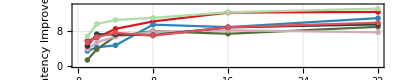

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,14},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->10]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.3,0.01},{0,0}}] ,
AspectRatio->1/5,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",8],None},{Style["Batch Size",8],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_fix_improvement/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"mxnet_fix_improvement.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"mxnet_fix_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

```mathematica
SystemOpen[targetDir]
```

## ** Latency of MXNet on V100

```mathematica
mkData[system_,model_]:=
Module[{},
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>system];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batch_size","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[SortBy[KeyDrop[#,"times"],#["id"]&]&/@data];
data=SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[model]||ToLowerCase[#["name"]]===ToLowerCase[StringReplace[model,"-"->"_"]]&]["mean_time"]&/@data;
data=Map[If[#<0.1,1000*#,#]&,data];
KeyMap[ToString,data];
data
]
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_V100-SXM2-16GB"};
```

```mathematica
es=Table[
xPrint[machine];
model->mkData["Tesla_V100-SXM2-16GB",model][1],
{model,modelNames}
];
```

```mathematica
es
```

{ArcFace→9.85154,BVLC_AlexNet→1.07028,BVLC_CaffeNet→1.02534,BVLC_GoogleNet→4.04509,BVLC_RCNN_ILSVRC13→0.995898,DenseNet-121→9.26619,DUC→143.404,Emotion-FerPlus→1.02981,Inception-v1→3.98136,Inception-v2→5.73506,MNIST→0.327738,MobileNet-v2→2.26222,ResNet018-v1→1.88232,ResNet018-v2→1.92048,ResNet034-v1→3.24992,ResNet034-v2→3.34962,ResNet050-v1→4.40854,ResNet050-v2→4.62979,ResNet101-v1→8.41914,ResNet101-v2→8.43763,ResNet152-v1→12.2128,ResNet152-v2→12.0931,Shufflenet→2.95372,Squeezenet-v1.1→1.30866,Tiny_YOLO-v2→1.78134,VGG16-BN→3.94402,VGG16→3.52074,VGG19-BN→4.63564,VGG19→4.2033,Zfnet512→1.47045}

```mathematica
ExportString[KeyMap[ToString,#]&/@es,"JSON"]//CopyToClipboard
```

Export::jsonassockeynstr: Association contains non string key.

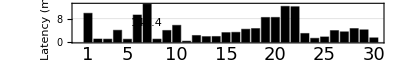

```mathematica
fig=BarChart[
Table[
If[e>13,
Callout[13,Rotate[Style[Round[e,0.1],White,FontSize->16],90Degree],Center,Automatic,Appearance->None,CalloutMarker->"Arrow",LabelStyle->Directive[White,Bold],Background->White,FrameMargins->7],
e
],
{e,Lookup[es,modelNames]}
],
PlotTheme->"Grid",
AspectRatio->1/6,
Frame->True,
ChartStyle->{Black},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["",14],None}},
ImageSize->Scaled[0.75],
ChartLabels->Placed[Style[If[Mod[#,5]==0||#==1,#,""],Black,FontSize->18]&/@Range[30],Below],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->{All,{0,13}},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency_v100/figures/";
Quiet[CreateDirectory["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency_v100/figures/"]];
PrintTemporary[targetDir<>"mxnet_latency_v100.pdf"];
json=Export[targetDir<>"mxnet_latency_v100.json",es,"JSON"];
pdf=Export[targetDir<>"mxnet_latency_v100.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>"mxnet_latency_v100.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
fig
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
```

## ** Latency of MXNet across systems

```mathematica
mkData[system_,model_]:=
Module[{},
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>system];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batch_size","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[SortBy[KeyDrop[#,"times"],#["id"]&]&/@data];
data=SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[model]||ToLowerCase[#["name"]]===ToLowerCase[StringReplace[model,"-"->"_"]]&]["mean_time"]&/@data;
data=Map[If[#<0.1,1000*#,#]&,data];
KeyMap[ToString,data];
data
]
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
es=Table[
xPrint[machine];
model->(machine->mkData[machine,model]),
{model,modelNames},
{machine,machines}
];
es=Merge[es,Association];
```

```mathematica
ExportString[KeyMap[ToString,#]&/@es,"JSON"]//CopyToClipboard
```

Export::jsonassockeynstr: Association contains non string key.

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
Do[
data=Lookup[es,modelName];
fig=BarChart[
Transpose[Values[Lookup[Lookup[es,modelName],machines]]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*"MXNet Latency for "<>modelName<>" Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->16]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->12]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
lfig=BarChart[
Transpose[Values[Lookup[Lookup[es,modelName],machines]]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
ScalingFunctions->"Log",
FrameLabel->{{Style["Latency (ms)",16],None},{Style["Batch Size",14],None(*"MXNet Latency for "<>modelName<>" Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->16]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->20]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.01,0.7},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
PrintTemporary["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency.pdf"];
json=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency.json",Map[KeyMap[ToString,#]&,data],"JSON"];
pdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
lpdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency_log_scaled.pdf",lfig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
lpng=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"<>modelName<>"_latency_log_scaled.png",lfig,"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
modelName-><|"png"->png,"json"->json,"pdf"->pdf|>,
{modelName,modelNames}
];
```

Export::jsonstrictencoding: Expression If cannot be exported as JSON.

General::stop: Further output of Export::jsonstrictencoding will be suppressed during this calculation.

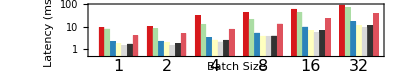

```mathematica
lfig
```

```mathematica
SystemOpen["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/mxnet_latency/figures/"]
```

### Make All URLs

```mathematica
ClearAll[mkURL];
mkPDFUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency.pdf\""
mkPNGUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency.png\""
mkJSONUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency.json\""
mkPDFLogUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency_log_scaled.pdf\""
mkPNGLogUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency_log_scaled.png\""
mkJSONLogUrl[model_]:="\"/assets/mxnet_latency/figures/"<>model<>"_latency_log_scaled.json\""
mkId[base_]:=ToString[Hash[base]]
modelToMarkdown[model_?StringQ]:="## **"<>StringReplace[model,"_"->" "] <> "** Model\n\n"<>
"{{< tabs \""<>mkId[model]<>"\" >}}\n"<>
"{{< tab \"Linear\" >}}\n"<>
"\n{{< lightbox src="<>mkPNGUrl[model]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkPDFUrl[model]<>">}}PDF{{< /button >}}\n{{< button href="<>mkJSONUrl[model]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n"<>
"{{< tab \"Log\" >}}\n"<>
"\n\n{{< lightbox src="<>mkPNGLogUrl[model]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkPDFLogUrl[model]<>">}}PDF{{< /button >}}\n{{< button href="<>mkJSONLogUrl[model]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n{{< /tabs >}}\n\n"
modelToMarkdown[lst_?ListQ]:=StringRiffle[modelToMarkdown /@ lst,"\n\n\n"]
```

```mathematica
CopyToClipboard[modelToMarkdown[modelNames]]
```

## ** Caffe2 vs Caffe2 Opt (batchsize=1)

#### Make Plot

```mathematica
getData[framework_,modelName_]:=
Module[{},
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/"<>framework<>"/Tesla_V100-SXM2-16GB/batchsize_1.csv";
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=addHeader[Import[file]];
mxnetdata=SelectFirst[data,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[StringReplace[#["name"],"-"->"_"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&];
If[MissingQ[mxnetdata],Return[modelName->mxnetdata]];
mxnetdata=mxnetdata["mean_time"];
mxnetdata=Map[If[#<0.1,1000*#,#]&,mxnetdata];
modelName->mxnetdata
];
getCaffe2Data[modelName_]:=getData["caffe2",modelName];
getCaffe2OptData[modelName_]:=getData["caffe2_opt",modelName];
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
availableModels={"BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","Inception-v1","Inception-v2","MobileNet-v2","ResNet018-v2","ResNet034-v2","ResNet050-v2","ResNet101-v2","ResNet152-v2","Shufflenet","Squeezenet-v1.1","VGG16","VGG19","Zfnet512"};
getModelIndex[x_]:=First[FirstPosition[modelNames,x]]
```

```mathematica
caffe2Info=DeleteMissing[getCaffe2Data/@modelNames];
caffe2OptInfo=DeleteMissing[getCaffe2OptData/@modelNames];
```

```mathematica
Lookup[caffe2Info,availableModels]
```

{1.94585,1.95341,6.48236,2.13054,18.4372,6.62248,10.2201,4.73766,3.32115,5.50817,7.58483,13.997,20.2476,7.79246,2.55176,4.59282,5.42103,2.35593}

```mathematica
Lookup[caffe2OptInfo,availableModels]
```

{1.19532,1.18512,4.73263,1.16633,8.0635,4.77781,6.08137,2.04769,2.10113,3.23073,4.5807,8.17324,11.3722,6.40826,2.25588,3.38085,3.98209,1.66864}

```mathematica
(Lookup[caffe2Info,availableModels]/Lookup[caffe2OptInfo,availableModels])
```

{1.62789,1.64829,1.36972,1.82671,2.2865,1.38609,1.68056,2.31366,1.58065,1.70493,1.65582,1.71254,1.78045,1.216,1.13116,1.35848,1.36135,1.41189}

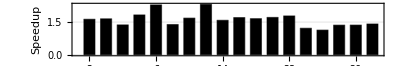

```mathematica
fig=BarChart[
(Lookup[caffe2Info,availableModels]/Lookup[caffe2OptInfo,availableModels]),
ChartStyle->{Black},
PlotTheme->"Grid",
(*ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->10]&/@{""},Background->Opacity[0.5,White],LegendMarkerSize->8,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],*)
ChartLabels->(Style[#,Black]&/@(getModelIndex/@availableModels)),
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/6,
Frame->True,
FrameLabel->{{Style["Speedup",16],None},{Style["Model Index",16],None}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->12},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->12}
]
```

```mathematica
data=<|"caffe2"->caffe2Info,"caffe2_opt"->caffe2OptInfo|>;
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/caffe2_opt/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"caffe2_opt.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"caffe2_opt.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pngNorm=Export[targetDir<>"data.json",Map[Which[AssociationQ[#],KeyMap[ToString,#],MissingQ[#],"Nothing",MatchQ[#,_If],"Nothing",True,#]&,data,Infinity],"JSON"];
```

```mathematica
getCaffe2Data/@modelNames
```

{ArcFace→Missing[NotFound],BVLC_AlexNet→1.94585,BVLC_CaffeNet→1.95341,BVLC_GoogleNet→6.48236,BVLC_RCNN_ILSVRC13→2.13054,DenseNet-121→18.4372,DUC→Missing[NotFound],Emotion-FerPlus→Missing[NotFound],Inception-v1→6.62248,Inception-v2→10.2201,MNIST→0.705234,MobileNet-v2→4.73766,ResNet018-v1→Missing[NotFound],ResNet018-v2→3.32115,ResNet034-v1→Missing[NotFound],ResNet034-v2→5.50817,ResNet050-v1→Missing[NotFound],ResNet050-v2→7.58483,ResNet101-v1→Missing[NotFound],ResNet101-v2→13.997,ResNet152-v1→Missing[NotFound],ResNet152-v2→20.2476,Shufflenet→7.79246,Squeezenet-v1.1→2.55176,Tiny_YOLO-v2→2.76872,VGG16-BN→Missing[NotFound],VGG16→4.59282,VGG19-BN→Missing[NotFound],VGG19→5.42103,Zfnet512→2.35593}

```mathematica
SystemOpen[targetDir]
```

#### Cleanup Caffe2 path

```mathematica
modelIds=Range[30];
validLineQ[line_]:=Apply[Or,Table[StringStartsQ[line,ToString[modelId]<>","],{modelId,modelIds}]]
```

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2/Tesla_V100-SXM2-16GB/batchsize_1.csv";
data=Import[file,"Text"];
newdata=StringRiffle[Select[StringSplit[data,"\n"],validLineQ],"\n"];
Export[file,newdata,"Text"]
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2/Tesla_V100-SXM2-16GB/batchsize_1.csv

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2_opt/Tesla_V100-SXM2-16GB/batchsize_1.csv";
data=Import[file,"Text"];
newdata=StringRiffle[Select[StringSplit[data,"\n"],validLineQ],"\n"];
Export[file,newdata,"Text"]
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2_opt/Tesla_V100-SXM2-16GB/batchsize_1.csv

## ** MXNet vs ONNXRT vs Caffe2 (batchsize=1)

#### Make Plot

```mathematica
getData[framework_,modelName_]:=
Module[{},
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/"<>framework<>"/Tesla_V100-SXM2-16GB/batchsize_1.csv";
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=addHeader[Import[file]];
mxnetdata=SelectFirst[data,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[StringReplace[#["name"],"-"->"_"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&];
If[MissingQ[mxnetdata],Return[modelName->mxnetdata]];
mxnetdata=mxnetdata["mean_time"];
mxnetdata=Map[If[#<0.1,1000*#,#]&,mxnetdata];
modelName->mxnetdata
];
getMXNetData[modelName_]:=getData["mxnet",modelName];
getONNXData[modelName_]:=getData["onnxruntime",modelName];
getCaffe2Data[modelName_]:=getData["caffe2",modelName];
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
```

```mathematica
mxnetInfo=getMXNetData/@modelNames;
onnxInfo=getONNXData/@modelNames;
caffe2Info=getCaffe2Data/@modelNames;
```

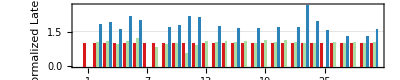

```mathematica
fig=BarChart[
Transpose[{Values[mxnetInfo],Values[onnxInfo],Values[caffe2Info]}]/Values[mxnetInfo],
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
PlotTheme->"Grid",
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->10]&/@{"MXNet","ONNXRuntime","PyTorch"},Background->Opacity[0.5,White],LegendMarkerSize->8,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Range[Length[modelNames]]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",10],None},{Style["Model Index",10],None}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->8}
]
```

```mathematica
data=<|"mxnet"->mxnetInfo,"onnxruntime"->onnxInfo,"caffe2"->caffe2Info|>;
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/framework_compare/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"framework_compare.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"framework_compare.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pngNorm=Export[targetDir<>"data.json",Map[Which[AssociationQ[#],KeyMap[ToString,#],MissingQ[#],"Nothing",MatchQ[#,_If],"Nothing",True,#]&,data,Infinity],"JSON"];
```

```mathematica
getCaffe2Data/@modelNames
```

{ArcFace→Missing[NotFound],BVLC_AlexNet→1.94585,BVLC_CaffeNet→1.95341,BVLC_GoogleNet→6.48236,BVLC_RCNN_ILSVRC13→2.13054,DenseNet-121→18.4372,DUC→Missing[NotFound],Emotion-FerPlus→Missing[NotFound],Inception-v1→6.62248,Inception-v2→10.2201,MNIST→0.705234,MobileNet-v2→4.73766,ResNet018-v1→Missing[NotFound],ResNet018-v2→3.32115,ResNet034-v1→Missing[NotFound],ResNet034-v2→5.50817,ResNet050-v1→Missing[NotFound],ResNet050-v2→7.58483,ResNet101-v1→Missing[NotFound],ResNet101-v2→13.997,ResNet152-v1→Missing[NotFound],ResNet152-v2→20.2476,Shufflenet→7.79246,Squeezenet-v1.1→2.55176,Tiny_YOLO-v2→2.76872,VGG16-BN→Missing[NotFound],VGG16→4.59282,VGG19-BN→Missing[NotFound],VGG19→5.42103,Zfnet512→2.35593}

#### Cleanup Caffe2 path

```mathematica
modelIds=Range[30];
validLineQ[line_]:=Apply[Or,Table[StringStartsQ[line,ToString[modelId]<>","],{modelId,modelIds}]]
```

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2/Tesla_V100-SXM2-16GB/batchsize_1.csv";
data=Import[file,"Text"];
newdata=StringRiffle[Select[StringSplit[data,"\n"],validLineQ],"\n"];
Export[file,newdata,"Text"]
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/caffe2/Tesla_V100-SXM2-16GB/batchsize_1.csv

## **Does models have improvement by selecting better cudnn heuristics for all models (geomean)

```mathematica
mkFig[machine_,modelName_]:=Module[{},
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/"<>machine<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency"];
cudnnfiles=FileNames["batchsize_*/"<>machine<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/cudnn_advised_serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,cudnnfiles}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
cudnndata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machine];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[StringReplace[#["name"],"-"->"_"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&]["mean_time"]&,data];
mxnetdata=Map[If[#<0.1,1000*#,#]&,mxnetdata];
(*fig=BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[cudnndata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
PlotTheme->"Grid",
ChartLegends->{"Recall","CUDNN Heuristic","MXNet"},
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],modelName<>" Time for Recall, CUDNN Heuristic, and MXNet"}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
(Lookup[cudnndata,batchSizes]-Lookup[ourdata,batchSizes])/Lookup[mxnetdata,batchSizes],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Keys[data]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Speedup",14],None},{Style["Batch Size",14],modelName<>" Impact of Heuristics on End-to-End Time"}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];*)
<|
(*"regular"->fig,
"normalized"->nfig,*)
"data"-><|"recall"->ourdata,"cudnn_heuristics"->cudnndata,"mxnet"->mxnetdata,"machine"->machine|>
|>
]
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};modelName="ResNet050-v1";
alldata=Association@Table[
machine->Association@Table[
es=mkFig[machine,modelName]["data"];
modelName->es,
{modelName,modelNames}
]
,
{machine,machines}
];
```

```mathematica
mdata=Table[
 Table[
es=alldata[machine][modelName];
Which[
!NumberQ[Lookup[es["mxnet"],batchsize]],
Nothing,
Lookup[es["cudnn_heuristics"],batchsize]-Lookup[es["recall"],batchsize]==0,
{modelName,machine,Lookup[es["cudnn_heuristics"],batchsize]-Lookup[es["recall"],batchsize],Lookup[es["mxnet"],batchsize],(Lookup[es["cudnn_heuristics"],batchsize]-Lookup[es["recall"],batchsize])/Lookup[es["mxnet"],batchsize]},
True,
{modelName,machine,batchsize,(Lookup[es["cudnn_heuristics"],batchsize]-Lookup[es["recall"],batchsize])/Lookup[es["mxnet"],batchsize]}
],
{modelName,modelNames}
],
{machine,machines[[-1;;]]},
{batchsize,batchSizes}
];
```

```mathematica
mdata
```

{{{{ArcFace,Tesla_T4,1,0.0105858},{BVLC_AlexNet,Tesla_T4,1,0.0390289},{BVLC_CaffeNet,Tesla_T4,1,0.0503725},{BVLC_GoogleNet,Tesla_T4,1,0.0578677},{BVLC_RCNN_ILSVRC13,Tesla_T4,1,0.0516883},{DenseNet-121,Tesla_T4,1,0.0204369},{DUC,Tesla_T4,1,0.000314258},{Emotion-FerPlus,Tesla_T4,1,0.3786},{Inception-v1,Tesla_T4,1,0.057705},{Inception-v2,Tesla_T4,0.,11.0397,0.},{MNIST,Tesla_T4,1,0.0610701},{MobileNet-v2,Tesla_T4,1,0.0113323},{ResNet018-v1,Tesla_T4,1,0.0300706},{ResNet018-v2,Tesla_T4,1,0.0291376},{ResNet034-v1,Tesla_T4,1,0.017042},{ResNet034-v2,Tesla_T4,1,0.0167298},{ResNet050-v1,Tesla_T4,1,0.0254633},{ResNet050-v2,Tesla_T4,1,0.0395372},{ResNet101-v1,Tesla_T4,1,0.0415558},{ResNet101-v2,Tesla_T4,1,0.0492488},{ResNet152-v1,Tesla_T4,1,0.0433269},{ResNet152-v2,Tesla_T4,1,0.0492257},{Shufflenet,Tesla_T4,1,0.0804315},{Squeezenet-v1.1,Tesla_T4,1,0.0424395},{Tiny_YOLO-v2,Tesla_T4,1,0.00139304},{VGG16-BN,Tesla_T4,0.,15.5348,0.},{VGG16,Tesla_T4,0.,14.4862,0.},{VGG19-BN,Tesla_T4,0.,18.8394,0.},{VGG19,Tesla_T4,0.,17.6374,0.},{Zfnet512,Tesla_T4,0.,4.01738,0.}},{{ArcFace,Tesla_T4,2,0.0175739},{BVLC_AlexNet,Tesla_T4,0.,2.80857,0.},{BVLC_CaffeNet,Tesla_T4,0.,3.29733,0.},{BVLC_GoogleNet,Tesla_T4,2,0.0702776},{BVLC_RCNN_ILSVRC13,Tesla_T4,0.,3.19839,0.},{DenseNet-121,Tesla_T4,2,0.030597},{DUC,Tesla_T4,2,0.000167594},{Inception-v1,Tesla_T4,2,0.069841},{MNIST,Tesla_T4,2,0.0604717},{MobileNet-v2,Tesla_T4,2,0.0354249},{ResNet018-v1,Tesla_T4,2,0.014137},{ResNet018-v2,Tesla_T4,2,0.0135126},{ResNet034-v1,Tesla_T4,2,0.00815209},{ResNet034-v2,Tesla_T4,2,0.00791286},{ResNet050-v1,Tesla_T4,2,0.00843354},{ResNet050-v2,Tesla_T4,2,0.0282904},{ResNet101-v1,Tesla_T4,2,0.00463978},{ResNet101-v2,Tesla_T4,2,0.0163468},{ResNet152-v1,Tesla_T4,2,0.00687829},{ResNet152-v2,Tesla_T4,2,0.0151228},{Shufflenet,Tesla_T4,2,0.0636537},{Squeezenet-v1.1,Tesla_T4,2,0.0137841},{Tiny_YOLO-v2,Tesla_T4,2,0.163519},{VGG16-BN,Tesla_T4,0.,27.1786,0.},{VGG16,Tesla_T4,0.,25.2757,0.},{VGG19-BN,Tesla_T4,0.,33.0461,0.},{VGG19,Tesla_T4,0.,30.9441,0.},{Zfnet512,Tesla_T4,0.,4.92668,0.}},{{ArcFace,Tesla_T4,4,0.0142412},{BVLC_AlexNet,Tesla_T4,4,0.00889975},{BVLC_CaffeNet,Tesla_T4,4,0.00780924},{BVLC_GoogleNet,Tesla_T4,4,0.0549493},{BVLC_RCNN_ILSVRC13,Tesla_T4,4,0.00802827},{DenseNet-121,Tesla_T4,4,0.0118739},{DUC,Tesla_T4,4,0.0000754724},{Inception-v1,Tesla_T4,4,0.0601543},{MNIST,Tesla_T4,4,0.199856},{MobileNet-v2,Tesla_T4,4,0.0249765},{ResNet018-v1,Tesla_T4,4,0.0218699},{ResNet018-v2,Tesla_T4,4,0.0206819},{ResNet034-v1,Tesla_T4,4,0.0123107},{ResNet034-v2,Tesla_T4,4,0.0119458},{ResNet050-v1,Tesla_T4,4,0.0173078},{ResNet050-v2,Tesla_T4,4,0.0305346},{ResNet101-v1,Tesla_T4,4,0.0386052},{ResNet101-v2,Tesla_T4,4,0.0463559},{ResNet152-v1,Tesla_T4,4,0.0416172},{ResNet152-v2,Tesla_T4,4,0.047664},{Shufflenet,Tesla_T4,4,0.0434887},{Squeezenet-v1.1,Tesla_T4,4,0.035284},{Tiny_YOLO-v2,Tesla_T4,4,0.117869},{VGG16-BN,Tesla_T4,0.,50.1082,0.},{VGG16,Tesla_T4,0.,46.5675,0.},{VGG19-BN,Tesla_T4,0.,61.021,0.},{VGG19,Tesla_T4,0.,57.0707,0.},{Zfnet512,Tesla_T4,4,0.0667126}},{{ArcFace,Tesla_T4,8,0.0223712},{BVLC_AlexNet,Tesla_T4,8,0.0932709},{BVLC_CaffeNet,Tesla_T4,8,0.0746571},{BVLC_GoogleNet,Tesla_T4,8,0.043692},{BVLC_RCNN_ILSVRC13,Tesla_T4,8,0.0760999},{DenseNet-121,Tesla_T4,8,0.0326566},{DUC,Tesla_T4,8,0.00367296},{Inception-v1,Tesla_T4,8,0.0402108},{MNIST,Tesla_T4,8,0.601406},{MobileNet-v2,Tesla_T4,8,0.00116906},{ResNet018-v1,Tesla_T4,8,0.0410225},{ResNet018-v2,Tesla_T4,8,0.0391077},{ResNet034-v1,Tesla_T4,8,0.0336638},{ResNet034-v2,Tesla_T4,8,0.0328782},{ResNet050-v1,Tesla_T4,8,0.0285933},{ResNet050-v2,Tesla_T4,8,0.0308493},{ResNet101-v1,Tesla_T4,8,0.0195627},{ResNet101-v2,Tesla_T4,8,0.0208975},{ResNet152-v1,Tesla_T4,8,0.0160901},{ResNet152-v2,Tesla_T4,8,0.0170716},{Shufflenet,Tesla_T4,8,0.0279895},{Squeezenet-v1.1,Tesla_T4,8,0.0234297},{Tiny_YOLO-v2,Tesla_T4,8,0.317453},{VGG16-BN,Tesla_T4,8,0.0726967},{VGG16,Tesla_T4,8,0.0788124},{VGG19-BN,Tesla_T4,8,0.0853944},{VGG19,Tesla_T4,8,0.0919581},{Zfnet512,Tesla_T4,8,0.0647364}},{{ArcFace,Tesla_T4,16,0.269224},{BVLC_AlexNet,Tesla_T4,16,0.356678},{BVLC_CaffeNet,Tesla_T4,16,0.353776},{BVLC_GoogleNet,Tesla_T4,16,0.191614},{BVLC_RCNN_ILSVRC13,Tesla_T4,16,0.357914},{DenseNet-121,Tesla_T4,16,0.0113086},{DUC,Tesla_T4,16,0.0227643},{Inception-v1,Tesla_T4,16,0.215338},{MNIST,Tesla_T4,16,0.618386},{MobileNet-v2,Tesla_T4,16,0.00031711},{ResNet018-v1,Tesla_T4,16,0.183806},{ResNet018-v2,Tesla_T4,16,0.173952},{ResNet034-v1,Tesla_T4,16,0.23207},{ResNet034-v2,Tesla_T4,16,0.224795},{ResNet050-v1,Tesla_T4,16,0.100887},{ResNet050-v2,Tesla_T4,16,0.11745},{ResNet101-v1,Tesla_T4,16,0.104575},{ResNet101-v2,Tesla_T4,16,0.115497},{ResNet152-v1,Tesla_T4,16,0.106394},{ResNet152-v2,Tesla_T4,16,0.115611},{Shufflenet,Tesla_T4,16,0.0164614},{Squeezenet-v1.1,Tesla_T4,16,0.0724367},{Tiny_YOLO-v2,Tesla_T4,16,0.340576},{VGG16-BN,Tesla_T4,16,0.515587},{VGG16,Tesla_T4,16,0.579359},{VGG19-BN,Tesla_T4,16,0.582866},{VGG19,Tesla_T4,16,0.650154},{Zfnet512,Tesla_T4,16,0.35662}},{{ArcFace,Tesla_T4,32,0.414278},{BVLC_AlexNet,Tesla_T4,32,0.3962},{BVLC_CaffeNet,Tesla_T4,32,0.334938},{BVLC_GoogleNet,Tesla_T4,32,0.161217},{BVLC_RCNN_ILSVRC13,Tesla_T4,32,0.337309},{DenseNet-121,Tesla_T4,32,0.0334553},{DUC,Tesla_T4,32,0.0187601},{Inception-v1,Tesla_T4,32,0.155523},{MNIST,Tesla_T4,32,0.369027},{MobileNet-v2,Tesla_T4,0.,73.929,0.},{ResNet018-v1,Tesla_T4,32,0.311237},{ResNet018-v2,Tesla_T4,32,0.287037},{ResNet034-v1,Tesla_T4,32,0.377073},{ResNet034-v2,Tesla_T4,32,0.359402},{ResNet050-v1,Tesla_T4,32,0.118348},{ResNet050-v2,Tesla_T4,32,0.104873},{ResNet101-v1,Tesla_T4,32,0.136482},{ResNet101-v2,Tesla_T4,32,0.130923},{ResNet152-v1,Tesla_T4,32,0.137841},{ResNet152-v2,Tesla_T4,32,0.136652},{Shufflenet,Tesla_T4,32,0.00929078},{Squeezenet-v1.1,Tesla_T4,32,0.0428942},{Tiny_YOLO-v2,Tesla_T4,32,0.24992},{VGG16-BN,Tesla_T4,32,0.308926},{VGG16,Tesla_T4,32,0.348256},{VGG19-BN,Tesla_T4,32,0.342112},{VGG19,Tesla_T4,32,0.383003},{Zfnet512,Tesla_T4,32,0.314807}}}}

```mathematica
edata=Table[
GeometricMean@ Table[
es=alldata[machine][modelName];
e=(Lookup[es["cudnn_heuristics"],batchsize]-Lookup[es["recall"],batchsize])/Lookup[es["mxnet"],batchsize];
If[NumberQ[e],If[e==0,0.001,e],Nothing],
{modelName,modelNames}
],
{machine,machines},
{batchsize,batchSizes}
]
```

{{0.161215,0.133409,0.141392,0.123974,0.250293,0.285965},{0.0092164,0.0046835,0.00719141,0.0247909,0.117668,0.178452},{0.0134853,0.00719302,0.00768431,0.00594688,0.0365591,0.0823963},{0.00326928,0.00322682,0.00272519,0.00320056,0.0734859,0.0681029},{0.00480886,0.00471857,0.00442604,0.00531273,0.0894468,0.0840938},{0.00720047,0.00399039,0.00783832,0.0130863,0.0918095,0.111454},{0.0141243,0.00749817,0.014181,0.0381209,0.139936,0.143378}}

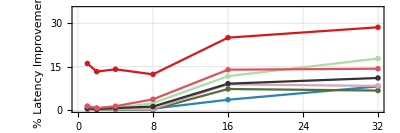

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=ListPlot[
Map[Transpose[{batchSizes,100*#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,35},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.001,0.69},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/heuristic_vs_recall_vs_mxnet_geomean/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"end_to_end_latency_geomean_improvement.pdf",Magnify[fig,1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"end_to_end_latency_geomean_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pngNorm=Export[targetDir<>"data.json",Map[Which[AssociationQ[#],KeyMap[ToString,#],MatchQ[#,_If],"Nothing",True,#]&,alldata,Infinity],"JSON"];
```

## **Does models have improvement by selecting better cudnn heuristics3

```mathematica
mkFig[machine_,modelName_]:=Module[{},
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/"<>machine<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency"];
cudnnfiles=FileNames["batchsize_*/"<>machine<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/cudnn_advised_serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,cudnnfiles}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
cudnndata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machine];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[StringReplace[#["name"],"-"->"_"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&]["mean_time"]&,data];
mxnetdata=Map[If[#<0.1,1000*#,#]&,mxnetdata];
(*fig=BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[cudnndata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
PlotTheme->"Grid",
ChartLegends->{"Recall","CUDNN Heuristic","MXNet"},
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],modelName<>" Time for Recall, CUDNN Heuristic, and MXNet"}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
(Lookup[cudnndata,batchSizes]-Lookup[ourdata,batchSizes])/Lookup[mxnetdata,batchSizes],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Keys[data]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Speedup",14],None},{Style["Batch Size",14],modelName<>" Impact of Heuristics on End-to-End Time"}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];*)
<|
(*"regular"->fig,
"normalized"->nfig,*)
"data"-><|"recall"->ourdata,"cudnn_heuristics"->cudnndata,"mxnet"->mxnetdata,"machine"->machine|>
|>
]
```

```mathematica
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};modelName="ResNet050-v1";
alldata=Table[
es=mkFig[machine,modelName]["data"];
(Lookup[es["cudnn_heuristics"],batchSizes]-Lookup[es["recall"],batchSizes])/Lookup[es["mxnet"],batchSizes]
,
{machine,machines}
]
```

{{0.137396,0.074084,0.0665606,0.108982,0.117655,0.0861522},{0.00779964,0.,0.0293956,0.0446751,0.0845605,0.0856909},{0.0383428,0.00701004,0.00408433,0.00269519,0.00963588,0.0663405},{0.00122801,0.000690532,0.000121001,0.,0.0499609,0.0595347},{0.00444864,0.00409458,0.00195941,0.00124557,0.0616177,0.0736091},{0.,0.000368581,0.,0.,0.0616078,0.0889334},{0.0254633,0.00843354,0.0173078,0.0285933,0.100887,0.118348}}

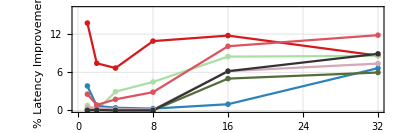

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=ListPlot[
Map[Transpose[{batchSizes,100*#}]&,alldata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,16},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.15,0.69},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["% Latency Improvement",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_heuristic_vs_recall_vs_mxnet/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"serial_end_to_end_latency_improvement.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"serial_end_to_end_latency_improvement.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pngNorm=Export[targetDir<>"data.json",alldata,"JSON"];
```

```mathematica
SystemOpen[targetDir]
```

## Does models have improvement by selecting better cudnn heuristics2

```mathematica
mkFig[modelName_]:=Module[{},
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency"];
cudnnfiles=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/cudnn_advised_serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,cudnnfiles}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
cudnndata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB"];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[StringReplace[#["name"],"-"->"_"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&]["mean_time"]&,data];
mxnetdata=Map[If[#<0.1,1000*#,#]&,mxnetdata];
fig=BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[cudnndata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
PlotTheme->"Grid",
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->10]&/@{"Sequential Recall","Sequential Recall w CUDNN Heuristic","MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
ImageSize->Scaled[1],
BarSpacing->{0.2,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Time for Recall, CUDNN Heuristic, and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
(Lookup[cudnndata,batchSizes]-Lookup[ourdata,batchSizes])/Lookup[mxnetdata,batchSizes],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Keys[data]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Speedup",14],None},{Style["Batch Size",14],None(*modelName<>" Impact of Heuristics on End-to-End Time"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"regular"->fig,
"normalized"->nfig,
"data"-><|"recall"->ourdata,"cudnn_heuristics"->cudnndata,"mxnet"->mxnetdata|>
|>
]
```

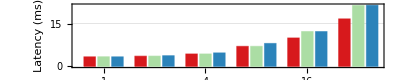
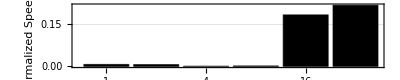
<|regular→-Graphics-,normalized→-Graphics-,data→<|recall→<|1→3.34841,2→3.57834,4→4.35424,8→7.0161,16→9.9632,32→16.6503|>,cudnn_heuristics→<|1→3.3714,2→3.60181,4→4.35424,8→7.02449,16→12.2059,32→21.3303|>,mxnet→<|1→3.34962,2→3.74335,4→4.72657,8→8.03646,16→12.1991,32→21.4343|>|>|>

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
mkFig[modelNames[[16]]]
```

```mathematica
ourdata
```

<|1→0.860739,2→0.930349,4→1.1121,8→1.40272,16→1.7832,32→2.63679|>

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_recall_heuristic_compare/figures/";
Quiet[CreateDirectory[targetDir]];
figs=Table[
data=mkFig[modelName];
json=Export[targetDir<>modelName<>"_data.json",Map[KeyMap[ToString,#]&,DeleteMissing[data["data"],Infinity]] ,"JSON"];
pdfNorm=Export[targetDir<>modelName<>"_normalized.pdf",Magnify[data["normalized"],1.0],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>modelName<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>modelName<>"_regular.pdf",Magnify[data["regular"],1.2],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>modelName<>"_regular.png",data["regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{modelName,modelNames}
(*{modelName,{"DUC"}}*)
];
```

Export::jsonstrictencoding: Expression If cannot be exported as JSON.

## Does Resnet50 have improvement by selecting better cudnn heuristics

```mathematica
mkData[modelName_]:=Table[
machineName="Tesla_V100-SXM2-16GB";
batchSize=ToString[batchSize0];
fullData=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/"<>machineName<>"/"<>batchSize<>".json","RawJSON"]["benchmarks"];
fullData=Select[fullData,StringContainsQ[#["name"],"CUDNN_CONV_FWD_"]&];
data=Lookup[Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".json","RawJSON"],"benchmark"];
convOps=Select[data,StringContainsQ[#["Name"],"CUDNN_CONV_FWD_"]&];
convOps=Select[convOps,#["advised_convolution_algorithm"]=!=#["convolution_algorithm"]&];
getBenchmarkId[name_]:=First[StringCases[name,___~~"__"~~digits:DigitCharacter...~~"<"~~___:>digits]];
getAlts[conv_]:=Module[{id=getBenchmarkId[conv["Name"]]},Select[fullData,getBenchmarkId[#["name"]]===id&]];
getAdvisedTime[conv_]:=Module[{alts=getAlts[conv]},
SelectFirst[alts,#["convolution_algorithm"]==conv["advised_convolution_algorithm"]&]["real_time"]];
totalTime=Total[Lookup[data,"RealTime"]];
fastestConvTime=Total[Lookup[convOps,"RealTime"]];
hypotheticalAdvisedTime=totalTime-fastestConvTime+Total[getAdvisedTime/@convOps];
{totalTime,hypotheticalAdvisedTime}
,
{batchSize0,2^Range[0,5]}
]
```

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
```

```mathematica
es=Association[Table[modelName->mkData[modelName],{modelName,modelNames}]];
es=es/.Total[_Missing]->0;
```

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
endToEndTimes=KeySort@Association@Table[
filedata=Import[file,"CSV"];
xgetBatchSize[file]->Table[
ent=SelectFirst[filedata,StringReplace[ToLowerCase[#[[2]]],"-"->"_"]===StringReplace[ToLowerCase[model],"-"->"_"]&];
If[MissingQ[ent],0,ent[[4]]],
{model,modelNames}
],
{file,files}
];
```

```mathematica
endToEndTimes
```

<|1→{9.8238,1.03855,1.01352,3.99423,0.984669,9.22513,142.93,1.0097,3.88432,5.62906,0.313759,2.24638,1.85704,1.91092,3.23653,3.32165,4.39048,4.60219,8.37255,8.41022,12.1634,12.0387,2.87461,1.25718,1.76716,3.91722,3.49975,4.61507,4.18448,1.4565},2→{10.7181,0.00106645,0.00110292,0.00420189,0.00112057,10.7658,275.597,0,0.00411749,0,0.319481,2.9614,2.10547,2.25639,3.58081,3.72767,5.4307,5.81574,10.2665,10.407,14.8695,14.8635,2.86102,1.28627,2.46286,6.24371,5.53346,7.43771,6.67572,0.00149989},4→{12.9294,0.00118566,0.00130033,0.00492048,0.00127339,14.1263,533.782,0,0.00484705,0,0.335455,3.97849,2.68483,2.98476,4.41575,4.70591,7.55334,8.06737,13.4709,13.6776,19.4819,19.3672,2.99764,1.65796,4.22001,10.7145,9.43565,12.8655,11.457,0.00212646},8→{21.1718,0.00151014,0.00172424,0.00559425,0.00170779,20.1259,1076.46,0,0.00559831,0,0.321627,6.47092,4.34875,4.94194,7.41982,8.01373,12.4316,13.0062,21.5633,21.666,31.158,30.7236,3.58987,2.39658,7.69544,19.6977,17.1952,23.6683,20.9258,0.00373983},16→{30.5967,0.00189281,0.0022583,0.0080862,0.00225377,33.1383,2143.3,0,0.0081172,0,0.305176,11.2121,6.64806,7.84922,10.9692,12.1622,20.7889,22.0957,35.5208,35.9623,51.2328,50.5843,5.53155,4.00519,13.2246,30.9913,25.9976,36.1481,30.7968,0.00535154},32→{53.8263,0.00290036,0.0035038,0.0145338,0.00348759,58.8477,4287.77,0,0.0145288,0,0.321388,20.6289,11.4582,13.8798,18.9989,21.399,38.5439,41.0135,64.9602,65.8727,93.9791,92.8476,8.33941,7.11727,24.2815,58.8925,49.0317,68.5024,57.8856,0.00897622}|>

```mathematica
heuristicSubRecall=Association[Table[
r=es[k];
k->MapThread[#2-#1&,Transpose[r]]/1000000,
{k,Keys[es]}
]]
```

<|ArcFace→{0.0551046,0.0368888,0.0529484,0.0195368,7.08608,12.2743},BVLC_AlexNet→{0,0,0.0676628,0.2455,0.556773,0.939768},BVLC_CaffeNet→{0,0,0.0684876,0.29663,0.281539,0.45978},BVLC_GoogleNet→{0.324903,0.329312,0.350426,0.326688,0.941696,1.1304},BVLC_RCNN_ILSVRC13→{0,0,0.0684876,0.29663,0.281539,0.45978},DenseNet-121→{1.00236,1.01687,0.363766,0.323879,0.397825,0.164491},DUC→{0.271603,0.205476,0.195781,45.6879,108.559,184.167},Emotion-FerPlus→{0.0646171,0.102906,0.0699881,0,0.343533,0.762803},Inception-v1→{0.322272,0.331427,0.354387,0.367899,0.997255,1.40898},Inception-v2→{0,0.010418,0.00405263,0.00575134,0.447655,0.978202},MNIST→{0.00838779,0.00920029,0.00906821,0.00935021,0.0205743,0.0194388},MobileNet-v2→{0.00960963,0.0721694,0.0488972,0.16268,0.159569,0.0790448},ResNet018-v1→{0.0229887,0.023471,0,0.00839105,0.987063,2.26153},ResNet018-v2→{0.0229887,0.023471,0,0.00839105,0.987063,2.26153},ResNet034-v1→{0.0229887,0.023471,0,0.00839105,2.24268,4.68003},ResNet034-v2→{0.0229887,0.023471,0,0.00839105,2.24268,4.68003},ResNet050-v1→{0.0196135,0.0157826,0.0148327,0.0155367,1.28574,2.85712},ResNet050-v2→{0.0622232,0.0532366,0.0568255,0.0272304,0.99323,2.20702},ResNet101-v1→{0.0196135,0.0157826,0.0148327,0.0631903,2.69193,4.90745},ResNet101-v2→{0.0622232,0.0532366,0.0568255,0.074884,2.39942,4.25734},ResNet152-v1→{0.0196135,0.0277072,0.0292061,0.0996313,3.97002,7.00324},ResNet152-v2→{0.0622232,0.0651611,0.071199,0.111325,3.67751,6.35313},Shufflenet→{0,0.018621,0.0131469,0.000298048,0,0},Squeezenet-v1.1→{0.00925618,0.00922122,0.00662898,0.0724333,0.196458,0.295883},Tiny_YOLO-v2→{0.023808,0.0196907,0.0993847,0.402299,2.83699,8.27062},VGG16-BN→{0,0,0,0,6.62976,11.3374},VGG16→{0,0,0,0,6.62976,11.3374},VGG19-BN→{0,0,0,0,9.14364,15.3459},VGG19→{0,0,0,0,9.14364,15.3459},Zfnet512→{0,0,0,0,1.11494,3.76469}|>

```mathematica
modelIdx[name_]:=First[FirstPosition[modelNames,name]]
pltPoints=Table[
our=heuristicSubRecall[k][[batchSize+1]];
end2end=endToEndTimes[2^batchSize][[modelIdx[k]]];
If[end2end==0,0,Tooltip[our/end2end,k]],
{k,Keys[heuristicSubRecall]},
{batchSize,{0,1,2,3,4,5}}
]
```

{{0.0056093,0.00344173,0.00409518,0.000922776,0.231596,0.228035},{0.,0.,57.0678,162.567,294.152,324.017},{0.,0.,52.6692,172.035,124.669,131.223},{0.0813431,78.3724,71.2178,58.3971,116.457,77.7778},{0.,0.,53.7835,173.692,124.919,131.833},{0.108655,0.094454,0.025751,0.0160927,0.012005,0.00279521},{0.00190025,0.000745567,0.00036678,0.0424426,0.0506506,0.0429517},{0.0639962,0,0,0,0,0},{0.0829675,80.4926,73.114,65.7162,122.857,96.9788},{0.,0,0,0,0,0},{0.0267332,0.0287976,0.0270326,0.0290716,0.067418,0.0604837},{0.00427783,0.0243701,0.0122904,0.0251402,0.0142318,0.00383175},{0.0123792,0.0111476,0.,0.00192953,0.148474,0.197373},{0.0120302,0.010402,0.,0.00169793,0.125753,0.162937},{0.00710288,0.00655468,0.,0.0011309,0.204453,0.246332},{0.00692088,0.00629643,0.,0.00104708,0.184397,0.218703},{0.00446728,0.00290618,0.00196373,0.00124977,0.0618474,0.0741264},{0.0135203,0.00915387,0.00704387,0.00209365,0.0449513,0.053812},{0.00234259,0.00153729,0.00110109,0.00293046,0.0757847,0.0755454},{0.00739853,0.00511547,0.00415464,0.00345628,0.0667205,0.0646299},{0.0016125,0.00186336,0.00149914,0.00319762,0.0774898,0.0745191},{0.0051686,0.00438397,0.00367626,0.00362344,0.0727007,0.0684254},{0.,0.00650852,0.00438577,0.0000830247,0.,0.},{0.00736265,0.00716897,0.00399827,0.0302236,0.0490509,0.0415726},{0.0134725,0.00799503,0.0235508,0.0522776,0.214523,0.340614},{0.,0.,0.,0.,0.213923,0.192511},{0.,0.,0.,0.,0.255014,0.231226},{0.,0.,0.,0.,0.25295,0.224019},{0.,0.,0.,0.,0.296903,0.265106},{0.,0.,0.,0.,208.339,419.408}}

```mathematica
lbs=Select[modelNames,StringContainsQ[#,"ResNet"]&];
ms=pltPoints[[modelIdx/@Select[modelNames,StringContainsQ[#,"ResNet"]&]]];
```

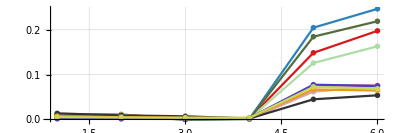

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
ListPlot[ms,
ImageSize->Scaled[0.7],
PlotRange->All,
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid"},
PlotLegends->Placed[SwatchLegend[Style[#,Black,FontSize->14]&/@lbs,LegendMarkers->markers,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.8},{0,0}}] ,
AspectRatio->1/3
]
```

## MXNet Kernel Layer vs Recall

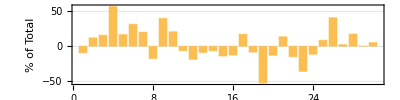

```mathematica
mkPlot[batchSize0_]:=
Module[{batchSize=ToString[batchSize0]},
nsightDataFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results","total_kernel_"<>batchSize<>".csv"}];
nsightData=Import[nsightDataFile,"CSV"];
header=First[nsightData];
nsightData=AssociationThread[header->#]&/@Rest[nsightData];
mxnetMachine="Tesla_V100-SXM2-16GB";
endToEndTimeFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>mxnetMachine,"batchsize_"<>batchSize<>".csv"}];
endToEndTimeData=Import[endToEndTimeFile,"CSV"];
header={"model_idx","model_name","batch_size","min_time","mean_time","max_time"};
endToEndTimeData=AssociationThread[header->#]&/@endToEndTimeData;
modelIds=Range[30];
mxnetdata=Table[
nsightEntry=SelectFirst[nsightData,#["model_idx"]===modelIdx&];
endToEndEntry=SelectFirst[endToEndTimeData,#["model_idx"]===modelIdx&];
cublasTime=nsightEntry["kernel_cublas"];
cudnnTime=nsightEntry["kernel_cudnn"];
endToEndTime=endToEndEntry["mean_time"];
otherTime=endToEndTime-cudnnTime-cublasTime;
otherTime=nsightEntry["kernel_mxnet"]+nsightEntry["other"];
endToEndTime=cublasTime+cudnnTime+otherTime;
If[endToEndTime==0,endToEndTime=1];
If[otherTime<0,Print[modelIdx->otherTime]];
{cudnnTime,cublasTime,otherTime},
{modelIdx,modelIds}
];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_"<>batchSize<>"/"<>mxnetMachine];
recalldata=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(FileBaseName[file]->row),
{file,files}
];
recalldata=Merge[recalldata,Association];
recalldata=Values[Map[KeySort,recalldata][mxnetMachine]];
endToEndTimeData=Table[SelectFirst[endToEndTimeData,#["model_idx"]===id&]["mean_time"],{id,modelIds}];
bardata=100*MapThread[(#1-#2)/#3&,{Total/@mxnetdata,recalldata,endToEndTimeData}];
BarChart[
bardata,
PlotTheme->"Grid",
(*ChartLayout->"Stacked",*)
(*ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"CUDNN","CUBLAS","Other"},Background->Opacity[0.8,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.38,0.9},{0,0}}],*)
ChartLabels->{(Style[#,Black,FontSize->8]&/@Range[Length[nsightData]]),None},
AspectRatio->1/4,
ImageSize->Scaled[0.75],
BarSpacing->Medium,
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.2],GrayLevel[0]],
PlotRange->{{0.5,30.5},All},
FrameTicks->{{True,None},{True,None}},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->12},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->12},
Frame->True,
FrameLabel->{{Style["% of Total",12],None},{Style["Model Index",12],Style["All models running on Tesla_V100-SXM2-16GB using batch size "<> ToString[batchSize] <> " comparing mxnet breakdown against our end-to-end time",14]}}
]
];
mkPlot[1]
```

```mathematica
Total/@mxnetdata
```

{8.52816,0.990109,1.02619,3.56393,0.993448,12.538,143.317,0.784176,2.94873,4.00366,0.0612544,1.6652,1.52293,1.61129,2.77349,2.85038,4.52462,4.05489,2.97441,7.46197,12.7143,10.6873,1.45922,0.719122,1.54065,4.43292,3.40623,4.33417,4.08456,1.33103}

```mathematica
recalldata
```

{9.44975,0.860739,0.863314,1.26841,0.825874,9.61747,114.43,0.966333,1.36127,2.80859,0.082398,2.09113,1.69283,1.73673,3.22947,3.27337,3.76196,4.4467,7.38918,8.55039,11.0569,12.5053,2.51964,0.869797,1.38639,2.82316,3.32372,3.5257,4.08575,1.25382}

```mathematica
mxnetdata
```

{{76.33,0.758875,13.1585},{68.5556,33.9347,12.5399},{68.7605,33.8001,16.3062},{224.006,12.653,44.3166},{71.6511,33.4957,15.1437},{88.6978,0.,41.6696},{98.708,0.,26.5364},{62.3743,5.67123,13.1042},{173.37,9.53974,33.7053},{105.994,0.395587,36.1612},{33.2435,15.1072,25.989},{46.8211,0.,32.8109},{74.9191,0.348576,14.6957},{73.077,0.326499,19.374},{72.6878,0.179943,13.0131},{71.6286,0.170876,15.2784},{93.8599,0.542674,25.8703},{70.7705,0.390465,20.0279},{31.8199,0.0976996,8.33603},{69.855,0.200594,17.2149},{93.0159,0.187361,21.7864},{68.5487,0.136182,16.7772},{50.9031,0.186947,6.82376},{61.8031,0.,20.8739},{69.8804,0.,41.2465},{97.9496,25.2837,33.7865},{69.3192,17.9214,15.2418},{83.2373,16.8842,22.8093},{72.0189,14.6738,13.2781},{57.1374,31.6921,17.3283}}

```mathematica
recalldata
```

{1.25382,1.36458,1.81753,2.85355,3.96189,6.22883}

```mathematica
Do[
fig=mkPlot[batchSize];
baseDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/breakdown/figures";
Quiet[CreateDirectory[baseDir]];
json=AssociationThread[{"CUDNN","CUBLAS","Other"}->#]&/@data;
json=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.json",json,"JSON"];
pdf=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
,
{batchSize,{1,2,4,8,16,32}}
]
```

## MXNet Kernel Layer Breakdown 3

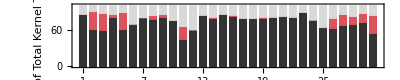

```mathematica
machineName="Tesla_V100-SXM2-16GB";
ClearAll[mkPlot];
mkPlot[batchSize0_]:=
Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
nsightDataFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results","total_kernel_"<>batchSize<>".csv"}];
nsightData=Import[nsightDataFile,"CSV"];
header=First[nsightData];
nsightData=AssociationThread[header->#]&/@Rest[nsightData];
endToEndTimeFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName,"batchsize_"<>batchSize<>".csv"}];
endToEndTimeData=Import[endToEndTimeFile,"CSV"];
header={"model_idx","model_name","batch_size","min_time","mean_time","max_time"};
endToEndTimeData=AssociationThread[header->#]&/@endToEndTimeData;
modelIds=Range[30];


data=Table[
nsightEntry=SelectFirst[nsightData,#["model_idx"]===modelIdx&];
endToEndEntry=SelectFirst[endToEndTimeData,#["model_idx"]===modelIdx&];
cublasTime=nsightEntry["kernel_cublas"];
cudnnTime=nsightEntry["kernel_cudnn"];
endToEndTime=endToEndEntry["mean_time"];
endToEndTime =nsightEntry["total_time"];
otherTime=endToEndTime-cudnnTime-cublasTime;
(*otherTime=nsightEntry["kernel_mxnet"]+nsightEntry["other"];*)
If[endToEndTime==0,endToEndTime=1];
If[otherTime<0,Print[modelIdx->otherTime]];
100*{cudnnTime,cublasTime,otherTime}/endToEndTime,
{modelIdx,modelIds}
];
BarChart[
data,
ChartLayout->"Stacked",
ChartStyle->{RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],GrayLevel[0.85]},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"cuDNN","cuBLAS","Other"},Background->Opacity[0.6,White],LegendMargins->1,LegendMarkerSize->8,LegendLayout->{"Row",1}],{{0.25,0.8},{0,0}}],
ChartLabels->{(Style[#,Black,FontSize->10]&/@Range[Length[nsightData]]),None},
AspectRatio->1/5,
ImageSize->Scaled[0.75],
BarSpacing->Medium,
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.2],GrayLevel[0]],
PlotRange->{{0.5,30.5},All},
(*FrameTicks->{{True,None},{True,None}},*)
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10},
Frame->True,
FrameLabel->{{Style["% of Total\nKernel Time",13],None},{Style["Model Index",12],None(*Style["All models running on Tesla_V100-SXM2-16GB using batch size "<> ToString[batchSize],14]*)}}
]
];
Magnify[mkPlot[1],1.1]
```

```mathematica
Do[
fig=mkPlot[batchSize];
baseDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/breakdown/figures";
Quiet[CreateDirectory[baseDir]];
json=AssociationThread[{"CUDNN","CUBLAS","Other"}->#]&/@data;
json=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.json",json,"JSON"];
pdf=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
,
{batchSize,{1(*,2,4,8,16,32*)}}
]
```

```mathematica
SystemOpen[baseDir]
```

## MXNet Kernel Layer Breakdown 2

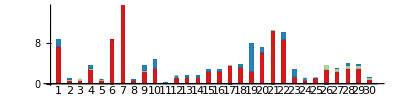
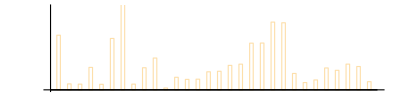

```mathematica
mkPlot[batchSize0_]:=
Module[{batchSize=ToString[batchSize0]},
nsightDataFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results","total_kernel_"<>batchSize<>".csv"}];
nsightData=Import[nsightDataFile,"CSV"];
header=First[nsightData];
nsightData=AssociationThread[header->#]&/@Rest[nsightData];
endToEndTimeFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB","batchsize_"<>batchSize<>".csv"}];
endToEndTimeData=Import[endToEndTimeFile,"CSV"];
header={"model_idx","model_name","batch_size","min_time","mean_time","max_time"};
endToEndTimeData=AssociationThread[header->#]&/@endToEndTimeData;
modelIds=Range[30];
data=Table[
nsightEntry=SelectFirst[nsightData,#["model_idx"]===modelIdx&];
endToEndEntry=SelectFirst[endToEndTimeData,#["model_idx"]===modelIdx&];
cublasTime=nsightEntry["kernel_cublas"];
cudnnTime=nsightEntry["kernel_cudnn"];
otherTime=nsightEntry["kernel_mxnet"]+nsightEntry["other"];
endToEndTime=endToEndEntry["mean_time"];
otherTime=endToEndTime-cudnnTime-cublasTime-otherTime;
{{cudnnTime,cublasTime,otherTime},endToEndTime},
{modelIdx,modelIds}
];
Overlay[{
BarChart[
data[[All,1]],
ChartLayout->"Stacked",
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
ChartLegends->Placed[{"cudnn","cublas","other"},Above],
ChartLabels->{(Style[#,Black]&/@Range[Length[nsightData]]),None},
AspectRatio->1/4,
PlotRange->{0,15},
ImageSize->Scaled[0.75],
BarSpacing->{2,2},
ImagePadding->{{20,20},{0,20}},
ImageMargins->{{0,0},{0,0}},
PlotRangeClipping->False
],
BarChart[
data[[All,2]],
Frame->None,
Ticks->None,
PlotRange->{0,15},
AspectRatio->1/4,
ImageSize->Scaled[0.75],
ChartStyle->White,
ChartLegends->Placed[{"e2e"},Above],
BarSpacing->{2,2},
ImagePadding->{{20,20},{0,20}},
ImageMargins->{{10,0},{0,0}},
PlotRangeClipping->False
]
}]
];
mkPlot[1]
```

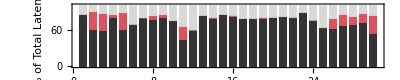

```mathematica
mkPlot[batchSize0_]:=
Module[{batchSize=ToString[batchSize0]},
nsightDataFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results","total_kernel_"<>batchSize<>".csv"}];
nsightData=Import[nsightDataFile,"CSV"];
header=First[nsightData];
nsightData=AssociationThread[header->#]&/@Rest[nsightData];
endToEndTimeFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB","batchsize_"<>batchSize<>".csv"}];
endToEndTimeData=Import[endToEndTimeFile,"CSV"];
header={"model_idx","model_name","batch_size","min_time","mean_time","max_time"};
endToEndTimeData=AssociationThread[header->#]&/@endToEndTimeData;
modelIds=Range[30];
data=Table[
nsightEntry=SelectFirst[nsightData,#["model_idx"]===modelIdx&];
endToEndEntry=SelectFirst[endToEndTimeData,#["model_idx"]===modelIdx&];
cublasTime=nsightEntry["kernel_cublas"];
cudnnTime=nsightEntry["kernel_cudnn"];
endToEndTime=endToEndEntry["mean_time"];
otherTime=endToEndTime-cudnnTime-cublasTime;
otherTime=nsightEntry["kernel_mxnet"]+nsightEntry["other"];
endToEndTime=cublasTime+cudnnTime+otherTime;
If[endToEndTime==0,endToEndTime=1];
If[otherTime<0,Print[modelIdx->otherTime]];
100*{cudnnTime,cublasTime,otherTime}/endToEndTime,
{modelIdx,modelIds}
];
BarChart[
data,
ChartLayout->"Stacked",
ChartStyle->{RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],GrayLevel[0.85]},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->14]&/@{"cuDNN","cuBLAS","Other"},Background->Opacity[0.6,White],LegendMargins->1,LegendMarkerSize->8,LegendLayout->{"Row",1}],{{0.25,0.8},{0,0}}],
ChartLabels->{(Style[#,Black,FontSize->16]&/@Range[Length[nsightData]]),None},
AspectRatio->1/5,
ImageSize->Scaled[0.75],
BarSpacing->Medium,
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.2],GrayLevel[0]],
PlotRange->{{0.5,30.5},All},
FrameTicks->{{True,None},{True,None}},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
Frame->True,
FrameLabel->{{Style["% of Total Latency",13],None},{Style["Model Index",12],None(*Style["All models running on Tesla_V100-SXM2-16GB using batch size "<> ToString[batchSize],14]*)}}
]
];
Magnify[mkPlot[1],1.1]
```

```mathematica
Do[
fig=mkPlot[batchSize];
baseDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/breakdown/figures";
Quiet[CreateDirectory[baseDir]];
json=AssociationThread[{"CUDNN","CUBLAS","Other"}->#]&/@data;
json=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.json",json,"JSON"];
pdf=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[baseDir<>"/Tesla_V100-SXM2-16GB_batchsize_"<>ToString[batchSize]<>"_breakdown.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
,
{batchSize,{1,2,4,8,16,32}}
]
```

```mathematica
SystemOpen[baseDir]
```

## MXNet Layer Breakdown

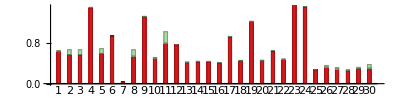
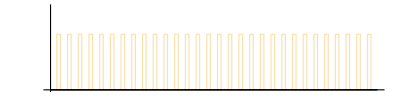

```mathematica
mkPlot[batchSize0_]:=
Module[{batchSize=ToString[batchSize0]},
nsightDataFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results","total_"<>batchSize<>".csv"}];
nsightData=Import[nsightDataFile,"CSV"];
header=First[nsightData];
nsightData=AssociationThread[header->#]&/@Rest[nsightData];
endToEndTimeFile=FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB","batchsize_"<>batchSize<>".csv"}];
endToEndTimeData=Import[endToEndTimeFile,"CSV"];
header={"model_idx","model_name","batch_size","min_time","mean_time","max_time"};
endToEndTimeData=AssociationThread[header->#]&/@endToEndTimeData;
modelIds=Range[30];
data=Table[
nsightEntry=SelectFirst[nsightData,#["model_idx"]===modelIdx&];
endToEndEntry=SelectFirst[endToEndTimeData,#["model_idx"]===modelIdx&];
cublasTime=nsightEntry["cublas_time"];
cudnnTime=nsightEntry["cudnn_time"];
endToEndTime=endToEndEntry["mean_time"];
otherTime=endToEndTime-cudnnTime-cublasTime;
{{cudnnTime,cublasTime}/endToEndTime,1},
{modelIdx,modelIds}
];
Overlay[{
BarChart[
data[[All,1]],
ChartLayout->"Stacked",
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
ChartLegends->Placed[{"cudnn","cublas"},Above],
ChartLabels->{(Style[#,Black]&/@Range[Length[nsightData]]),None},
AspectRatio->1/4,
PlotRange->{0,1.5},
ImageSize->Scaled[0.75],
BarSpacing->{2,2},
ImagePadding->{{20,20},{30,20}},
ImageMargins->{{0,0},{0,0}}
],
BarChart[
data[[All,2]],
Frame->None,
Ticks->None,
PlotRange->{0,1.5},
AspectRatio->1/4,
ImageSize->Scaled[0.75],
ChartStyle->White,
ChartLegends->Placed[{"e2e"},Above],
BarSpacing->{2,2},
ImagePadding->{{20,20},{30,20}},
ImageMargins->{{10,0},{0,0}}
]
}]
];
mkPlot[1]
```

```mathematica
data
```

{{{0.143941,0.00108432},1},{{237.628,45.5658},1},{{458.598,60.4196},1},{{489.037,3.98265},1},{{265.449,37.4731},1},{{0.0886875,8.60658×10^-6},1},{{0.00113779,1.255×10^-7},1},{{0,0},1},{{345.864,3.6604},1},{{0,0},1},{{0.834695,0.215069},1},{{0.084007,0.0000255562},1},{{0.0864778,0.00485208},1},{{0.0693125,0.00405212},1},{{0.0979435,0.00314565},1},{{0.0859369,0.00269067},1},{{0.0858701,0.00153079},1},{{0.0588371,0.00154923},1},{{0.107048,0.00101486},1},{{0.0728692,0.000940965},1},{{0.110104,0.000671557},1},{{0.0912893,0.00087974},1},{{0.812137,0.00629471},1},{{0.2749,0.0000428085},1},{{0.024258,0.0000122759},1},{{0.0202462,0.00235706},1},{{0.0243405,0.0030465},1},{{0.0217185,0.00214083},1},{{0.0257398,0.00247951},1},{{109.827,15.2463},1}}

## Examine Layer Times V100

```mathematica
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/ResNet050-v1.json","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
data=raw=Association[Table[xgetBatchSize[file]->Import[file,"RawJSON"],{file,files}]];
data=data[32];
```

```mathematica
conv=Select[data,StringContainsQ[#["benchmark"]["Name"],"CONV_FWD"]&];
```

```mathematica
conv
```

{<|type→forward,benchmark→<|CPUTime→700460,CUBLASVersion→10.1,CUDADriverVersion→10.10,62,stride_width→2,workspace_bytes→75272,workspace_megabytes→0.071785|>,flops_information→<|multiply_adds→3776446464,additions→0,divisions→0,exponentiations→0,comparisons→0,general→0|>|>,51,<|1|>}
 |  |  |  |

```mathematica
Dataset[conv[[53]]]
```

## Analysis of Model 23 from Nsight (batchsize=1)

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/nsight/results/23_1_cudnn.csv","CSV"];
header=data[[1]];
data=AssociationThread[header->#]&/@Rest[Most[data]];
begin=data[[1]]["Start"];
data=Table[
Join[e,<|"Start"->e["Start"]-begin,"End"->e["End"]-begin|>]
,
{e,data}
];
```

```mathematica
intervals=Map[Interval[{#["Start"],#["End"]-0.1}]&,data]
```

{Interval[{0,69823.9}],Interval[{85236,138458.}],Interval[{179158,212789.}],Interval[{218423,237648.}],Interval[{301174,460419.}],Interval[{462857,502518.}],Interval[{513429,530767.}],Interval[{623281,647672.}],Interval[{655469,671037.}],Interval[{722355,869770.}],Interval[{872233,911906.}],Interval[{920509,936898.}],Interval[{1040400,1.18853×10^6}],Interval[{1191029,1.22905×10^6}],Interval[{1237600,1.25339×10^6}],Interval[{1345194,1.37038×10^6}],Interval[{1377675,1.39413×10^6}],Interval[{1431613,1.58177×10^6}],Interval[{1584193,1.62195×10^6}],Interval[{1630631,1.65957×10^6}],Interval[{1702945,1.84697×10^6}],Interval[{1848783,1.88532×10^6}],Interval[{1892361,1.90796×10^6}],Interval[{1964589,1.9859×10^6}],Interval[{1991635,2.00643×10^6}],Interval[{2014343,2.15542×10^6}],Interval[{2157818,2.1931×10^6}],Interval[{2200124,2.21523×10^6}],Interval[{2267359,2.39706×10^6}],Interval[{2398794,2.44714×10^6}],Interval[{2454359,2.47006×10^6}],Interval[{2514670,2.53216×10^6}],Interval[{2537687,2.55216×10^6}],Interval[{2559974,2.70009×10^6}],Interval[{2702439,2.77517×10^6}],Interval[{2783485,2.79979×10^6}],Interval[{2837759,2.85643×10^6}],Interval[{2865481,3.00743×10^6}],Interval[{3009715,3.05707×10^6}],Interval[{3065058,3.08232×10^6}],Interval[{3160131,3.18448×10^6}],Interval[{3191979,3.22229×10^6}],Interval[{3262609,3.41329×10^6}],Interval[{3415715,3.45294×10^6}],Interval[{3461344,3.47718×10^6}],Interval[{3581335,3.73132×10^6}],Interval[{3733773,3.77076×10^6}],Interval[{3778804,3.79504×10^6}],Interval[{3885990,3.91089×10^6}],Interval[{3918188,3.93355×10^6}],Interval[{3972057,4.11861×10^6}],Interval[{4121055,4.17146×10^6}],Interval[{4180033,4.19641×10^6}],Interval[{4239046,4.38293×10^6}],Interval[{4385270,4.42109×10^6}],Interval[{4428165,4.44377×10^6}],Interval[{4506309,4.52525×10^6}],Interval[{4531269,4.54686×10^6}],Interval[{4554346,4.69656×10^6}],Interval[{4698935,4.73463×10^6}],Interval[{4742169,4.75751×10^6}],Interval[{4814106,4.954×10^6}],Interval[{4956335,4.9937×10^6}],Interval[{5000716,5.01604×10^6}],Interval[{5060875,5.08943×10^6}],Interval[{5095913,5.11299×10^6}],Interval[{5120766,5.25947×10^6}],Interval[{5261822,5.29892×10^6}],Interval[{5312033,5.329×10^6}],Interval[{5369711,5.51019×10^6}],Interval[{5511972,5.55823×10^6}],Interval[{5565587,5.58357×10^6}],Interval[{5628271,5.64678×10^6}],Interval[{5652276,5.66701×10^6}],Interval[{5674139,5.81302×10^6}],Interval[{5815368,5.85016×10^6}],Interval[{5867650,5.88554×10^6}],Interval[{5927777,6.07104×10^6}],Interval[{6072797,6.10863×10^6}],Interval[{6115626,6.13065×10^6}],Interval[{6188003,6.20834×10^6}],Interval[{6213859,6.22868×10^6}],Interval[{6236104,6.37619×10^6}],Interval[{6378072,6.41441×10^6}],Interval[{6421469,6.43648×10^6}],Interval[{6477561,6.61549×10^6}],Interval[{6617843,6.67141×10^6}],Interval[{6679077,6.69505×10^6}],Interval[{6740116,6.75807×10^6}],Interval[{6763721,6.77833×10^6}],Interval[{6785560,6.92407×10^6}],Interval[{6925764,6.97292×10^6}],Interval[{6980323,6.99823×10^6}],Interval[{7038880,7.18366×10^6}],Interval[{7185984,7.2217×10^6}],Interval[{7228481,7.24462×10^6}],Interval[{7303517,7.32231×10^6}],Interval[{7327773,7.34221×10^6}],Interval[{7349611,7.49166×10^6}],Interval[{7494100,7.52951×10^6}],Interval[{7536327,7.55207×10^6}],Interval[{7603466,7.62255×10^6}],Interval[{7631964,7.77207×10^6}],Interval[{7773723,7.81103×10^6}],Interval[{7818398,7.83477×10^6}],Interval[{7925117,7.94977×10^6}],Interval[{7957587,7.97249×10^6}],Interval[{8004725,8.15326×10^6}],Interval[{8155570,8.19225×10^6}],Interval[{8200064,8.22982×10^6}],Interval[{8313282,8.46152×10^6}],Interval[{8463857,8.50049×10^6}],Interval[{8508250,8.53739×10^6}],Interval[{8614889,8.63778×10^6}],Interval[{8645523,8.66113×10^6}],Interval[{8706745,8.85153×10^6}],Interval[{8853882,8.89247×10^6}],Interval[{8900795,8.91647×10^6}],Interval[{8957837,9.10268×10^6}],Interval[{9105126,9.14052×10^6}],Interval[{9159875,9.17814×10^6}],Interval[{9223562,9.24322×10^6}],Interval[{9249468,9.26397×10^6}],Interval[{9271838,9.41417×10^6}],Interval[{9416501,9.45238×10^6}],Interval[{9470421,9.48841×10^6}],Interval[{9530035,9.67139×10^6}],Interval[{9673228,9.70886×10^6}],Interval[{9715866,9.73143×10^6}],Interval[{9787218,9.8072×10^6}],Interval[{9813051,9.82791×10^6}],Interval[{9835305,9.97572×10^6}],Interval[{9978208,1.00139×10^7}],Interval[{10020453,1.0036×10^7}],Interval[{10073106,1.01047×10^7}]}

```mathematica
DeleteCases[Flatten[Table[
If[a==b,Interval[],IntervalIntersection[a,b]],
{a,intervals},{b,intervals}
]],Interval[]]
```

{}

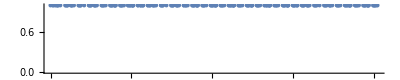

```mathematica
NumberLinePlot[
(*Map[Interval[{#["Start"],#["End"]}]&,data],*)
Map[{#["Start"],#["End"]}&,data],
(*PlotTheme->"Detailed",*)
AspectRatio->1/5,
ImageSize->Scaled[0.75]
]
```

## MXNet ResNet50 Times vs Nsight (batchsize=1)

```mathematica
nsightData=;
```

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet"];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=r=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Lookup[r[1],"mean_time"];
nsightData=Last/@Rest[ImportString[nsightData,"CSV"]];
```

```mathematica
nsightData
```

{6.78243,0.922136,0.947388,5.77634,0.830409,5.62085,5.38762,0.669088,6.09826,3.40947,0.427888,1.92384,1.12645,0.963022,1.59441,1.7826,3.76023,2.46517,6.71712,4.33238,10.0107,6.54575,7.34505,2.08175,0.609608,1.30056,1.21223,1.57034,1.43944,0.660915}

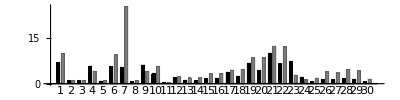

```mathematica
BarChart[
Transpose[{nsightData,mxnetdata}],
ChartStyle->{Black,Gray},
ChartLegends->{"Nsight","MXNet"},
ChartLabels->{(Style[#,Black]&/@Range[Length[nsightData]]),None},
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{0.5,1}
]
```

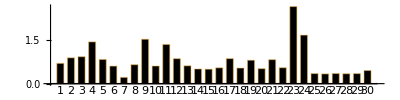

```mathematica
BarChart[
nsightData/mxnetdata,
ChartStyle->Black,
ChartLegends->{"Nsight","MXNet"},
ChartLabels->(Style[#,Black]&/@Range[Length[nsightData]]),
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{0.5,1}
]
```

## MXNet ResNet50 Times vs Our Recall

```mathematica
modelName="ResNet050-v1";
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet"];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,#["name"]===modelName&]["mean_time"]&,data];
```

```mathematica
Map[Total[Lookup[Select[#,#["LayerType"]==="Conv"&&StringContainsQ[#["BenchmarkName"],"ADD_TEN"]&],"RealTime(ms)"]]&,KeySort[raw]]
```

<|1→0.190855,2→0.225529,4→0.456204,8→0.649547,16→0.704506,32→1.82327|>

```mathematica
Map[Total[Lookup[Select[#,#["LayerType"]==="Conv"&&!StringContainsQ[#["BenchmarkName"],"ADD_TEN"]&],"RealTime(ms)"]]&,KeySort[raw]]
```

<|1→2.69114,2→3.1133,4→4.72732,8→7.08844,16→8.56267,32→18.3094|>

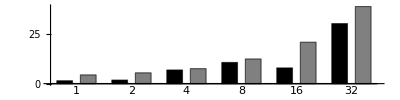

```mathematica
BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{Black,Gray},
ChartLegends->{"Recall","MXNet"},
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{0.5,1}
]
```

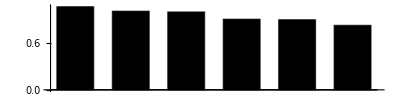

```mathematica
BarChart[
Lookup[ourdata,batchSizes]/Lookup[mxnetdata,batchSizes],
ChartStyle->Black,
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{0.5,1}
]
```

## **MXNet Times vs Our Serial Recall for website (ResNet50)

```mathematica
modelNames={"ResNet050-v1"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourserialdata=data;
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourparalleldata=data;
files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;
<|"machine"->machineName,"batchsize"->batchSize0,"serial_recall"->First[Lookup[ourserialdata,toUniformModelName/@modelNames]],"parallel_recall"->First[Lookup[ourparalleldata,toUniformModelName/@modelNames]],"mxnet"->First[Lookup[mxnetdata,toUniformModelName/@modelNames]]|>
]
```

```mathematica
alldata=<||>;
Do[
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_parallel_recall_compare_models/batchsize_"<>ToString[batchSize]<>"/";
Quiet[CreateDirectory[targetDir]];
data=mkFig[machine,batchSize];
data= data/._Missing->0;
If[!KeyExistsQ[alldata,machine],
alldata[machine]=<||>
];
alldata[machine][batchSize]=data;
,
{batchSize,{1,2,4,8,16,32}},
{machine,machines}
]
;
```

```mathematica
edata=Map[Min[#["serial_recall"]/#["mxnet"],1]&,Lookup[#,{1,2,4,8,16,32}]]&/@Lookup[alldata,machines]
```

{{0.772058,0.786856,0.822587,0.763976,0.781478,0.821747},{0.884891,0.84988,0.819972,0.811938,0.7872,0.81336},{0.802645,0.884916,0.87555,0.843396,0.809988,0.838027},{0.961037,0.914138,0.938525,0.915918,0.882992,0.895769},{1,0.99423,0.996411,0.937473,0.879256,0.86778},{0.965553,0.919468,0.966078,0.770413,0.770765,0.838247},{0.928554,0.88907,0.890359,0.718254,0.730565,0.791757}}

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
machines
```

{Tesla_K80,Tesla_M60,TITAN_Xp,TITAN_V,Tesla_V100-SXM2-16GB,Quadro_RTX_6000,Tesla_T4}

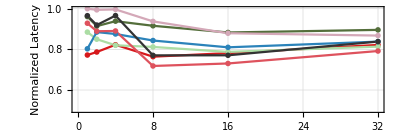

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,edata],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0.5,1},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.15,0.05},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/resnet50_v1_geomean_normalized_serial/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"resnet50_v1_serial_geomean_mxnet.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"resnet50_v1_serial_geomean_mxnet.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

```mathematica
SystemOpen[targetDir]
```

## **MXNet Times vs Our Serial Recall for website

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourserialdata=data;
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourparalleldata=data;
files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;
fig=BarChart[
Transpose[{Lookup[ourserialdata,toUniformModelName/@modelNames],Lookup[ourparalleldata,toUniformModelName/@modelNames],Lookup[mxnetdata,toUniformModelName/@modelNames]}],
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823]},
PlotTheme->"Grid",
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"SerialRecall","ParallelRecall","MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->16,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Range[Length[modelNames]]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Model Index",14],None(*"Time for Recall and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
Transpose[{
Lookup[ourserialdata,toUniformModelName/@modelNames]/Lookup[mxnetdata,toUniformModelName/@modelNames],
Lookup[ourparalleldata,toUniformModelName/@modelNames]/Lookup[mxnetdata,toUniformModelName/@modelNames]
}],
PlotTheme->"Grid",
BarSpacing->{0.5,1},
ChartStyle->{Gray,Black},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"Sequential","Parallel"},Background->Opacity[0.5,White],LegendMarkerSize->16,LegendLayout->{"Row",1}],{{0.01,0.85},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Range[Length[modelNames]]),None},
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Model Index",14],None(*"Normalized Time (Recall/MXNet)"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"regular"->fig,
"normalized"->nfig,
"data"-><|"machine"->machineName,"batchsize"->batchSize0,"serial_recall"->Lookup[ourserialdata,toUniformModelName/@modelNames],"parallel_recall"->Lookup[ourparalleldata,toUniformModelName/@modelNames],"mxnet"->Lookup[mxnetdata,toUniformModelName/@modelNames]|>
|>
]
```

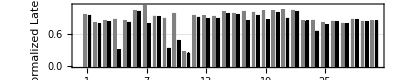

```mathematica
Quiet[mkFig["Tesla_V100-SXM2-16GB",1]]["normalized"]
```

```mathematica
alldata=<||>;
Do[
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_parallel_recall_compare_models/batchsize_"<>ToString[batchSize]<>"/";
Quiet[CreateDirectory[targetDir]];
data=mkFig[machine,batchSize];
data["data"]= data["data"]/._Missing->0;
If[!KeyExistsQ[alldata,machine],
alldata[machine]=<||>
];
alldata[machine][batchSize]=data["data"];
json=Export[targetDir<>machine<>"_data.json", data["data"] ,"JSON"];
pdfNorm=Export[targetDir<>machine<>"_normalized.pdf",data["normalized"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>machine<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>machine<>"_regular.pdf",data["regular"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>machine<>"_regular.png",data["regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{batchSize,{1,2,4,8,16,32}},
{machine,machines}
]
;
```

```mathematica
alldataCache=;
If[Developer`SymbolQ[alldata],
alldata=alldataCache
];
```

```mathematica
getNorm[machine0_]:=Module[{machine=Association[machine0]},
Quiet[#["serial_recall"]/#["mxnet"]]/.ComplexInfinity->Nothing&/@machine
]
```

```mathematica
ClearAll[getGeoMean]
getGeoMean[machine0_]:=Module[{machine=Association[machine0]},
GeometricMean[Quiet[Select[#["serial_recall"]/#["mxnet"],#<100&]]/.ComplexInfinity->Nothing]&/@machine
];
getParallelGeoMean[machine0_]:=Module[{machine=Association[machine0]},
GeometricMean[Quiet[#["parallel_recall"]/#["mxnet"]]/.ComplexInfinity->Nothing]&/@machine
]
```

```mathematica
Values/@Values[getGeoMean/@alldata]
```

{{0.620862,0.671171,0.709887,0.534746,0.555559,0.576979},{0.713171,0.706632,0.717758,0.72557,0.686975,0.709472},{0.625621,0.635414,0.653383,0.687776,0.659074,0.663079},{0.809115,0.838954,0.85323,0.840011,0.796011,0.776756},{0.902946,0.884356,0.875349,0.848923,0.806398,0.765928},{0.856071,0.839725,0.878066,0.746015,0.705045,0.755781},{0.918855,0.908849,0.875443,0.744639,0.705551,0.746605}}

```mathematica
batchSizes={1,2,4,8,16,32};
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]]
```

{{{1,0.620862},{2,0.671171},{4,0.709887},{8,0.534746},{16,0.555559},{32,0.576979}},{{1,0.713171},{2,0.706632},{4,0.717758},{8,0.72557},{16,0.686975},{32,0.709472}},{{1,0.625621},{2,0.635414},{4,0.653383},{8,0.687776},{16,0.659074},{32,0.663079}},{{1,0.809115},{2,0.838954},{4,0.85323},{8,0.840011},{16,0.796011},{32,0.776756}},{{1,0.902946},{2,0.884356},{4,0.875349},{8,0.848923},{16,0.806398},{32,0.765928}},{{1,0.856071},{2,0.839725},{4,0.878066},{8,0.746015},{16,0.705045},{32,0.755781}},{{1,0.918855},{2,0.908849},{4,0.875443},{8,0.744639},{16,0.705551},{32,0.746605}}}

```mathematica
batchSizes={1,2,4,8,16,32};
Map[Transpose[{batchSizes,#}]&,Values/@Values[getParallelGeoMean/@alldata]]
```

{{{1,0.620862},{2,0.671171},{4,0.709887},{8,0.534746},{16,0.555559},{32,0.983897}},{{1,0.713171},{2,0.706632},{4,0.717758},{8,0.72557},{16,0.686975},{32,0.919039}},{{1,0.625621},{2,0.635414},{4,0.653383},{8,0.687776},{16,0.659074},{32,0.663079}},{{1,0.809115},{2,0.838954},{4,0.85323},{8,0.840011},{16,0.796011},{32,0.776756}},{{1,0.902946},{2,0.884356},{4,0.875349},{8,0.848923},{16,0.806398},{32,0.765928}},{{1,0.856071},{2,0.839725},{4,0.878066},{8,0.746015},{16,0.705045},{32,0.755781}},{{1,0.918855},{2,0.908849},{4,0.875443},{8,0.744639},{16,0.705551},{32,0.746605}}}

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
```

```mathematica
nalldata=Map[Min[#,1]&,alldata,{3}];
```

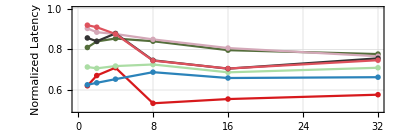

```mathematica
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
nalldata=Map[Min[#,1]&,alldata,{3}];
fig=ListPlot[
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0.5,1},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->12]&/@machines,LegendMarkers->markers,Background->Opacity[0,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.15,0.69},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{True,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->16}
];
(*fig=Magnify[fig,1.2]*)
fig
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/geomean_normalized_serial/";
Quiet[CreateDirectory[targetDir]];
pdfNorm=Export[targetDir<>"serial_geomean_mxnet.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>"serial_geomean_mxnet.png",Magnify[ fig,0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
```

```mathematica
SystemOpen[targetDir]
```

```mathematica
pdfNorm
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/geomean_normalized_serial/serial_geomean_mxnet.pdf

```mathematica
StringRiffle[
Flatten@
Table[{
"## System "<>machine<>"\n",
Table[
{
"## BatchSize "<>batchsize<>" on System " <>machine<> "\n",
"### Normalized Against MXNet End-to-End Runtime\n\n",
"{{< lightbox src=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_normalized.png\" centered=\"true\" width=\"80%\" >}}

<div class=\"right-buttons flex justify-end\">
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_normalized.pdf\">}}PDF{{< /button >}}
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_data.json\">}}JSON{{< /button >}}
</div>
",
"### Comparing Latency of Parallel, Serial, and MXNet End-to-End Runtime\n\n",
"{{< lightbox src=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_regular.png\" centered=\"true\" width=\"80%\" >}}

<div class=\"right-buttons flex justify-end\">
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_regular.pdf\">}}PDF{{< /button >}}
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/serial_parallel_recall_compare_models/batchsize_"<>batchsize<>"/"<>machine<>"_data.json\">}}JSON{{< /button >}}
</div>
"
}
,
{batchsize,{"1","2","4","8","16","32"}}
]},
{machine,machines}
],
"\n"
]//CopyToClipboard
```

## MXNet Times vs Our Serial Recall for website

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNames["batchsize_"<>batchSize<>"/"<>machineName<>"/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency/"],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;
fig=BarChart[
Transpose[{Lookup[ourdata,toUniformModelName/@modelNames],Lookup[mxnetdata,toUniformModelName/@modelNames]}],
ChartStyle->{Gray,Black},
PlotTheme->"Grid",
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"Sequential","MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->16,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Range[Length[modelNames]]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Model Index",14],None(*"Time for Recall and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
Lookup[ourdata,toUniformModelName/@modelNames]/Lookup[mxnetdata,toUniformModelName/@modelNames],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Range[Length[modelNames]]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->{0,1},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Model Index",14],None(*"Normalized Time (Recall/MXNet)"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"serial_regular"->fig,
"normalized"->nfig,
"data"-><|"machine"->machineName,"batchsize"->batchSize0,"serial_recall"->Lookup[ourdata,toUniformModelName/@modelNames],"mxnet"->Lookup[mxnetdata,toUniformModelName/@modelNames]|>
|>
]
```

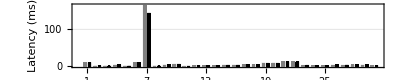
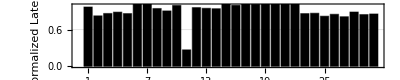
<|serial_regular→-Graphics-,normalized→-Graphics-,data→<|machine→Tesla_V100-SXM2-16GB,batchsize→1,serial_recall→{9.57067,0.8848,0.887375,3.59093,0.860208,9.69347,164.767,0.974695,3.6121,5.71914,0.088712,2.17533,1.78868,1.81178,3.32532,3.34841,4.57603,4.71197,8.81634,8.81567,12.9529,12.7706,2.55095,1.13759,1.46253,3.36116,2.8606,4.12319,3.56314,1.26068},mxnet→{9.85154,1.07028,1.02534,4.04509,0.995898,9.26619,143.404,1.02981,3.98136,5.73506,0.327738,2.26222,1.88232,1.92048,3.24992,3.34962,4.40854,4.62979,8.41914,8.43763,12.2128,12.0931,2.95372,1.30866,1.78134,3.94402,3.52074,4.63564,4.2033,1.47045}|>|>

```mathematica
Quiet[mkFig["Tesla_V100-SXM2-16GB",1]]
```

```mathematica
alldata=<||>;
Do[
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_recall_compare_models/batchsize_"<>ToString[batchSize]<>"/";
Quiet[CreateDirectory[targetDir]];
data=mkFig[machine,batchSize];
data["data"]= data["data"]/._Missing->0;
If[!KeyExistsQ[alldata,machine],
alldata[machine]=<||>
];
alldata[machine][batchSize]=data["data"];
json=Export[targetDir<>machine<>"_data.json", data["data"] ,"JSON"];
pdfNorm=Export[targetDir<>machine<>"_normalized.pdf",data["normalized"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>machine<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>machine<>"_regular.pdf",data["serial_regular"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>machine<>"_regular.png",data["serial_regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{batchSize,{1,2,4,8,16,32}},
{machine,machines}
]
;
```

```mathematica
alldataCache=;
```

```mathematica
getNorm[machine0_]:=Module[{machine=Association[machine0]},
Quiet[#["serial_recall"]/#["mxnet"]]/.ComplexInfinity->Nothing&/@machine
]
```

```mathematica
getNorm/@alldata;
```

```mathematica
getGeoMean[machine0_]:=Module[{machine=Association[machine0]},
GeometricMean[Quiet[#["serial_recall"]/#["mxnet"]]/.ComplexInfinity->Nothing]&/@machine
]
```

```mathematica
Values/@Values[getGeoMean/@alldata]
```

{{0.620862,0.671171,0.709887,0.534746,0.555559,0.983897},{0.713171,0.706632,0.717758,0.72557,0.686975,0.919039},{0.625621,0.635414,0.653383,0.687776,0.659074,0.663079},{0.809115,0.838954,0.85323,0.840011,0.796011,0.776756},{0.902946,0.884356,0.875349,0.848923,0.806398,0.765928},{0.856071,0.839725,0.878066,0.746015,0.705045,0.755781},{0.918855,0.908849,0.875443,0.744639,0.705551,0.746605}}

```mathematica
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]]
```

{{{1,0.620862},{2,0.671171},{4,0.709887},{8,0.534746},{16,0.555559},{32,0.983897}},{{1,0.713171},{2,0.706632},{4,0.717758},{8,0.72557},{16,0.686975},{32,0.919039}},{{1,0.625621},{2,0.635414},{4,0.653383},{8,0.687776},{16,0.659074},{32,0.663079}},{{1,0.809115},{2,0.838954},{4,0.85323},{8,0.840011},{16,0.796011},{32,0.776756}},{{1,0.902946},{2,0.884356},{4,0.875349},{8,0.848923},{16,0.806398},{32,0.765928}},{{1,0.856071},{2,0.839725},{4,0.878066},{8,0.746015},{16,0.705045},{32,0.755781}},{{1,0.918855},{2,0.908849},{4,0.875443},{8,0.744639},{16,0.705551},{32,0.746605}}}

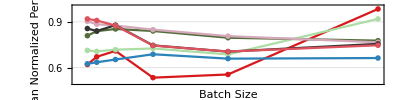

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
ListPlot[
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0.5,1},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,LegendMarkers->markers,Background->Opacity[0.1,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.05,0.85},{0,0}}] ,
AspectRatio->1/4,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["Geomean Normalized Performance",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
]
```

## MXNet Times vs Our Recall for website

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
machines={"Tesla_K80","Tesla_M60","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
mkFig[machineName_,batchSize0_]:=Module[{batchSize=ToString[batchSize0]},
toUniformModelName[name_]:=ToLowerCase[StringReplace[name,"-"->"_"]];
batchSizes=2^Range[0,5];
files=ourfiles=Flatten@Table[
FileNameJoin[{"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/","batchsize_"<>batchSize,machineName,modelName<>".csv"}],
{modelName,modelNames}];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=ourraw=Merge[Table[toUniformModelName[FileBaseName[file]]->addHeader[Import[file]],{file,files}],Join];
data=KeySort[First@Lookup[Select[Flatten[#],#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
files=Flatten@FileNames["batchsize_"<>batchSize<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/"<>machineName];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
ClearAll[addHeader];
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=mxnetraw=Association[Map[toUniformModelName[#["name"]]->If[#["mean_time"]<0.1,1000*#["mean_time"],#["mean_time"]]&,Flatten[Table[addHeader[Import[file]],{file,files}]]]];
mxnetdata=data;
fig=BarChart[
Transpose[{Lookup[ourdata,toUniformModelName/@modelNames],Lookup[mxnetdata,toUniformModelName/@modelNames]}],
ChartStyle->{Gray,Black},
PlotTheme->"Grid",
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->16]&/@{"Parallel Recall","MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->16,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
ChartLabels->{(Style[#,Black]&/@Range[Length[modelNames]]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Model Index",14],None(*"Time for Recall and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
Lookup[ourdata,toUniformModelName/@modelNames]/Lookup[mxnetdata,toUniformModelName/@modelNames],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Range[Length[modelNames]]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->{0,1},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Model Index",14],None(*"Normalized Time (Recall/MXNet)"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"regular"->fig,
"normalized"->nfig,
"data"-><|"machine"->machineName,"batchsize"->batchSize0,"recall"->Lookup[ourdata,toUniformModelName/@modelNames],"mxnet"->Lookup[mxnetdata,toUniformModelName/@modelNames]|>
|>
]
```

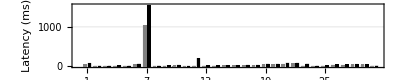
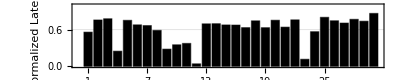
<|regular→-Graphics-,normalized→-Graphics-,data→<|machine→Tesla_K80,batchsize→1,recall→{42.368,4.35817,4.39137,5.1752,4.17021,39.3349,1034.4,3.73046,5.76783,10.2609,0.201625,8.4153,8.02256,8.13356,14.989,15.1,18.1478,20.7699,35.4943,41.2501,53.046,61.0273,6.93666,2.89929,8.50035,31.1311,27.8644,38.75,35.1463,7.9931},mxnet→{75.5819,5.7398,5.6361,20.7835,5.53477,57.8785,1549.27,6.33202,20.4117,29.0253,0.536156,199.549,11.5259,11.6467,22.1074,22.333,28.6189,27.875,56.0512,54.6427,82.5887,80.1747,59.3292,5.10807,10.5898,41.713,39.3133,50.3333,47.5512,9.22347}|>|>

```mathematica
Quiet[mkFig[machines[[1]],1]]
```

```mathematica
alldata=<||>;
Do[
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/recall_compare_models/batchsize_"<>ToString[batchSize]<>"/";
Quiet[CreateDirectory[targetDir]];
data=mkFig[machine,batchSize];
data["data"]= data["data"]/._Missing->0;
If[!KeyExistsQ[alldata,machine],
alldata[machine]=<||>
];
alldata[machine][batchSize]=data["data"];
json=Export[targetDir<>machine<>"_data.json", data["data"] ,"JSON"];
pdfNorm=Export[targetDir<>machine<>"_normalized.pdf",data["normalized"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>machine<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>machine<>"_regular.pdf",data["regular"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>machine<>"_regular.png",data["regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{batchSize,{1,2,4,8,16,32}},
{machine,machines}
]
;
```

```mathematica
alldataCache=;
```

```mathematica
getNorm[machine0_]:=Module[{machine=Association[machine0]},
Quiet[#["recall"]/#["mxnet"]]/.ComplexInfinity->Nothing&/@machine
]
```

```mathematica
getNorm/@alldata;
```

```mathematica
getGeoMean[machine0_]:=Module[{machine=Association[machine0]},
GeometricMean[Quiet[#["recall"]/#["mxnet"]]/.ComplexInfinity->Nothing]&/@machine
]
```

```mathematica
Values/@Values[getGeoMean/@alldata]
```

{{0.539291,0.59226,0.641383,0.486988,0.491496,0.904295},{0.61426,0.620601,0.645852,0.658381,0.615559,0.851803},{0.537243,0.556095,0.582924,0.619684,0.588972,0.611914},{0.698103,0.735016,0.763071,0.758594,0.710857,0.716137},{0.777075,0.771972,0.780322,0.76403,0.715562,0.704046},{0.738144,0.735171,0.788402,0.67729,0.630163,0.698845},{0.794143,0.79724,0.791706,0.678455,0.629083,0.688977}}

```mathematica
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]]
```

{{{1,0.539291},{2,0.59226},{4,0.641383},{8,0.486988},{16,0.491496},{32,0.904295}},{{1,0.61426},{2,0.620601},{4,0.645852},{8,0.658381},{16,0.615559},{32,0.851803}},{{1,0.537243},{2,0.556095},{4,0.582924},{8,0.619684},{16,0.588972},{32,0.611914}},{{1,0.698103},{2,0.735016},{4,0.763071},{8,0.758594},{16,0.710857},{32,0.716137}},{{1,0.777075},{2,0.771972},{4,0.780322},{8,0.76403},{16,0.715562},{32,0.704046}},{{1,0.738144},{2,0.735171},{4,0.788402},{8,0.67729},{16,0.630163},{32,0.698845}},{{1,0.794143},{2,0.79724},{4,0.791706},{8,0.678455},{16,0.629083},{32,0.688977}}}

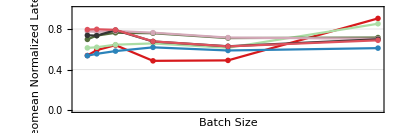

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
markers={Charting`CommonDump`GraphicsOpenPlotMarkers[],Charting`CommonDump`GraphicsOpenPlotMarkers[]};
ListPlot[
Map[Transpose[{batchSizes,#}]&,Values/@Values[getGeoMean/@alldata]],
ImageSize->Scaled[0.7],
Frame->True,
PlotRange->{0,1},
PlotMarkers->"OpenMarkers",
Joined->True,
PlotStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.33, 0.43, 0.23],RGBColor[0.8313725490196079, 0.6588235294117647, 0.72],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237],RGBColor[0.29411764705882354, 0.22745098039215686, 0.8200000000000001],RGBColor[0.79, 0.85, 0.3333333333333333]},
PlotTheme->{"Grid","LargeLabels"},
PlotLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,LegendMarkers->markers,Background->Opacity[0.5,LightGray],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.05,0.1},{0,0}}] ,
AspectRatio->1/3,
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
FrameLabel->{{Style["Geomean Normalized Latency",14],None},{Style["Batch Size",14],None}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
]
```

## ** Parallel MXNet ResNet50 Times vs Our Recall for website

```mathematica
mkFig[modelName_]:=Module[{},
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB"];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[#["name"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&]["mean_time"]&,data];
fig=BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{Gray,Black},
PlotTheme->"Grid",
ChartLegends->{Placed[SwatchLegend[{Gray,Black},Style[#,Black,FontSize->14]&/@{"Parallel", "MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->14,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],None},
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Time for Recall and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
Lookup[ourdata,batchSizes]/Lookup[mxnetdata,batchSizes],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Keys[data]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->{0,1},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Batch Size",14],None(*modelName<>" Normalized Time (Recall/MXNet)"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"regular"->fig,
"normalized"->nfig,
"data"-><|"recall"->ourdata,"mxnet"->mxnetdata|>
|>
]
```

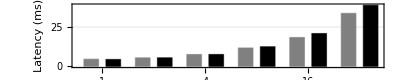
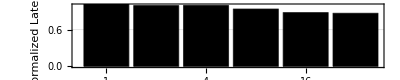
<|regular→-Graphics-,normalized→-Graphics-,data→<|recall→<|1→4.57603,2→5.42476,4→7.54196,8→11.6923,16→18.3468,32→33.6826|>,mxnet→<|1→4.40854,2→5.45624,4→7.56913,8→12.4722,16→20.8663,32→38.8146|>|>|>

```mathematica
mkFig["ResNet050-v1"]
```

```mathematica
ourdata
```

<|1→1.25382,2→1.36458,4→1.81753,8→2.85355,16→3.96189,32→6.22883|>

```mathematica
mxnetdata
```

<|1→1.47045,2→0.00149989,4→0.00212646,8→0.00373983,16→0.00535154,32→0.00897622|>

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/recall_compare/figures/";
Quiet[CreateDirectory[targetDir]];
figs=Table[
data=mkFig[modelName];
json=Export[targetDir<>modelName<>"_data.json",Map[KeyMap[ToString,#]&,DeleteMissing[data["data"],Infinity]] ,"JSON"];
pdfNorm=Export[targetDir<>modelName<>"_normalized.pdf",data["normalized"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>modelName<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>modelName<>"_regular.pdf",data["regular"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>modelName<>"_regular.png",data["regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{modelName,modelNames}
(*{modelName,{"DUC"}}*)
];
```

Export::jsonstrictencoding: Expression Missing cannot be exported as JSON.

```mathematica
figs=Association[figs];
```

```mathematica
Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/recall_compare/info.json",figs/.$Failed->""];
```

```mathematica
tmpl=StringTemplate["
{{< lightbox src=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`PNG`\" centered=\"true\" width=\"80%\" >}}

<div class=\"right-buttons flex justify-end\">
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`PDF`\">}}PDF{{< /button >}}
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`JSON`\">}}JSON{{< /button >}}
</div>"];
StringRiffle[
Table[
elem=figs[model];
StringJoin[{
"\n\n## ",
model ,
"\n\n",
"We compare our recall time vs MXNet for the "<>model<> " on a Tesla V100-SXM2-16GB\n",
"\n\n### Time ",
TemplateApply[
tmpl,
<|
"PDF"->FileNameTake[elem["pdfReg"]],
"PNG"->FileNameTake[elem["pngReg"]],
"JSON"->FileNameTake[elem["json"]]
|>
],
"\n\n### Normalized Time ",
TemplateApply[
tmpl,
<|
"PDF"->FileNameTake[elem["pdfNorm"]],
"PNG"->FileNameTake[elem["pngNorm"]],
"JSON"->FileNameTake[elem["json"]]
|>
]
}],
{model,Keys[figs]}
],
"\n"
]//CopyToClipboard
```

## ** Sequential MXNet Times vs Our Recall for website

```mathematica
mkFig[modelName_]:=Module[{},
batchSizes=2^Range[0,5];
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter...:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
ourdata=data;
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet/Tesla_V100-SXM2-16GB"];
ClearAll[getBatchSize];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","batchsize","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=KeySort[Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}]];
mxnetdata=Map[SelectFirst[#,ToLowerCase[#["name"]]===ToLowerCase[modelName]||ToLowerCase[#["name"]]===ToLowerCase[StringReplace[modelName,"-"->"_"]]&]["mean_time"]&,data];
fig=BarChart[
Transpose[{Lookup[ourdata,batchSizes],Lookup[mxnetdata,batchSizes]}],
ChartStyle->{Gray,Black},
PlotTheme->"Grid",
ChartLegends->{Placed[SwatchLegend[{Gray,Black},Style[#,Black,FontSize->14]&/@{"Sequential", "MXNet"},Background->Opacity[0.5,White],LegendMarkerSize->14,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],None},
ChartLabels->{(Style[#,Black]&/@Keys[data]),None},
ImageSize->Scaled[1],
BarSpacing->{0.5,1},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Time for Recall and MXNet"*)}},
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
nfig=BarChart[
Lookup[ourdata,batchSizes]/Lookup[mxnetdata,batchSizes],
PlotTheme->"Grid",
ChartStyle->Black,
ChartLabels->(Style[#,Black]&/@Keys[data]),
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
PlotRange->{0,1},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
AspectRatio->1/5,
Frame->True,
FrameLabel->{{Style["Normalized Latency",14],None},{Style["Batch Size",14],None(*modelName<>" Normalized Time (Recall/MXNet)"*)}},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
<|
"regular"->fig,
"normalized"->nfig,
"data"-><|"recall"->ourdata,"mxnet"->mxnetdata|>
|>
]
```

```mathematica
mkFig["ResNet050-v1"]
```

<|regular→-Graphics-,normalized→-Graphics-,data→<|recall→<|1→4.57603,2→5.42476,4→7.54196,8→11.6923,16→18.3468,32→33.6826|>,mxnet→<|1→4.40854,2→5.45624,4→7.56913,8→12.4722,16→20.8663,32→38.8146|>|>|>

```mathematica
ourdata
```

<|1→1.25382,2→1.36458,4→1.81753,8→2.85355,16→3.96189,32→6.22883|>

```mathematica
mxnetdata
```

<|1→1.47045,2→0.00149989,4→0.00212646,8→0.00373983,16→0.00535154,32→0.00897622|>

```mathematica
modelNames={"ArcFace","BVLC_AlexNet","BVLC_CaffeNet","BVLC_GoogleNet","BVLC_RCNN_ILSVRC13","DenseNet-121","DUC","Emotion-FerPlus","Inception-v1","Inception-v2","MNIST","MobileNet-v2","ResNet018-v1","ResNet018-v2","ResNet034-v1","ResNet034-v2","ResNet050-v1","ResNet050-v2","ResNet101-v1","ResNet101-v2","ResNet152-v1","ResNet152-v2","Shufflenet","Squeezenet-v1.1","Tiny_YOLO-v2","VGG16-BN","VGG16","VGG19-BN","VGG19","Zfnet512"};
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/sequential_recall_compare/figures/";
Quiet[CreateDirectory[targetDir]];
figs=Table[
data=mkFig[modelName];
json=Export[targetDir<>modelName<>"_data.json",Map[KeyMap[ToString,#]&,DeleteMissing[data["data"],Infinity]] ,"JSON"];
pdfNorm=Export[targetDir<>modelName<>"_normalized.pdf",data["normalized"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngNorm=Export[targetDir<>modelName<>"_normalized.png",Magnify[ data["normalized"],0.8],"PNG","CompressionLevel"->0,ImageResolution->100];
pdfReg=Export[targetDir<>modelName<>"_regular.pdf",data["regular"],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
pngReg=Export[targetDir<>modelName<>"_regular.png",data["regular"],"PNG","CompressionLevel"->0,ImageResolution->100];
modelName-><|"json"->json,"pdfNorm"->pdfNorm,"pdfReg"->pdfReg,"pngNorm"->pngNorm,"pngReg"->pngReg|>
,
{modelName,modelNames}
(*{modelName,{"DUC"}}*)
];
```

Export::jsonstrictencoding: Expression Missing cannot be exported as JSON.

```mathematica
figs=Association[figs];
```

```mathematica
Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/recall_compare/info.json",figs/.$Failed->""];
```

```mathematica
tmpl=StringTemplate["
{{< lightbox src=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`PNG`\" centered=\"true\" width=\"80%\" >}}

<div class=\"right-buttons flex justify-end\">
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`PDF`\">}}PDF{{< /button >}}
{{< button href=\"https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/recall_compare/figures/`JSON`\">}}JSON{{< /button >}}
</div>"];
StringRiffle[
Table[
elem=figs[model];
StringJoin[{
"\n\n## ",
model ,
"\n\n",
"We compare our recall time vs MXNet for the "<>model<> " on a Tesla V100-SXM2-16GB\n",
"\n\n### Time ",
TemplateApply[
tmpl,
<|
"PDF"->FileNameTake[elem["pdfReg"]],
"PNG"->FileNameTake[elem["pngReg"]],
"JSON"->FileNameTake[elem["json"]]
|>
],
"\n\n### Normalized Time ",
TemplateApply[
tmpl,
<|
"PDF"->FileNameTake[elem["pdfNorm"]],
"PNG"->FileNameTake[elem["pngNorm"]],
"JSON"->FileNameTake[elem["json"]]
|>
]
}],
{model,Keys[figs]}
],
"\n"
]//CopyToClipboard
```

## Our ResNet50 Recall Times V100

```mathematica
files=FileNames["batchsize_*/Tesla_V100-SXM2-16GB/ResNet050-v1.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Association@Table[xgetBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[First@Lookup[Select[#,#["BenchmarkName"]==="Total"&],"RealTime(ms)"]&/@data];
data=KeySelect[data,#≤32&];
```

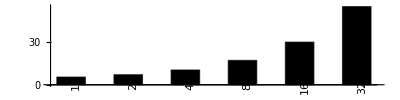

```mathematica
BarChart[
Values[data],
ChartStyle->Black,
ChartLabels->(Style[Rotate[#,90Degree],Black]&/@Keys[data]),
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{1,1}
]
```

## MXNet ResNet50 Times

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet"];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}];
data=KeySort[SortBy[KeyDrop[#,"times"],#["id"]&]&/@data];
data=SelectFirst[#,#["name"]==="ResNet050-v1"&]["mean_time"]&/@data;
```

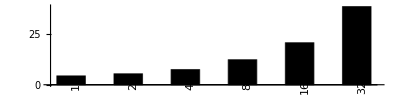

```mathematica
BarChart[
Values[data],
ChartStyle->Black,
ChartLabels->(Style[Rotate[#,90Degree],Black]&/@Keys[data]),
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{1,1}
]
```

## Analysis Scratch

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/32.json";
data=Import[file,"RawJSON"];
data=data["benchmarks"];
```

```mathematica
row=Select[data,StringContainsQ[#["name"],"40800378504431"]&];
names=Map[First@StringCases[#,___~~"<"~~x__~~">"~~___:>x]&,Lookup[row,"name"]];
times=Lookup[row,"real_time"];
SortBy[Thread[List[names,times]],Last]
```

{{CUDNN_CONVOLUTION_FWD_ALGO_DIRECT,0.},{CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD,394156.},{CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD_NONFUSED,425883.},{CUDNN_CONVOLUTION_FWD_ALGO_FFT_TILING,498121.},{CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_PRECOMP_GEMM,672187.},{CUDNN_CONVOLUTION_FWD_ALGO_FFT,830074.},{CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM,884950.},{CUDNN_CONVOLUTION_FWD_ALGO_GEMM,1.45868×10^6}}

## Plot our recall time ResNet50-v1 V100

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_32/Tesla_V100-SXM2-16GB/ResNet050-v1.csv","CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
```

```mathematica
Map[Total[Lookup[#,"RealTime(ms)"]]&,GroupBy[data,#["LayerType"]&]]
```

<|Conv→42.4615,BatchNorm→6.19488,Relu→3.42727,Pooling→0.226463,ElementWise→2.71887,Gemm→0.04474|>

```mathematica
Total[Lookup[Select[data,#["LayerType"]==="ElementWise"&],"RealTime(ms)"]]/Total[Lookup[data,"RealTime(ms)"]]
```

```mathematica
Total[Lookup[Select[data,#["LayerType"]==="ElementWise"&],"RealTime(ms)"]]/Total[Lookup[data,"RealTime(ms)"]]
```

0.0477555

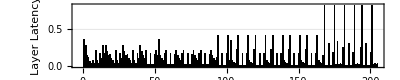

```mathematica
fig=BarChart[
MapThread[Tooltip,{Lookup[data,"RealTime(ms)"],Lookup[data,"LayerName"]}],
PlotTheme->"Grid",
AspectRatio->1/5,
ChartStyle->Black,
Frame->True,
BarSpacing->{1,1},
FrameLabel->{Style["Layer Index",14],Style["Layer Latency",14]},
ImageSize->Scaled[0.75]
]
```

```mathematica
prevCell=NotebookRead[PreviousCell[]]/.HoldPattern[CellLabel->_]->Sequence[];
{
CloudExport[prevCell,"PNG",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"],
CloudExport[Notebook[{prevCell},Editable->False,WindowSize->Scaled[1]],"NB",ImageResolution->500,ImageSize->500,Permissions->"Public",CloudObjectURLType->"Object"]
}
```

{CloudObject[https://www.wolframcloud.com/obj/18744229-b1bb-49a7-9a2c-f470844e3136],CloudObject[https://www.wolframcloud.com/obj/79f6dc0d-c5cb-4832-ad91-1142038d0b61]}

```mathematica
Dataset[data]
```

## Plot our recall time For All Models / Machine / Batches for website [half prec]

```mathematica
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
getModelName[fileName_]:=FileBaseName[fileName]
```

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency_float16/batchsize_*",Infinity];
```

```mathematica
mkPlot[fileName_]:=Module[{},
data=raw=Import[fileName,"CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
modelName=getModelName[fileName];
machineName=getMachine[fileName];
batchSize=xgetBatchSize[fileName];
baseDir=FileNameJoin[{
"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/float16_model_info/figures/",
modelName,
machineName,
ToString[batchSize]
}];
Quiet[CreateDirectory[baseDir]];
fig=BarChart[
MapThread[Tooltip,data={Lookup[data,"RealTime(ms)"],Lookup[data,"LayerName"]}],
PlotTheme->"Grid",
AspectRatio->1/5,
ChartStyle->Black,
Frame->True,
BarSpacing->Medium,
ChartLabels->Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[data]],UpTo[20]]],1],
FrameLabel->{{Style["Latency",6],None},{Style["Layer Index",6],Style[modelName<>" running on fp16 "<>machineName <> " using batch size "<> ToString[batchSize],8]}},
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.2],GrayLevel[0]],
PlotRange->All,
FrameTicks->{{True,None},{True,None}},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->6},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->6}
];
csv=Export[baseDir<>"/"<>modelName<>"_latency.csv",raw,"CSV"];
pdf=Export[baseDir<>"/"<>modelName<>"_latency.pdf",Magnify[fig,3],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[baseDir<>"/"<>modelName<>"_latency.png",Magnify[fig,2],"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
<|"png"->png,"csv"->csv,"pdf"->pdf,"modlName"->modelName,"machineName"->machineName,"batchSize"->batchSize|>
];
```

```mathematica
info=mkPlot/@files;
```

```mathematica
Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/info.json",info];
```

## Plot our recall time For All Models / Machine / Batches for website [also model page generator]

```mathematica
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
getModelName[fileName_]:=FileBaseName[fileName]
```

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_*",Infinity];
```

```mathematica
mkPlot[fileName_]:=Module[{},
data=raw=Import[fileName,"CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
modelName=getModelName[fileName];
machineName=getMachine[fileName];
batchSize=xgetBatchSize[fileName];
baseDir=FileNameJoin[{
"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/model_info/figures/",
modelName,
machineName,
ToString[batchSize]
}];
Quiet[CreateDirectory[baseDir]];
fig=BarChart[
MapThread[Tooltip,data={Lookup[data,"RealTime(ms)"],Lookup[data,"LayerName"]}],
PlotTheme->"Grid",
AspectRatio->1/5,
ChartStyle->Black,
Frame->True,
BarSpacing->Medium,
ChartLabels->Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[data]],UpTo[20]]],1],
FrameLabel->{{Style["Latency",6],None},{Style["Layer Index",6],Style[modelName<>" running on "<>machineName <> " using batch size "<> ToString[batchSize],8]}},
ImageSize->Scaled[1],
FrameStyle->Directive[AbsoluteThickness[0.2],GrayLevel[0]],
PlotRange->All,
FrameTicks->{{True,None},{True,None}},
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->6},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->6}
];
csv=Export[baseDir<>"/"<>modelName<>"_latency.csv",raw,"CSV"];
pdf=Export[baseDir<>"/"<>modelName<>"_latency.pdf",Magnify[fig,3],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[baseDir<>"/"<>modelName<>"_latency.png",Magnify[fig,2],"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
<|"png"->png,"csv"->csv,"pdf"->pdf,"modlName"->modelName,"machineName"->machineName,"batchSize"->batchSize|>
];
```

```mathematica
info=mkPlot/@files;
```

```mathematica
Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/model_info/info.json",info];
```

### Create model pages

```mathematica
Keys[metadata[[1]]]
```

{png,csv,pdf,modlName,machineName,batchSize}

```mathematica
metadata=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/model_info/info.json","RAWJSON"];
metadata=Map[Append[#,"modelName"->#["modlName"]]&,metadata];
pathPrefix="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/model_info/";
baseAWSURL="https://s3.amazonaws.com/store.carml.org/dlperf/website/assets/model_info/model_info/";
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/content/docs/models";
mainTmpl=FileTemplate["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/content/docs/models/templates/main_template.tmpl"];
machineLayerTmpl=FileTemplate["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/content/docs/models/templates/machine_layer_timing.tmpl"];
machineBatchTmpl=FileTemplate["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/content/docs/models/templates/machine_batch_timing.tmpl"];
```

```mathematica
mkPngURL[e_]:=baseAWSURL<>StringTrim[e["png"],pathPrefix]
mkCSVURL[e_]:=baseAWSURL<>StringTrim[e["csv"],pathPrefix]
mkPDFURL[e_]:=baseAWSURL<>StringTrim[e["pdf"],pathPrefix]
mkOutputPath[e_?StringQ]:=FileNameJoin[{targetDir,e<>".md"}];
mkOutputPath[e_?AssociationQ]:=mkOutputPath[e["modelName"]];
batchSizes=2^Range[5];
modelInfos=KeySort[GroupBy[metadata,#modlName&]];
models=Keys[modelInfos];
machines={"Tesla_K80","Tesla_M60","GRID_K520","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
mkData[model_,machine_,batchSize_]:=
Module[{rec=SelectFirst[metadata,#["modelName"]===model&&#["machineName"]===machine&&#["batchSize"]===batchSize&]},
TemplateApply[
machineBatchTmpl,
<|
"BatchSize"->batchSize,
"PNGURL"->mkPngURL[rec],
"CSVURL"->mkCSVURL[rec],
"PDFURL"->mkPDFURL[rec]
|>
]
];
mkData[model_,machine_]:=
Module[{r=StringRiffle[Table[mkData[model,machine,batchSize],{batchSize,batchSizes}],"\n"]},
TemplateApply[
machineLayerTmpl,
<|
"MachineName"->StringReplace[machine,"_"->" "],
"MachineBatchTiming"->r
|>
]
]
mkData[model_]:=
Module[{r=StringRiffle[Table[mkData[model,machine],{machine,machines}],"\n"]},
TemplateApply[
mainTmpl,
<|
"ModelIndex"->First[FirstPosition[models,model]],
"ModelName"->StringReplace[model,"_"->" "],
"MachineLayerTiming"->r
|>
]
]
```

```mathematica
Do[
Export[ mkOutputPath[model],mkData[model],"Text"],
{model,models}
]
```

```mathematica
tmpl=StringTemplate["  - [`m`]({{< relref \"/docs/models/`m`\" >}})"];
e=StringRiffle[Table[TemplateApply[tmpl,<|"m"->m|>],{m,models}],"\n"]
CopyToClipboard[e]
```

- [ArcFace]({{< relref "/docs/models/ArcFace" >}})
  - [BVLC_AlexNet]({{< relref "/docs/models/BVLC_AlexNet" >}})
  - [BVLC_CaffeNet]({{< relref "/docs/models/BVLC_CaffeNet" >}})
  - [BVLC_GoogleNet]({{< relref "/docs/models/BVLC_GoogleNet" >}})
  - [BVLC_RCNN_ILSVRC13]({{< relref "/docs/models/BVLC_RCNN_ILSVRC13" >}})
  - [DenseNet-121]({{< relref "/docs/models/DenseNet-121" >}})
  - [DUC]({{< relref "/docs/models/DUC" >}})
  - [Emotion-FerPlus]({{< relref "/docs/models/Emotion-FerPlus" >}})
  - [Inception-v1]({{< relref "/docs/models/Inception-v1" >}})
  - [Inception-v2]({{< relref "/docs/models/Inception-v2" >}})
  - [MNIST]({{< relref "/docs/models/MNIST" >}})
  - [MobileNet-v2]({{< relref "/docs/models/MobileNet-v2" >}})
  - [ResNet018-v1]({{< relref "/docs/models/ResNet018-v1" >}})
  - [ResNet018-v2]({{< relref "/docs/models/ResNet018-v2" >}})
  - [ResNet034-v1]({{< relref "/docs/models/ResNet034-v1" >}})
  - [ResNet034-v2]({{< relref "/docs/models/ResNet034-v2" >}})
  - [ResNet050-v1]({{< relref "/docs/models/ResNet050-v1" >}})
  - [ResNet050-v2]({{< relref "/docs/models/ResNet050-v2" >}})
  - [ResNet101-v1]({{< relref "/docs/models/ResNet101-v1" >}})
  - [ResNet101-v2]({{< relref "/docs/models/ResNet101-v2" >}})
  - [ResNet152-v1]({{< relref "/docs/models/ResNet152-v1" >}})
  - [ResNet152-v2]({{< relref "/docs/models/ResNet152-v2" >}})
  - [Shufflenet]({{< relref "/docs/models/Shufflenet" >}})
  - [Squeezenet-v1.1]({{< relref "/docs/models/Squeezenet-v1.1" >}})
  - [Tiny_YOLO-v2]({{< relref "/docs/models/Tiny_YOLO-v2" >}})
  - [VGG16]({{< relref "/docs/models/VGG16" >}})
  - [VGG16-BN]({{< relref "/docs/models/VGG16-BN" >}})
  - [VGG19]({{< relref "/docs/models/VGG19" >}})
  - [VGG19-BN]({{< relref "/docs/models/VGG19-BN" >}})
  - [Zfnet512]({{< relref "/docs/models/Zfnet512" >}})

## Plot our total recall time for all batch_sizes/machines using ResNet50-v1

```mathematica
modelName="ResNet050-v1";
files=FileNames["batchsize_*/*/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(xgetBatchSize[file]->row),
{file,files}
];
data=Merge[data,Association];
data=Map[KeySort,data];
```

```mathematica
machines={"Tesla_K80","Tesla_M60","GRID_K520","TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
```

```mathematica
Keys[data]
```

{GRID_K520,Quadro_RTX_6000,Tesla_K80,Tesla_M60,Tesla_T4,Tesla_V100-SXM2-16GB,TITAN_V,TITAN_Xp}

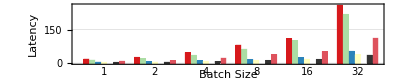

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
batchSizes={1,2,4,8,16,32};
fig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency",14],None},{Style["Batch Size",14],modelName<>" Latency Across Systems"}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->10]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->8]&/@machines,Background->Opacity[0.0,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
]
```

```mathematica
prevCell=NotebookRead[PreviousCell[]]/.HoldPattern[CellLabel->_]->Sequence[];
{
CloudExport[prevCell,"PNG",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"],
CloudExport[Notebook[{prevCell},Editable->False,WindowSize->Scaled[1]],"NB",ImageResolution->500,ImageSize->500,Permissions->"Public",CloudObjectURLType->"Object"]
}
```

{CloudObject[https://www.wolframcloud.com/obj/d82b4c30-0832-4ab8-8a93-d8dbf834fb08],CloudObject[https://www.wolframcloud.com/obj/5e4bcc76-83fe-4386-b454-f99b913ffc87]}

## **Plot our total serial recall time (with cudnn advised) for all batch_sizes/machines/models for website

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
mkFig[modelName_]:=Module[{},files=FileNames["batchsize_*/*/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/cudnn_advised_serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(xgetBatchSize[file]->row),
{file,files}
];
data=Merge[data,Association];
data=Map[KeySort,data];
machines={"Tesla_K80","Tesla_M60",(*"GRID_K520",*)"TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
batchSizes={1,2,4,8,16,32};
fig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
lfig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
ScalingFunctions->"Log",
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.01,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/cudnn_advised_serial_latency/figures/";
Quiet[CreateDirectory[targetDir]];
json=Export[targetDir<>modelName<>"_serial_advised_latency.json",Map[KeyMap[ToString,#]&,data],"JSON"];
pdf=Export[targetDir<>modelName<>"_serial_advised_latency_log_scaled.pdf",lfig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>modelName<>"_serial_advised_latency_log_scaled.png",lfig,"PNG","CompressionLevel"->0,ImageResolution->100];
pdf=Export[targetDir<>modelName<>"_serial_advised_latency.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>modelName<>"_serial_advised_latency.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
modelName-><|"png"->png,"json"->json,"pdf"->pdf|>
]
```

```mathematica
modelNames = Union[FileBaseName/@FileNames["batchsize_*/*/*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"]];
```

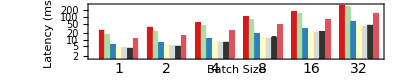

```mathematica
mkFig[modelNames[[17]]];
lfig
```

```mathematica
figs=mkFig/@modelNames;
```

## **Plot our total serial recall time for all batch_sizes/machines/models for website

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
mkFig[modelName_]:=Module[{},files=FileNames["batchsize_*/*/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(xgetBatchSize[file]->row),
{file,files}
];
data=Merge[data,Association];
data=Map[KeySort,data];
machines={"Tesla_K80","Tesla_M60",(*"GRID_K520",*)"TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
batchSizes={1,2,4,8,16,32};
fig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
lfig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[0.85],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ScalingFunctions->"Log",
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.01,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency/figures/";
Quiet[CreateDirectory[targetDir]];
json=Export[targetDir<>modelName<>"_serial_latency.json",Map[KeyMap[ToString,#]&,data],"JSON"];
pdf=Export[targetDir<>modelName<>"_serial_latency.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>modelName<>"_serial_latency.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
pdf=Export[targetDir<>modelName<>"_serial_latency_log_scaled.pdf",lfig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>modelName<>"_serial_latency_log_scaled.png",lfig,"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
modelName-><|"png"->png,"json"->json,"pdf"->pdf|>
]
```

```mathematica
modelNames = Union[FileBaseName/@FileNames["batchsize_*/*/*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"]];
```

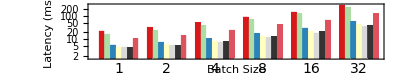

```mathematica
mkFig[modelNames[[17]]];
lfig
```

```mathematica
figs=mkFig/@modelNames;
```

## **Plot our total half precision recall time for all batch_sizes/machines/models for website

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
mkFig[modelName_]:=Module[{},files=FileNames["batchsize_*/*/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency_float16"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(xgetBatchSize[file]->row),
{file,files}
];
data=Merge[data,Association];
data=Map[KeySort,data];
machines={"TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
batchSizes={1,2,4,8,16,32};
fig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
lfig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
ScalingFunctions->"Log",
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
Quiet[CreateDirectory["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"]];
json=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"<>modelName<>"_latency.json",Map[KeyMap[ToString,#]&,data],"JSON"];
pdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"<>modelName<>"_latency_log_scaled.pdf",lfig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"<>modelName<>"_latency_log_scaled.png",lfig,"PNG","CompressionLevel"->0,ImageResolution->100];
pdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"<>modelName<>"_latency.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/serial_latency_float16/figures/"<>modelName<>"_latency.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
modelName-><|"png"->png,"json"->json,"pdf"->pdf|>
]
```

```mathematica
modelNames = Union[FileBaseName/@FileNames["batchsize_*/*/*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/serial_latency_float16"]];
```

```mathematica
figs=mkFig/@modelNames;
```

## **Plot our total recall time for all batch_sizes/machines/models for website

```mathematica
prettyName["Tesla_V100-SXM2-16GB"]="Tesla_V100";
prettyName["Quadro_RTX_6000"]="Quadro_RTX";
prettyName[x_]:=x
mkFig[modelName_]:=Module[{},files=FileNames["batchsize_*/*/"<>modelName<>".csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"];
xgetBatchSize[fileName_]:=
With[{bn=fileName},
ToExpression[First[StringCases[bn,___~~"batchsize_"~~d:DigitCharacter..~~__:>d]]]
];
getMachine[fileName_]:=
With[{bn=fileName},
First[StringCases[bn,___~~"batchsize_"~~DigitCharacter..~~"/"~~Shortest[name__]~~"/"~~__:>name]]
];
addHeader[rows_]:=AssociationThread[First[rows]->#]&/@Select[Rest[rows],Length[#]=!={}&];
data=raw=Table[
e=addHeader[Import[file]];
row=First@Lookup[Select[e,#["BenchmarkName"]==="Total"&],"RealTime(ms)"];
getMachine[file]->(xgetBatchSize[file]->row),
{file,files}
];
data=Merge[data,Association];
data=Map[KeySort,data];
machines={"Tesla_K80","Tesla_M60",(*"GRID_K520",*)"TITAN_Xp","TITAN_V","Tesla_V100-SXM2-16GB","Quadro_RTX_6000","Tesla_T4"};
batchSizes={1,2,4,8,16,32};
fig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
lfig=BarChart[
Transpose[Lookup[Lookup[data,machines],batchSizes]],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608],RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[1., 1., 0.7490196078431373],GrayLevel[1],RGBColor[0.2, 0.2, 0.2],RGBColor[0.87, 0.3215686274509804, 0.36470588235294116],RGBColor[0.9372549019607843, 0.5803921568627451, 0.12941176470588237]},
BarSpacing->{0.2,2},
ScalingFunctions->"Log",
FrameLabel->{{Style["Latency (ms)",14],None},{Style["Batch Size",14],None(*modelName<>" Latency Across Systems"*)}},
ImageSize->Scaled[0.75],
ChartLabels->{Placed[Style[#,Black,FontSize->14]&/@batchSizes,Below],None},
ChartLegends->Placed[SwatchLegend[Style[prettyName[#],Black,FontSize->14]&/@machines,Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",2}],{{0.03,0.67},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->18}
];
json=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/latency/figures/"<>modelName<>"_latency.json",Map[KeyMap[ToString,#]&,data],"JSON"];
pdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/latency/figures/"<>modelName<>"_latency_log_scaled.pdf",lfig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/latency/figures/"<>modelName<>"_latency_log_scaled.png",lfig,"PNG","CompressionLevel"->0,ImageResolution->100];
pdf=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/latency/figures/"<>modelName<>"_latency.pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/latency/figures/"<>modelName<>"_latency.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
(*fig=CloudExport[fig,"PNG",modelName<>"_latency.png",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"];*)
modelName-><|"png"->png,"json"->json,"pdf"->pdf|>
]
```

```mathematica
modelNames = Union[FileBaseName/@FileNames["batchsize_*/*/*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency"]];
```

```mathematica
figs=mkFig/@modelNames;
```

### Make All URLs

```mathematica
ClearAll[mkURL];
mkParallelUrl[base_]:="\"/assets/latency/figures/"<>base<>"\""
mkSerialUrl[base_]:="\"/assets/serial_latency/figures/"<>StringReplace[base,"_latency"->"_serial_latency"]<>"\""
mkCUDNNSerialUrl[base_]:="\"/assets/cudnn_advised_serial_latency/figures/"<>StringReplace[base,"_latency"->"_serial_advised_latency"]<>"\""
mkParallelLogUrl[base_]:="\"/assets/latency/figures/"<>StringReplace[base,".pdf"->"_log_scaled.pdf"]<>"\""
mkSerialLogUrl[base_]:="\"/assets/serial_latency/figures/"<>StringReplace[base,"_latency."->"_serial_latency_log_scaled."]<>"\""
mkId[base_]:=ToString[Hash[base]]
mkCUDNNSerialLogUrl[base_]:="\"/assets/cudnn_advised_serial_latency/figures/"<>StringReplace[base,"_latency"->"_serial_advised_latency_log_scaled"]<>"\""
figsToMarkdown[name_->url_]:="## **"<>StringReplace[name,"_"->" "] <> "** Model\n\n"<>
"## Parallel Recall\n\n"<>
"{{< tabs \""<>mkId[name<>"parallel"]<>"\" >}}\n"<>
"{{< tab \"Linear\" >}}\n"<>
"\n{{< lightbox src="<>mkParallelUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkParallelUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkParallelUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n"<>
"{{< tab \"Log\" >}}\n"<>
"\n\n{{< lightbox src="<>mkParallelLogUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkParallelLogUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkParallelUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n{{< /tabs >}}\n\n"<>

"## Serial Recall\n"<>
"{{< tabs \""<>mkId[name<>"serial_recall"]<>"\" >}}\n"<>
"{{< tab \"Linear\" >}}\n"<>
"\n{{< lightbox src="<>mkSerialUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkSerialUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkSerialUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n"<>
"{{< tab \"Log\" >}}\n"<>
"\n\n{{< lightbox src="<>mkSerialLogUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkSerialLogUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkSerialUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n{{< /tabs >}}\n\n"<>

"## Serial Recall using CUDNN Advised Algorithm\n"<>
"{{< tabs \""<>mkId[name<>"serial_cudnn"]<>"\" >}}\n"<>
"{{< tab \"Linear\" >}}\n"<>
"\n{{< lightbox src="<>mkCUDNNSerialUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkCUDNNSerialUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkCUDNNSerialUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n"<>
"{{< tab \"Log\" >}}\n"<>
"\n\n{{< lightbox src="<>mkCUDNNSerialLogUrl[FileBaseName[url["png"]]<>".png"]<>" centered=\"true\" width=\"80%\" >}} \n\n<div class=\"right-buttons flex justify-end\">\n{{< button href="<>mkCUDNNSerialLogUrl[FileBaseName[url["pdf"]]<>".pdf"]<>">}}PDF{{< /button >}}\n{{< button href="<>mkCUDNNSerialUrl[FileBaseName[url["json"]]<>".json"]<>">}}JSON{{< /button >}}\n</div>\n\n"<>
"{{< /tab >}}\n{{< /tabs >}}\n\n"
figsToMarkdown[lst_?ListQ]:=StringRiffle[figsToMarkdown /@ lst,"\n\n\n"]
```

```mathematica
figsToMarkdown[figs[[1]]]
```

## **ArcFace** Model

## Parallel Recall

{{< tabs "6335679192985034037" >}}
{{< tab "Linear" >}}

{{< lightbox src="/assets/latency/figures/ArcFace_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ArcFace_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ArcFace_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< tab "Log" >}}


{{< lightbox src="/assets/latency/figures/ArcFace_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ArcFace_latency_log_scaled.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ArcFace_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< /tabs >}}

## Serial Recall
{{< tabs "7640013931940632678" >}}
{{< tab "Linear" >}}

{{< lightbox src="/assets/serial_latency/figures/ArcFace_serial_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/serial_latency/figures/ArcFace_serial_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/serial_latency/figures/ArcFace_serial_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< tab "Log" >}}


{{< lightbox src="/assets/serial_latency/figures/ArcFace_serial_latency_log_scaled.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/serial_latency/figures/ArcFace_serial_latency_log_scaled.pdf">}}PDF{{< /button >}}
{{< button href="/assets/serial_latency/figures/ArcFace_serial_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< /tabs >}}

## Serial Recall using CUDNN Advised Algorithm
{{< tabs "2903605466313392201" >}}
{{< tab "Linear" >}}

{{< lightbox src="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< tab "Log" >}}


{{< lightbox src="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency_log_scaled.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency_log_scaled.pdf">}}PDF{{< /button >}}
{{< button href="/assets/cudnn_advised_serial_latency/figures/ArcFace_serial_advised_latency.json">}}JSON{{< /button >}}
</div>

{{< /tab >}}
{{< /tabs >}}

```mathematica
figsToMarkdown[figs]//CopyToClipboard
```

```mathematica
figsToMarkdown[figs]
```

## **ArcFace** 

{{< lightbox src="/assets/latency/figures/ArcFace_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ArcFace_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ArcFace_latency.json">}}JSON{{< /button >}}
</div>


## **BVLC AlexNet** 

{{< lightbox src="/assets/latency/figures/BVLC_AlexNet_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/BVLC_AlexNet_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/BVLC_AlexNet_latency.json">}}JSON{{< /button >}}
</div>


## **BVLC CaffeNet** 

{{< lightbox src="/assets/latency/figures/BVLC_CaffeNet_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/BVLC_CaffeNet_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/BVLC_CaffeNet_latency.json">}}JSON{{< /button >}}
</div>


## **BVLC GoogleNet** 

{{< lightbox src="/assets/latency/figures/BVLC_GoogleNet_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/BVLC_GoogleNet_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/BVLC_GoogleNet_latency.json">}}JSON{{< /button >}}
</div>


## **BVLC RCNN ILSVRC13** 

{{< lightbox src="/assets/latency/figures/BVLC_RCNN_ILSVRC13_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/BVLC_RCNN_ILSVRC13_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/BVLC_RCNN_ILSVRC13_latency.json">}}JSON{{< /button >}}
</div>


## **DenseNet-121** 

{{< lightbox src="/assets/latency/figures/DenseNet-121_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/DenseNet-121_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/DenseNet-121_latency.json">}}JSON{{< /button >}}
</div>


## **DUC** 

{{< lightbox src="/assets/latency/figures/DUC_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/DUC_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/DUC_latency.json">}}JSON{{< /button >}}
</div>


## **Emotion-FerPlus** 

{{< lightbox src="/assets/latency/figures/Emotion-FerPlus_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Emotion-FerPlus_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Emotion-FerPlus_latency.json">}}JSON{{< /button >}}
</div>


## **Inception-v1** 

{{< lightbox src="/assets/latency/figures/Inception-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Inception-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Inception-v1_latency.json">}}JSON{{< /button >}}
</div>


## **Inception-v2** 

{{< lightbox src="/assets/latency/figures/Inception-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Inception-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Inception-v2_latency.json">}}JSON{{< /button >}}
</div>


## **MNIST** 

{{< lightbox src="/assets/latency/figures/MNIST_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/MNIST_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/MNIST_latency.json">}}JSON{{< /button >}}
</div>


## **MobileNet-v2** 

{{< lightbox src="/assets/latency/figures/MobileNet-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/MobileNet-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/MobileNet-v2_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet018-v1** 

{{< lightbox src="/assets/latency/figures/ResNet018-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet018-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet018-v1_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet018-v2** 

{{< lightbox src="/assets/latency/figures/ResNet018-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet018-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet018-v2_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet034-v1** 

{{< lightbox src="/assets/latency/figures/ResNet034-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet034-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet034-v1_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet034-v2** 

{{< lightbox src="/assets/latency/figures/ResNet034-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet034-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet034-v2_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet050-v1** 

{{< lightbox src="/assets/latency/figures/ResNet050-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet050-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet050-v1_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet050-v2** 

{{< lightbox src="/assets/latency/figures/ResNet050-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet050-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet050-v2_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet101-v1** 

{{< lightbox src="/assets/latency/figures/ResNet101-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet101-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet101-v1_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet101-v2** 

{{< lightbox src="/assets/latency/figures/ResNet101-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet101-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet101-v2_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet152-v1** 

{{< lightbox src="/assets/latency/figures/ResNet152-v1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet152-v1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet152-v1_latency.json">}}JSON{{< /button >}}
</div>


## **ResNet152-v2** 

{{< lightbox src="/assets/latency/figures/ResNet152-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/ResNet152-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/ResNet152-v2_latency.json">}}JSON{{< /button >}}
</div>


## **Shufflenet** 

{{< lightbox src="/assets/latency/figures/Shufflenet_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Shufflenet_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Shufflenet_latency.json">}}JSON{{< /button >}}
</div>


## **Squeezenet-v1.1** 

{{< lightbox src="/assets/latency/figures/Squeezenet-v1.1_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Squeezenet-v1.1_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Squeezenet-v1.1_latency.json">}}JSON{{< /button >}}
</div>


## **Tiny YOLO-v2** 

{{< lightbox src="/assets/latency/figures/Tiny_YOLO-v2_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Tiny_YOLO-v2_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Tiny_YOLO-v2_latency.json">}}JSON{{< /button >}}
</div>


## **VGG16** 

{{< lightbox src="/assets/latency/figures/VGG16_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/VGG16_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/VGG16_latency.json">}}JSON{{< /button >}}
</div>


## **VGG16-BN** 

{{< lightbox src="/assets/latency/figures/VGG16-BN_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/VGG16-BN_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/VGG16-BN_latency.json">}}JSON{{< /button >}}
</div>


## **VGG19** 

{{< lightbox src="/assets/latency/figures/VGG19_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/VGG19_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/VGG19_latency.json">}}JSON{{< /button >}}
</div>


## **VGG19-BN** 

{{< lightbox src="/assets/latency/figures/VGG19-BN_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/VGG19-BN_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/VGG19-BN_latency.json">}}JSON{{< /button >}}
</div>


## **Zfnet512** 

{{< lightbox src="/assets/latency/figures/Zfnet512_latency.png" centered="true" width="80%" >}} 

<div class="right-buttons flex justify-end">
{{< button href="/assets/latency/figures/Zfnet512_latency.pdf">}}PDF{{< /button >}}
{{< button href="/assets/latency/figures/Zfnet512_latency.json">}}JSON{{< /button >}}
</div>

## MXNet Times

```mathematica
files=FileNames["*.csv","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/mxnet"];
getBatchSize[fileName_]:=
With[{bn=FileBaseName[fileName]},
ToExpression[First[StringCases[bn,"batchsize_"~~d:DigitCharacter...:>d]]]
];
header={"id","name","min_time","mean_time","max_time"};
addHeader[rows_]:=AssociationThread[header->#]&/@Select[rows,Length[#]=!={}&];
data=Association@Table[getBatchSize[file]->addHeader[Import[file]],{file,files}];
data=SortBy[#,#["id"]&]&/@data;
```

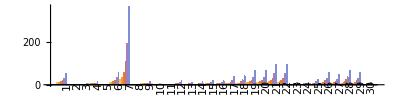

```mathematica
edata=Table[Module[{r=SelectFirst[#,#["id"]===e&]},If[MissingQ[r],<|"mean_time"->0|>,r]],{e,0,29}]&/@data;
BarChart[
Transpose[Values[Lookup[#,"mean_time"]&/@KeySort[edata]]],
ChartLabels->{(Style[Rotate[#,90Degree],Black]&/@Range[30]),None},
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{1,1}
]
```

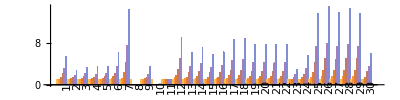

```mathematica
edata=Table[Module[{r=SelectFirst[#,#["id"]===e&]},If[MissingQ[r],<|"mean_time"->0|>,r]],{e,0,29}]&/@data;
rdata=Transpose[Values[Lookup[#,"mean_time"]&/@KeySort[edata]]];
rdata=Map[#/#[[1]]&,rdata];
BarChart[
rdata,
ChartLabels->{(Style[Rotate[#,90Degree],Black]&/@Range[30]),None},
AspectRatio->1/4,ImageSize->Scaled[0.75],
BarSpacing->{1,1}
]
```

```mathematica
figs=Table[BarChart[
1000*Lookup[data[batchSize],"mean_time"],
ChartLabels->(Style[Rotate[#+1,90Degree],Black]&/@Lookup[data[batchSize],"id"]),
AspectRatio->1/4,ImageSize->Scaled[0.75],
PlotTheme->"Grid",
Ticks->None,
ChartStyle->Black,
AspectRatio->1/6,
BarSpacing->{1,1},
Axes->{True,False},
PlotRange->All,
PlotRangePadding->None,
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
Frame->True,
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{{Style["Latency (ms)",Black,14],""},{"","MXNet V100 Batch Size "<>ToString[batchSize]}},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
],{batchSize,{1,2,4,8,16,32}}];
```

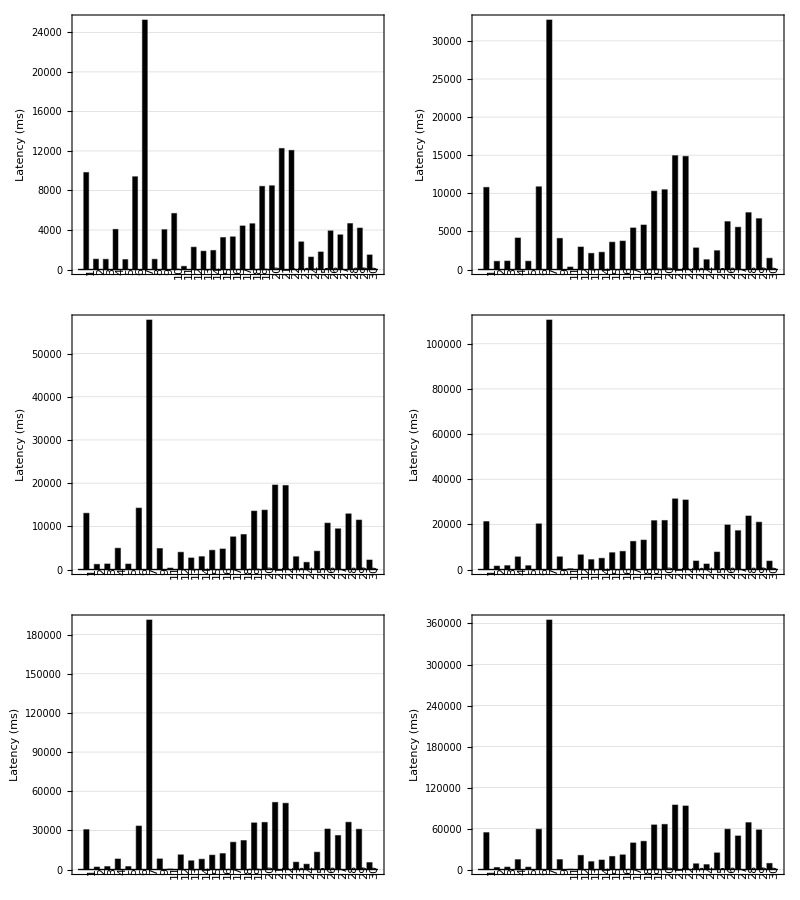

```mathematica
Grid[Partition[figs,UpTo[2]],ItemSize->Scaled[0.4]]
```

## ** CONV Heuristics Paper

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
shortConvAlgorithmNames=<|
-1->Missing[],
0->"IGEMM",
1->"IPGMM",
2->"GEMM",
3->"DRCT",
4->"FFT",
5->"TFFT",
6->"WING",
7->"WINGNF",
8->"CNT"
|>;
```

```mathematica
files=FileNames["*.json","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_1/Tesla_V100-SXM2-16GB"];
data=raw=#["benchmark"]&/@Flatten[{Import[#,"RawJSON"]&/@files}];
recall=Select[data,StringContainsQ[#["Name"],"CONV_FWD_"]&];

db=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/1.json","RawJSON"];
db=db["benchmarks"];
db=Select[db,StringContainsQ[#["name"],"CONV_FWD_"]&&Lookup[#,"error_occurred",False]==False&];
```

```mathematica
xgetAlg[e_]:=Floor[e["convolution_algorithm"]];
makeConf3[e_]:=Floor@Lookup[e,{"input_batch_size","input_channels","input_height","input_size","input_width","num_filters","dilation_height","dilation_width","filter_count","filter_height","filter_width"}];
makeConf2[e_]:=Floor@Lookup[e,{"input_batch_size","input_channels","input_height","input_size","input_width","num_filters","dilation_height","dilation_width","filter_count","filter_height","filter_width","convolution_algorithm"}];
makeConf[e_]:=Floor@Lookup[e,{"input_batch_size","input_channels","input_height","input_size","input_width","num_filters","dilation_height","dilation_width","filter_count","filter_height","filter_width","advised_convolution_algorithm","convolution_algorithm"}];
findInRecall[e_]:=
SelectFirst[recall,makeConf3[e]==makeConf3[#]&]
```

```mathematica
confs=makeConf/@recall;
econfs=First[#][[;;-2]]&/@Select[Normal[Counts[confs]],(*#[[2]]>1&&*)#[[1,-1]]=!=#[[1,-2]]&];
```

```mathematica
edb=Select[db,MemberQ[econfs,makeConf2[#]]&];
```

```mathematica
edb//Length
```

35

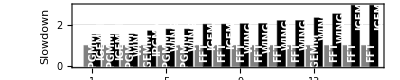

```mathematica
bdata=SortBy[Select[Table[{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e["convolution_algorithm"]],Bold,White,FontSize->10] ,90Degree],Top],
Labeled[e["real_time"]/findInRecall[e]["RealTime"],Rotate[Style[shortConvAlgorithmNames[Floor@findInRecall[e]["convolution_algorithm"]],Bold,White,FontSize->10] ,90Degree],Top]
},{e,edb}],#[[2,1]]>1.5&],Last];
fig=BarChart[
bdata,
AspectRatio->1/5,
Frame->True,
ChartStyle->{Gray,Black},
BarSpacing->{0,0.25},
ChartLabels->{(Style[#,Black,FontSize->10]&/@Range[Length[bdata]]),None},
FrameLabel->{{Style["Slowdown",12],None},{None,None(*"CUDNN v7.6.3 Heuristic Discrepency"*)}},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->12]&/@{"Ideal Algorithm","cuDNN Heuristic"},Background->Opacity[0.9,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.01,0.7},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
(*FrameTicks->{{True,None},{None,True}},*)
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
PlotTheme->{"FrameGrid","GrayColor"},
Ticks->{None,Automatic} ,
AspectRatio->1/5,
ImageSize->Scaled[0.8]
]
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/heuristics/figures/";
Quiet[CreateDirectory[targetDir]];
pdf=Export[targetDir<>"cudnn_paper_heuristics.pdf",Magnify[fig,1.1],"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>"cudnn_paper_heuristics.png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
```

```mathematica
SystemOpen[targetDir]
```

## Active Classification CONV

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/32.json";
data=Import[file,"RawJSON"];
data=data["benchmarks"];
data=Select[data,StringContainsQ[#["name"],"CONV_FWD_"]&];
```

```mathematica
getAlg[e_]:=Floor[e["convolution_algorithm"]];
makeConf[e_]:=Floor@Lookup[e,{"input_batch_size","input_channels","input_height","input_size","input_width","num_filters","dilation_height","dilation_width","filter_count","filter_height","filter_width"}];
makeConf[e_]:=Lookup[e,{"filter_height","filter_width"}];
```

```mathematica
getAlg[makeConf[data[[1]]]]
```

Floor[{32,16,55,1548800,55,64,1,1,64,1,1}[convolution_algorithm]]

```mathematica
aco=ActiveClassification[getAlg,data->makeConf]
```

ActiveClassification::bdnsampler: The neighborhood configuration generator makeConf, together with 
	initial configuration set {«1»}, is not valid.

ActiveClassification[getAlg,{<|name→LAYER_CUDNN_CONV_FWD_0_FLOAT32__BatchSize_32__6346074546501876131<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:32/input[1]:1…tride_height:1/stride_width:1/dilation_height:1/dilation_width:1/group:1/batch_size:32/conv_fwd_type:1/conv_bwd_type:0/manual_time,57,…→0.|>,2926,<|1|>}→8]
 |  |  |  |

```mathematica
cf=Classify[Table[makeConf[e]->getAlg[e],{e,data}],Method->{"NeuralNetwork","NetworkDepth"->6,MaxTrainingRounds->200}]
```

```mathematica
cf=Classify[Table[makeConf[e]->getAlg[e],{e,data}]]
```

ClassifierFunction[…]

```mathematica
Information[cf]
```

Classifier information
Data type | {Numerical,Numerical}
Number of classes | 8
Accuracy | (44.12.9) %
Method | NaiveBayes
Single evaluation time | 6.49 ms/example
Batch evaluation speed | 10. examples/ms
Loss | 1.31 ± 0.055
Model memory | 214. kB
Training examples used | 2928 examples
Training time | 2.6 s
 |

## Distribution Layers

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Import[file,"RawJSON"],"type"];
net,
{file,files}
];
```

```mathematica
layerTypes=Reverse[Sort[KeyDrop[Counts[nets],"ConstantInput"]]]
```

<|Conv→1481,Relu→1372,BatchNorm→1317,ElementWise→752,Unsqueeze→380,Pooling→109,Reshape→103,Concat→97,Gemm→43,Dropout→32,Flatten→18,Transpose→16,GlobalPooling→12,LRN→12,Softmax→8,Scale→1,Identity→1|>

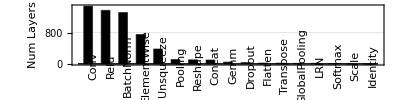

```mathematica
BarChart[
layerTypes,
ChartLabels->(Style[Rotate[#,90Degree],Black]&/@Keys[Normal[layerTypes]]),
AspectRatio->1/4,ImageSize->Scaled[0.75],
PlotTheme->"Grid",
Ticks->None,
ChartStyle->Black,
AspectRatio->1/6,
BarSpacing->{1,1},
Axes->{True,False},
PlotRange->All,
PlotRangePadding->None,
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
Frame->True,
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{"",Style["Num Layers",Black,14]},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

```mathematica
prevCell=NotebookRead[PreviousCell[]]/.HoldPattern[CellLabel->_]->Sequence[];
fl=Export[CreateFile[],prevCell,"PDF"];
e=First@Import[fl,"PDF"];
e=e//.HoldPattern[ImageSize->x_]->(ImageSize->Scaled[0.75]);
{
CloudExport[e,"NB",ImageResolution->600,Permissions->"Public",CloudObjectURLType->"Object"],
CloudExport[Notebook[{prevCell},Editable->False,WindowSize->Scaled[1]],"NB",ImageResolution->500,ImageSize->500,Permissions->"Public",CloudObjectURLType->"Object"]
}
```

{CloudObject[https://www.wolframcloud.com/obj/452ba7c4-40d1-4e76-b4f8-9597c114ac2c],CloudObject[https://www.wolframcloud.com/obj/9c656986-6f6e-457e-a9a5-1c069330f8a0]}

```mathematica
ExportString[Normal[layerTypes]/.Rule->List,"CSV"]//CopyToClipboard
```

## A look at ElementWise

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Select[Import[file,"RawJSON"],#["type"]==="ElementWise"&],"input_dimensions"];
net,
{file,files}
];
```

```mathematica
nets
```

{<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,748,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>}
 |  |  |  |

## Move look at ElementWise

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Select[Import[file,"RawJSON"],#["type"]==="ElementWise"&];
net,
{file,files}
];
```

```mathematica
nets[[1]]
```

<|name→_minusscalar0,type→ElementWise,inputs→{id,scalar_op2},outputs→{_minusscalar0},input_dimensions→<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>|>

```mathematica
nets
```

{<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,748,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>}
 |  |  |  |

## A look at GEMM

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Select[Import[file,"RawJSON"],ToUpperCase[#["type"]]==="GEMM"||ToUpperCase[#["type"]]==="MATMUL"&],"input_dimensions"];
net,
{file,files}
];
```

```mathematica
nets
```

{<|input_shapes→{{1,512,7,7},{512,25088},{512}},output_shapes→{{1,512}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{200,4096},{200}},output_shapes→{{1,200}}|>,<|input_shapes→{{1,4096},{4096,1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1024,1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1024,8}},output_shapes→{{1,8}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,256},{256,10}},output_shapes→{{1,10}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,512,1,1},{1000,512},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,512},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{0,-1},{1000,512},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,512,1,1},{1000,512},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,544},{1000,544},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,18432},{4096,18432},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1024,4096},{1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>}

## % of layers common between networks

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
nets=Catenate@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
net,
{file,files}
];
netLayers=Counts[nets];
N[Length[netLayers]/Total[Values[netLayers]]]
```

0.179006

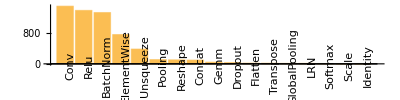

```mathematica
layerTypes=Reverse@Sort@Counts[Lookup[nets,"type"]];
BarChart[layerTypes,ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[layerTypes]]),
AspectRatio->1/4,ImageSize->Scaled[0.75]]
```

```mathematica
layerTypes
```

<|Conv→1481,Relu→1372,BatchNorm→1317,ElementWise→752,Unsqueeze→380,Pooling→109,Reshape→103,Concat→97,Gemm→43,Dropout→32,Flatten→18,Transpose→16,GlobalPooling→12,LRN→12,Softmax→8,Scale→1,Identity→1|>

```mathematica
ExportString[Normal[layerTypes]/.Rule->List,"CSV"]//CopyToClipboard
```

```mathematica
Keys[layerTypes]
```

{Conv,Relu,BatchNorm,ElementWise,Unsqueeze,Pooling,Reshape,Concat,Gemm,Dropout,Flatten,Transpose,GlobalPooling,LRN,Softmax,Scale,Identity}

```mathematica
Reverse@Sort[netLayers]
```

<|<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,14,14},{256},{256},{256},{256}},output_shapes→{{1,256,14,14},{256},{256},{256},{256}}|>|>→383,1028,<|type→Identity,input_dimensions→<|input_shapes→{{1,3,112,112}},output_shapes→{{1,3,112,112}}|>|>→1|>
 |  |  |  |

```mathematica
percs2=Association@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
FileBaseName[file]->net,
{file,files}
];
```

```mathematica
Keys[percs2]
```

{ArcFace,BVLC_AlexNet,BVLC_CaffeNet,BVLC_GoogleNet,BVLC_RCNN_ILSVRC13,DenseNet-121,DUC,Emotion-FerPlus,Inception-v1,Inception-v2,MNIST,MobileNet-v2,ResNet018-v1,ResNet018-v2,ResNet034-v1,ResNet034-v2,ResNet050-v1,ResNet050-v2,ResNet101-v1,ResNet101-v2,ResNet152-v1,ResNet152-v2,Shufflenet,Squeezenet-v1.1,Tiny_YOLO-v2,VGG16-BN,VGG16,VGG19-BN,VGG19,Zfnet512}

```mathematica
Length@Counts@Catenate[Table[Lookup[e,{"type","input_dimensions"}],{e,percs2}]]
```

1030

```mathematica
69.0/1229
```

0.0561432

```mathematica
Length@Counts@Catenate[Table[Lookup[e,{"type","input_dimensions"}],{e,Values@KeySelect[percs2,StringContainsQ[ToLowerCase[#],"resnet"]&&StringContainsQ[ToLowerCase[#],"v1"]&]}]]
```

60

```mathematica
N@(Length@Counts@Lookup[percs2["ResNet152-v1"],{"type","input_dimensions"}])/(Length@Lookup[percs2["ResNet152-v1"],{"type","input_dimensions"}])
```

0.0912621

```mathematica
Lookup[percs2["ResNet101-v1"],{"type","input_dimensions"}]
```

{{Conv,<|input_shapes→{{1,3,224,224},{64,3,7,7}},output_shapes→{{1,64,112,112}}|>},{BatchNorm,<|input_shapes→{{1,64,112,112},{64},{64},{64},{64}},output_shapes→{{1,64,112,112},{64},{64},{64},{64}}|>},342,{Gemm,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>}}
 |  |  |  |

```mathematica
Grid[
Normal[Reverse@Sort@Counts[Table[
{e[[1]],e[[2]]["input_shapes"][[1]]},
{e,Lookup[percs2["ResNet50-v1"],{"type","input_dimensions"}]}
]]]/.Rule->List,Frame->All]
```

{Conv,{1,256,14,14}} | 12
{Relu,{1,256,14,14}} | 12
{BatchNorm,{1,256,14,14}} | 12
{Conv,{1,128,28,28}} | 8
{Relu,{1,128,28,28}} | 8
{BatchNorm,{1,128,28,28}} | 8
{Conv,{1,64,56,56}} | 8
{Conv,{1,1024,14,14}} | 7
{BatchNorm,{1,1024,14,14}} | 7
{Conv,{1,512,7,7}} | 6
{Relu,{1,512,7,7}} | 6
{BatchNorm,{1,512,7,7}} | 6
{Relu,{1,1024,14,14}} | 6
{ElementWise,{1,1024,14,14}} | 6
{Relu,{1,64,56,56}} | 6
{BatchNorm,{1,64,56,56}} | 6
{Conv,{1,512,28,28}} | 5
{BatchNorm,{1,512,28,28}} | 5
{BatchNorm,{1,2048,7,7}} | 4
{Relu,{1,512,28,28}} | 4
{ElementWise,{1,512,28,28}} | 4
{Conv,{1,256,56,56}} | 4
{BatchNorm,{1,256,56,56}} | 4
{Relu,{1,2048,7,7}} | 3
{ElementWise,{1,2048,7,7}} | 3
{Relu,{1,256,56,56}} | 3
{ElementWise,{1,256,56,56}} | 3
{Conv,{1,2048,7,7}} | 2
{Gemm,{1,2048,1,1}} | 1
{Flatten,{1,2048,1,1}} | 1
{GlobalPooling,{1,2048,7,7}} | 1
{Pooling,{1,64,112,112}} | 1
{Relu,{1,64,112,112}} | 1
{BatchNorm,{1,64,112,112}} | 1
{Conv,{1,3,224,224}} | 1

```mathematica
Grid[
Normal[Reverse@Sort@Counts[Table[
{e[[1]],e[[2]]["input_shapes"][[1]]},
{e,Lookup[percs2["ResNet101-v1"],{"type","input_dimensions"}]}
]]]/.Rule->List,Frame->All]
```

{Conv,{1,256,14,14}} | 46
{Relu,{1,256,14,14}} | 46
{BatchNorm,{1,256,14,14}} | 46
{Conv,{1,1024,14,14}} | 24
{BatchNorm,{1,1024,14,14}} | 24
{Relu,{1,1024,14,14}} | 23
{ElementWise,{1,1024,14,14}} | 23
{Conv,{1,128,28,28}} | 8
{Relu,{1,128,28,28}} | 8
{BatchNorm,{1,128,28,28}} | 8
{Conv,{1,64,56,56}} | 8
{Conv,{1,512,7,7}} | 6
{Relu,{1,512,7,7}} | 6
{BatchNorm,{1,512,7,7}} | 6
{Relu,{1,64,56,56}} | 6
{BatchNorm,{1,64,56,56}} | 6
{Conv,{1,512,28,28}} | 5
{BatchNorm,{1,512,28,28}} | 5
{BatchNorm,{1,2048,7,7}} | 4
{Relu,{1,512,28,28}} | 4
{ElementWise,{1,512,28,28}} | 4
{Conv,{1,256,56,56}} | 4
{BatchNorm,{1,256,56,56}} | 4
{Relu,{1,2048,7,7}} | 3
{ElementWise,{1,2048,7,7}} | 3
{Relu,{1,256,56,56}} | 3
{ElementWise,{1,256,56,56}} | 3
{Conv,{1,2048,7,7}} | 2
{Gemm,{1,2048,1,1}} | 1
{Flatten,{1,2048,1,1}} | 1
{GlobalPooling,{1,2048,7,7}} | 1
{Pooling,{1,64,112,112}} | 1
{Relu,{1,64,112,112}} | 1
{BatchNorm,{1,64,112,112}} | 1
{Conv,{1,3,224,224}} | 1

## % of layers not supported by CUDNN|Scope

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
notSupported=Counts@Flatten@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
notsupported,
{file,files}
];
```

```mathematica
notSupported
```

<|Reshape→103,Flatten→18,Concat→97,Unsqueeze→380,GlobalPooling→12,Transpose→16,Scale→1|>

## % of layers supported by CUDNN|Scope

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
layerPerc=Association@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
supported=Select[Lookup[net,"type"],KeyExistsQ[cudnnSupported,#]&];
FileBaseName[file]->N[Length[supported]/Length[net]],
{file,files}
];
```

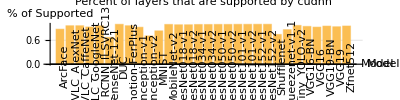

```mathematica
BarChart[
KeyValueMap[Function[{key,val},Tooltip[val,val]],layerPerc],
ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[layerPerc]]),
AxesLabel->{"Model",Rotate["% of Supported",90Degree]},
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
PlotLabel->"Percent of layers that are supported by cudnn",
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

```mathematica
ExportString[MapIndexed[{#2[[1]],100*Round[#1,0.0001]}&,Values@layerPerc],"CSV"]//CopyToClipboard
```

## layers no supported by CUDNN|Scope for inception-v2

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/inception-v2.json";
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Counts@Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
```

```mathematica
Length[Lookup[net,"type"]]
```

509

```mathematica
1-(N@Total[Values[notsupported]]/Length[Lookup[net,"type"]])
```

0.707269

```mathematica
notsupported
```

<|Unsqueeze→138,Concat→10,Reshape→1|>

```mathematica
138/509.0
```

0.27112

## layers no supported by CUDNN|Scope for densenet

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/DenseNet-121.json";
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Counts@Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
```

```mathematica
Length[Lookup[net,"type"]]
```

910

```mathematica
1-(N@Total[Values[notsupported]]/Length[Lookup[net,"type"]])
```

0.67033

```mathematica
notsupported
```

<|Unsqueeze→242,Concat→58|>

```mathematica
242/910.0
```

0.265934

## Model List

```mathematica
files=FileNames["*.json","/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats"];
```

```mathematica
percs=Association@Table[
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
FileBaseName[file]->N[Length[net]/Total[Values[net]]],
{file,files}
];
```

```mathematica
ns=Association@Table[
net=Counts[Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
FileBaseName[file]->Length[net],
{file,files}
]
```

<|ArcFace→412,BVLC_AlexNet→24,BVLC_CaffeNet→24,BVLC_GoogleNet→143,BVLC_RCNN_ILSVRC13→23,DenseNet-121→910,DUC→355,Emotion-FerPlus→52,Inception-v1→144,Inception-v2→509,MNIST→12,MobileNet-v2→155,ResNet018-v1→69,ResNet018-v2→69,ResNet034-v1→125,ResNet034-v2→125,ResNet050-v1→175,ResNet050-v2→174,ResNet101-v1→345,ResNet101-v2→344,ResNet152-v1→515,ResNet152-v2→514,Shufflenet→203,Squeezenet-v1.1→66,Tiny_YOLO-v2→32,VGG16-BN→54,VGG16→41,VGG19-BN→63,VGG19→47,Zfnet512→22|>

```mathematica
ii=1;
idMap=AssociationThread[Sort[Keys[percs]]->Range[Length[layerPerc]]];
ExportString[KeyValueMap[Function[{key,val},{ii++,Round[100*val,0.1]}],layerPerc],"CSV"]//CopyToClipboard
```

AssociationThread::idim: {ArcFace,BVLC_AlexNet,BVLC_CaffeNet,BVLC_GoogleNet,BVLC_RCNN_ILSVRC13,DenseNet-121,DUC,Emotion-FerPlus,Inception-v1,Inception-v2,MNIST,MobileNet-v2,ResNet018-v1,«4»,ResNet050-v2,ResNet101-v1,ResNet101-v2,ResNet152-v1,ResNet152-v2,Shufflenet,Squeezenet-v1.1,Tiny_YOLO-v2,VGG16,VGG16-BN,VGG19,VGG19-BN,Zfnet512} and {} must have the same length.

KeyValueMap::invak: The argument layerPerc is not a valid Association.

```mathematica
Keys[percs]
```

{ArcFace,BVLC_AlexNet,BVLC_CaffeNet,BVLC_GoogleNet,BVLC_RCNN_ILSVRC13,DenseNet-121,DUC,Emotion-FerPlus,Inception-v1,Inception-v2,MNIST,MobileNet-v2,ResNet018-v1,ResNet018-v2,ResNet034-v1,ResNet034-v2,ResNet050-v1,ResNet050-v2,ResNet101-v1,ResNet101-v2,ResNet152-v1,ResNet152-v2,Shufflenet,Squeezenet-v1.1,Tiny_YOLO-v2,VGG16-BN,VGG16,VGG19-BN,VGG19,Zfnet512}

```mathematica
ii=1;
idMap=AssociationThread[Sort[Keys[percs]]->Range[Length[percs]]];
ExportString[KeyValueMap[Function[{key,val},{ii++,Round[100*val,0.1]}],percs],"CSV"]//CopyToClipboard
```

```mathematica
idMap/@Keys[percs]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,27,26,29,28,30}

```mathematica
ii=1;
StringRiffle[Map[Function[{key},StringJoin[{ToString[ii++]," & ",StringTrim[StringReplace[ToLowerCase@key,"_"->"-"],"\""], " & ", "IC", " & ","  0 &", "\\cite{xxx}"}]],Sort[Keys[percs]]],"\\\\\n"]
```

1 & arcface & IC &   0 &\cite{xxx}\\
2 & bvlc-alexnet & IC &   0 &\cite{xxx}\\
3 & bvlc-caffenet & IC &   0 &\cite{xxx}\\
4 & bvlc-googlenet & IC &   0 &\cite{xxx}\\
5 & bvlc-rcnn-ilsvrc13 & IC &   0 &\cite{xxx}\\
6 & densenet-121 & IC &   0 &\cite{xxx}\\
7 & duc & IC &   0 &\cite{xxx}\\
8 & emotion-ferplus & IC &   0 &\cite{xxx}\\
9 & inception-v1 & IC &   0 &\cite{xxx}\\
10 & inception-v2 & IC &   0 &\cite{xxx}\\
11 & mnist & IC &   0 &\cite{xxx}\\
12 & mobilenet-v2 & IC &   0 &\cite{xxx}\\
13 & resnet018-v1 & IC &   0 &\cite{xxx}\\
14 & resnet018-v2 & IC &   0 &\cite{xxx}\\
15 & resnet034-v1 & IC &   0 &\cite{xxx}\\
16 & resnet034-v2 & IC &   0 &\cite{xxx}\\
17 & resnet050-v1 & IC &   0 &\cite{xxx}\\
18 & resnet050-v2 & IC &   0 &\cite{xxx}\\
19 & resnet101-v1 & IC &   0 &\cite{xxx}\\
20 & resnet101-v2 & IC &   0 &\cite{xxx}\\
21 & resnet152-v1 & IC &   0 &\cite{xxx}\\
22 & resnet152-v2 & IC &   0 &\cite{xxx}\\
23 & shufflenet & IC &   0 &\cite{xxx}\\
24 & squeezenet-v1.1 & IC &   0 &\cite{xxx}\\
25 & tiny-yolo-v2 & IC &   0 &\cite{xxx}\\
26 & vgg16 & IC &   0 &\cite{xxx}\\
27 & vgg16-bn & IC &   0 &\cite{xxx}\\
28 & vgg19 & IC &   0 &\cite{xxx}\\
29 & vgg19-bn & IC &   0 &\cite{xxx}\\
30 & zfnet512 & IC &   0 &\cite{xxx}

```mathematica
ii=1;
ExportString[KeyValueMap[Function[{key,val},{ii++,100*val}],percs],"CSV"]//CopyToClipboard
```

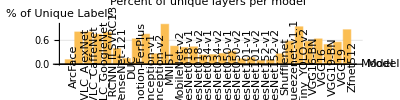

```mathematica
BarChart[
KeyValueMap[Function[{key,val},Tooltip[val,key]],percs],
ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[percs]]),
AxesLabel->{"Model",Rotate["% of Unique Labels",90Degree]},
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
PlotLabel->"Percent of unique layers per model",
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

```mathematica
files
```

```mathematica
file=SelectFirst[files,StringContainsQ["ResNet152-v2"]]
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/ResNet152-v2.json

```mathematica
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
N[Length[net]]
```

56.

```mathematica
Total[Values[net]]
```

514

```mathematica
net
```

<|<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,3,224,224},{3},{3},{3},{3}},output_shapes→{{1,3,224,224},{3},{3},{3},{3}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,3,224,224},{64,3,7,7}},output_shapes→{{1,64,112,112}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,64,112,112},{64},{64},{64},{64}},output_shapes→{{1,64,112,112},{64},{64},{64},{64}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,64,112,112}},output_shapes→{{1,64,112,112}}|>|>→1,<|type→Pooling,input_dimensions→<|input_shapes→{{1,64,112,112}},output_shapes→{{1,64,56,56}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,64,56,56},{64},{64},{64},{64}},output_shapes→{{1,64,56,56},{64},{64},{64},{64}}|>|>→7,<|type→Relu,input_dimensions→<|input_shapes→{{1,64,56,56}},output_shapes→{{1,64,56,56}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{64,64,1,1}},output_shapes→{{1,64,56,56}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{64,64,3,3}},output_shapes→{{1,64,56,56}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{256,64,1,1}},output_shapes→{{1,256,56,56}}|>|>→4,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,256,56,56},{1,256,56,56}},output_shapes→{{1,256,56,56}}|>|>→3,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,56,56},{256},{256},{256},{256}},output_shapes→{{1,256,56,56},{256},{256},{256},{256}}|>|>→3,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,56,56}},output_shapes→{{1,256,56,56}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{64,256,1,1}},output_shapes→{{1,64,56,56}}|>|>→2,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{128,256,1,1}},output_shapes→{{1,128,56,56}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,128,56,56},{128},{128},{128},{128}},output_shapes→{{1,128,56,56},{128},{128},{128},{128}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,128,56,56}},output_shapes→{{1,128,56,56}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,56,56},{128,128,3,3}},output_shapes→{{1,128,28,28}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,128,28,28},{128},{128},{128},{128}},output_shapes→{{1,128,28,28},{128},{128},{128},{128}}|>|>→15,<|type→Relu,input_dimensions→<|input_shapes→{{1,128,28,28}},output_shapes→{{1,128,28,28}}|>|>→15,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,28,28},{512,128,1,1}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{512,256,1,1}},output_shapes→{{1,512,28,28}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,512,28,28},{1,512,28,28}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,28,28},{512},{512},{512},{512}},output_shapes→{{1,512,28,28},{512},{512},{512},{512}}|>|>→8,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,28,28}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{128,512,1,1}},output_shapes→{{1,128,28,28}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,28,28},{128,128,3,3}},output_shapes→{{1,128,28,28}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{256,512,1,1}},output_shapes→{{1,256,28,28}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,28,28},{256},{256},{256},{256}},output_shapes→{{1,256,28,28},{256},{256},{256},{256}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,28,28}},output_shapes→{{1,256,28,28}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,28,28},{256,256,3,3}},output_shapes→{{1,256,14,14}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,14,14},{256},{256},{256},{256}},output_shapes→{{1,256,14,14},{256},{256},{256},{256}}|>|>→71,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,14,14}},output_shapes→{{1,256,14,14}}|>|>→71,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,14,14},{1024,256,1,1}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{1024,512,1,1}},output_shapes→{{1,1024,14,14}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,1024,14,14},{1,1024,14,14}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,1024,14,14},{1024},{1024},{1024},{1024}},output_shapes→{{1,1024,14,14},{1024},{1024},{1024},{1024}}|>|>→36,<|type→Relu,input_dimensions→<|input_shapes→{{1,1024,14,14}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{256,1024,1,1}},output_shapes→{{1,256,14,14}}|>|>→35,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,14,14},{256,256,3,3}},output_shapes→{{1,256,14,14}}|>|>→35,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{512,1024,1,1}},output_shapes→{{1,512,14,14}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,14,14},{512},{512},{512},{512}},output_shapes→{{1,512,14,14},{512},{512},{512},{512}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,14,14}},output_shapes→{{1,512,14,14}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,14,14},{512,512,3,3}},output_shapes→{{1,512,7,7}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,7,7},{512},{512},{512},{512}},output_shapes→{{1,512,7,7},{512},{512},{512},{512}}|>|>→5,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,7,7}},output_shapes→{{1,512,7,7}}|>|>→5,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,7,7},{2048,512,1,1}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{2048,1024,1,1}},output_shapes→{{1,2048,7,7}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,2048,7,7},{1,2048,7,7}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,2048,7,7},{2048},{2048},{2048},{2048}},output_shapes→{{1,2048,7,7},{2048},{2048},{2048},{2048}}|>|>→3,<|type→Relu,input_dimensions→<|input_shapes→{{1,2048,7,7}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,2048,7,7},{512,2048,1,1}},output_shapes→{{1,512,7,7}}|>|>→2,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,7,7},{512,512,3,3}},output_shapes→{{1,512,7,7}}|>|>→2,<|type→GlobalPooling,input_dimensions→<|input_shapes→{{1,2048,7,7}},output_shapes→{{1,2048,1,1}}|>|>→1,<|type→Reshape,input_dimensions→<|input_shapes→{{1,2048,1,1},{0,-1}},output_shapes→{{0,-1}}|>|>→1,<|type→Gemm,input_dimensions→<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>|>→1|>

```mathematica
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
N[Length[net]]
```

56.

## CUDNN Heuristic divergence for website

typedef enum {
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM         = 0,
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_PRECOMP_GEMM = 1,
     CUDNN_CONVOLUTION_FWD_ALGO_GEMM                  = 2,
     CUDNN_CONVOLUTION_FWD_ALGO_DIRECT                = 3,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT                   = 4,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT_TILING            = 5,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD              = 6,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD_NONFUSED     = 7,
     CUDNN_CONVOLUTION_FWD_ALGO_COUNT                 = 8
 } cudnnConvolutionFwdAlgo_t;

```mathematica
cudnnVersion="7.5.0.56";
batchSize="32";
```

```mathematica
file=If[cudnnVersion=="7.6.3",
"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/"<>batchSize<>".json",
"/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/"<>cudnnVersion<>"/Tesla_V100-SXM2-16GB/"<>batchSize<>".json"
];
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
nonAdvised={First[MinimalBy[#,#["real_time"]&]],SelectFirst[#,#["convolution_algorithm"]===#["advised_convolution_algorithm"]&]}&/@GroupBy[convLayers,Lookup[#,{"input[0]","input[1]","input[2]","input[3]","filter_count","filter_height","filter_width","pad_height","pad_width","stride_height","stride_width","dilation_height","dilation_width"}]&];
nonAdvised=KeyValueMap[Function[{key,val},If[Lookup[val[[1]],"real_time"]=!=Lookup[val[[2]],"real_time"],key->val,Nothing]],nonAdvised];
nonAdvised=Select[nonAdvised,Apply[Divide,Lookup[#[[2]],"real_time"]]<0.8&];
```

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
shortConvAlgorithmNames=<|
-1->Missing[],
0->"IGEMM",
1->"IPGEMM",
2->"GEMM",
3->"DRCT",
4->"FFT",
5->"TFFT",
6->"WING",
7->"WINGNF",
8->"CNT"
|>;
```

```mathematica
Lookup[#,"real_time"]&/@Values[nonAdvised]
```

{{530633.,799177.},{416914.,616155.},{6.61241×10^6,1.03692×10^7},{36082.1,90261.2},{181832.,227542.},{68161.4,125859.},{99283.3,205426.},{42681.8,86225.},{45961.8,99628.2},{110000.,201638.},{73253.5,127020.},{319707.,838368.},{205424.,328652.},{1.04687×10^6,1.52812×10^6},{274745.,483754.},{251844.,317178.},{57361.7,75902.6},{61812.8,79697.7},{1.29316×10^7,1.66853×10^7},{33461.1,68126.3},{82912.9,150473.},{420447.,779907.},{326759.,420659.},{304753.,408589.},{3.07952×10^6,5.99486×10^6},{16718.8,28399.6},{432276.,602486.},{4.29824×10^6,7.43716×10^6},{50507.,85450.4},{64067.6,108679.},{117021.,242829.},{244744.,327635.},{374252.,617064.},{2.88383×10^6,7.54477×10^6},{1.49587×10^6,4.09234×10^6},{29014.7,36957.7},{177607.,288706.},{309661.,427899.},{103634.,252836.},{416488.,780664.},{782069.,2.48381×10^6},{332132.,427058.},{81479.8,113831.},{255751.,320559.},{1.09408×10^7,1.46573×10^7},{55715.4,163977.},{93058.8,173132.},{107089.,162032.},{1.68851×10^6,3.04364×10^6},{307361.,427291.},{96946.7,169971.},{62373.5,80420.6},{63251.6,81790.4},{536729.,780741.},{3.34564×10^6,4.80435×10^6},{349809.,485143.},{324650.,843559.},{1.86562×10^6,2.71884×10^6}}

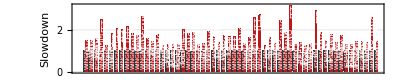

```mathematica
fig=BarChart[
Table[
{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e[[1]]["convolution_algorithm"]],White,FontSize->6] ,90Degree],Top],
Labeled[e[[2]]["real_time"]/e[[1]]["real_time"],Rotate[Style[shortConvAlgorithmNames[Floor@e[[2]]["convolution_algorithm"]],White,FontSize->8] ,90Degree],Top]
},{e,Values[nonAdvised]}],
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.2, 0.2, 0.2],RGBColor[0.73, 0.09803921568627451, 0.10980392156862745]},
BarSpacing->{0,1},
FrameLabel->{{Style["Slowdown",10],None},{None,"CUDNN v"<>cudnnVersion<>" Heuristic Discrepency (BatchSize = "<>batchSize<>")"}},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->8]&/@{"Fastest","Advised"},Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
PlotTheme->{"FrameGrid","GrayColor"},
Ticks->{None,Automatic} ,
AspectRatio->1/5,
ImageSize->Scaled[0.8],
BarSpacing->{0,1}
]
```

```mathematica
targetDir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_scope_website/static/assets/heuristics/figures/";
Quiet[CreateDirectory[targetDir]];
pdf=Export[targetDir<>"cudnn_"<>cudnnVersion<>".pdf",fig,"PDF","CompressionLevel"->0,ImageSize->1024,ImageResolution->100];
png=Export[targetDir<>"cudnn_"<>cudnnVersion<>".png",fig,"PNG","CompressionLevel"->0,ImageResolution->100];
```

## CUDNN Heuristic divergence

typedef enum {
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM         = 0,
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_PRECOMP_GEMM = 1,
     CUDNN_CONVOLUTION_FWD_ALGO_GEMM                  = 2,
     CUDNN_CONVOLUTION_FWD_ALGO_DIRECT                = 3,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT                   = 4,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT_TILING            = 5,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD              = 6,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD_NONFUSED     = 7,
     CUDNN_CONVOLUTION_FWD_ALGO_COUNT                 = 8
 } cudnnConvolutionFwdAlgo_t;

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/Tesla_V100-SXM2-16GB/32.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
nonAdvised={First[MinimalBy[#,#["real_time"]&]],SelectFirst[#,#["convolution_algorithm"]===#["advised_convolution_algorithm"]&]}&/@GroupBy[convLayers,Lookup[#,{"input[0]","input[1]","input[2]","input[3]","filter_count","filter_height","filter_width","pad_height","pad_width","stride_height","stride_width","dilation_height","dilation_width"}]&];
nonAdvised=KeyValueMap[Function[{key,val},If[Lookup[val[[1]],"real_time"]=!=Lookup[val[[2]],"real_time"],key->val,Nothing]],nonAdvised];
nonAdvised=Select[nonAdvised,Apply[Divide,Lookup[#[[2]],"real_time"]]<0.8&];
```

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
shortConvAlgorithmNames=<|
-1->Missing[],
0->"IGEMM",
1->"IPGEMM",
2->"GEMM",
3->"DRCT",
4->"FFT",
5->"TFFT",
6->"WING",
7->"WINGNF",
8->"CNT"
|>;
```

```mathematica
Lookup[#,"real_time"]&/@Values[nonAdvised]
```

{{530601.,805333.},{419017.,619829.},{6.61942×10^6,1.03979×10^7},{36477.,91165.8},{182522.,229322.},{68889.4,126108.},{99501.5,206294.},{43005.2,86806.3},{46422.6,99785.3},{110344.,202359.},{73570.7,127655.},{320450.,841443.},{205780.,329145.},{1.05061×10^6,1.529×10^6},{275247.,483687.},{252298.,317368.},{58132.4,76594.7},{61857.2,79389.},{1.29665×10^7,1.67011×10^7},{33785.2,68656.4},{83051.8,150894.},{419799.,780977.},{325904.,422865.},{305401.,409245.},{3.08771×10^6,5.99531×10^6},{17359.1,29331.7},{432408.,603264.},{4.30364×10^6,7.45566×10^6},{50309.3,85792.5},{64384.6,108728.},{117496.,243297.},{244732.,328405.},{373878.,617235.},{2.89185×10^6,7.54197×10^6},{1.50125×10^6,4.09229×10^6},{29348.3,37173.1},{177395.,289607.},{310389.,429032.},{104030.,253530.},{417010.,779278.},{780996.,2.48368×10^6},{334173.,428265.},{81290.8,114724.},{256569.,321903.},{1.09435×10^7,1.4678×10^7},{55856.6,165292.},{93502.4,174242.},{108203.,162615.},{1.68905×10^6,3.04733×10^6},{307682.,427292.},{97652.6,170463.},{62209.3,80294.7},{63767.1,83011.1},{538656.,784384.},{3.35884×10^6,4.78786×10^6},{353051.,486261.},{325150.,848830.},{1.86432×10^6,2.71903×10^6}}

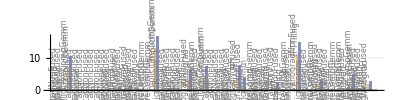

```mathematica
BarChart[
Table[Table[Labeled[j["real_time"]/10^6,Rotate[Style[convAlgorithmNames[Floor@j["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above],{j,e}],{e,Values[nonAdvised]}],
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
BarSpacing->{0,1},
ChartLegends->{"fastest","advised"}
]
```

### normalized

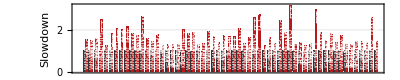

```mathematica
BarChart[
Table[
{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e[[1]]["convolution_algorithm"]],White,FontSize->6] ,90Degree],Top],
Labeled[e[[2]]["real_time"]/e[[1]]["real_time"],Rotate[Style[shortConvAlgorithmNames[Floor@e[[2]]["convolution_algorithm"]],White,FontSize->8] ,90Degree],Top]
},{e,Values[nonAdvised]}],
AspectRatio->1/5,
Frame->True,
ChartStyle->{RGBColor[0.2, 0.2, 0.2],RGBColor[0.73, 0.09803921568627451, 0.10980392156862745]},
BarSpacing->{0,1},
FrameLabel->{{Style["Slowdown",10],None},{None,"CUDNN v7.6.3 Heuristic Discrepency"}},
ChartLegends->Placed[SwatchLegend[Style[#,Black,FontSize->8]&/@{"Fastest","Advised"},Background->Opacity[0.5,White],LegendMarkerSize->10,LegendLayout->{"Row",1}],{{0.03,0.8},{0,0}}],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
FrameTicks->{{True,None},{None,True}},
PlotRange->All,
PlotRangePadding->{Automatic,0},
Method->{"ShrinkWrap"->True},
LabelStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->15},
PlotTheme->{"FrameGrid","GrayColor"},
Ticks->{None,Automatic} ,
AspectRatio->1/5,
ImageSize->Scaled[0.8],
BarSpacing->{0,1}
]
```

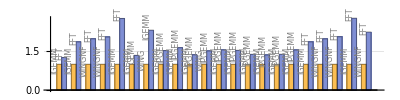

```mathematica
BarChart[
Table[
{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e[[1]]["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above],
Labeled[e[[2]]["real_time"]/e[[1]]["real_time"],Rotate[Style[shortConvAlgorithmNames[Floor@e[[2]]["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above]
},{e,Values[nonAdvised]}],
PlotTheme->{"Grid"},
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
BarSpacing->{0,1},
ChartLegends->{"fastest","advised"}
]
```

## Inception Module Analysis

## Batch Sizes

## Memory Copy Model

process the data

```mathematica
Pane[StringRiffle[FileNames["*json","~/code/ispass-19/data/"],"\n"],ImageSize->{Full,300},Scrollbars->True]
```

~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Coherence_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Coherence_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToPinned_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToWC.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_HostToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_WCToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Prefetch_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Prefetch_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Host_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Pinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_GPUToHost_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_GPUToHost_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_ZeroCopy_HostToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Coherence_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Coherence_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToGPU_0.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToGPU_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Prefetch_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Prefetch_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_HostToGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Host_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Pinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToHost_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToPinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_HostToGPU_Write.json

```mathematica
rawdata=Import["~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU.json","RawJSON"]["benchmarks"];
rawdata=Import["~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU.json","RawJSON"]["benchmarks"];
```

```mathematica
data=KeyValueMap[Function[{k,v},{k,Min[v[[All,2]]]}],GroupBy[Map[{Log2@#[[1]],#[[1]]/#[[2]]}&,
Select[
Lookup[rawdata,{"bytes","real_time"}],
#[[1]]>0&
]],First]];
minX=10;
maxX=Max[data[[All,1]]];
data
```

{{29.,14.507},{2.16096,9.83632×10^-6},{22.,16.1434},{-4.83904,1.42883×10^-6},{27.,15.4315},{0.160964,0.000018162},{17.,8.82299},{-9.83904,0.0000201797},{19.,12.834},{-7.83904,0.0000969247},{18.,11.0654},{-8.83904,0.0000363502},{14.,2.44309},{-12.839,1.00476×10^-6},{33.,14.1637},{6.16096,7.83795×10^-6},{12.,0.69471},{-14.839,6.8585×10^-7},{24.,14.921},{-2.83904,6.90144×10^-6},{16.,4.96134},{-10.839,3.91461×10^-6},{10.,0.17897},{-16.839,2.7329×10^-7},{8.,0.0437816},{-18.839,4.01346×10^-8},{21.,16.3883},{-5.83904,2.29228×10^-6},{28.,14.8247},{1.16096,0.0000119263},{20.,13.6647},{-6.83904,3.61836×10^-6},{23.,14.0198},{-3.83904,2.34597×10^-6},{13.,1.34881},{-13.839,9.06677×10^-7},{30.,14.383},{3.16096,0.0000103894},{15.,3.64977},{-11.839,2.37604×10^-6},{9.,0.0868238},{-17.839,6.12888×10^-8},{11.,0.356936},{-15.839,3.41425×10^-7},{32.,14.1398},{5.16096,8.70875×10^-6},{31.,14.2708},{4.16096,9.87134×10^-6},{26.,15.9191},{-0.839036,4.23482×10^-6},{25.,16.534},{-1.83904,4.36594×10^-6}}

find a formula that fits the data (this uses some “magic” to get the formula)

```mathematica
ClearAll[x];
fit=FindFormula[data,x]//FullSimplify
```

0.0351205+1/(0.0664935+20424.3 ⅇ^(-0.760606 x))

```mathematica
StringReplace[
ToString@CForm[fit/.E^(x__):>mathExp[x]],
"mathExp"->"math.Exp"
]//CopyToClipboard
```

```mathematica
TraditionalForm[fit]
```

1/(0.0664935+20424.3 ⅇ^(-0.760606 x))+0.0351205

Plots similar to the ones presented in the paper (on trimmed dataset starting at 2^10)

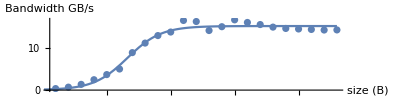

```mathematica
trimmedData=Select[data,#[[1]]>minX&];
Show[ListPlot[trimmedData,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
AxesLabel->{"size (B)","Bandwidth GB/s"}],Plot[fit,{x,minX,maxX},Filling->{2->{1}}]]
```

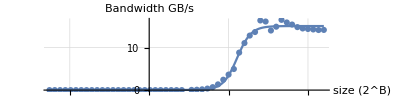

```mathematica
Show[
ListPlot[
data,
PlotTheme->"Grid",
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"size (2^B)","Bandwidth GB/s"}
],
Plot[
fit,
{x,0,maxX},
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
]
```

## CUDNN Log ResNet

```mathematica
data=Import["/tmp/cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7600) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize"||
#2==="cudnnDestroyTensorDescriptor",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]
]&,
{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

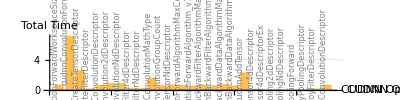

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize"||
#2==="cudnnDestroyTensorDescriptor",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log

```mathematica
data=Import["~/cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7501) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]
]&,
{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

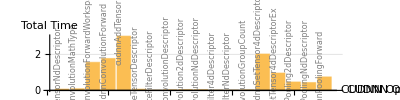

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log (Inception - Scratch)

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_log_parser/_fixtures/alexnet_cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7501) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
Length[durations]
```

952

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;-100]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#1]
]&,
{durations,funcs}][[400;;-100]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

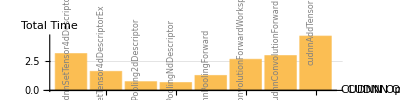

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;-100]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log2 (SCRATCH)

```mathematica
data=Import["~/cudnn.log","Text"];
```

```mathematica
Select[Select[StringTrim/@StringSplit[data,"I! CuDNN (v7501) function "],#=!=""&],StringStartsQ[#,"cudnnAddTensor"]&]
```

{cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.367743 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.397321 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.447056 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.492127 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.526016 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.529206 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.529940 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.530596 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.531112 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.531631 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.532972 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.533334 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.533676 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.533916 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.534161 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.535464 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.535835 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.536175 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.536388 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.536601 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.537869 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.538235 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.538574 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.538786 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.538997 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.540237 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.540600 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.540943 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.541157 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.541364 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.542590 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.542952 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.543293 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.543508 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.543722 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.545092 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.545460 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.545849 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.546071 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.546280 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.547626 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.547987 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.548326 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.548537 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.548748 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.550006 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.550368 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.550709 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.550923 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.551135 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.552351 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.552713 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.553052 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.553263 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.553479 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.554827 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.555187 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.555526 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.555739 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.555950 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.}

## CUDNN Log using parser (Alexnet)

```mathematica
rawdata=Select[
Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_log_parser/_fixtures/alexnet_cudnn.csv"],
Length[#]==3&
];
rawdata=Apply[Rule,rawdata[[2;;,;;2]],{1}][[5;;-100]];
```

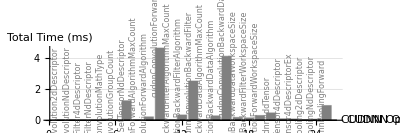

```mathematica
data=Merge[rawdata,Total];
BarChart[
KeyValueMap[
Function[{k,v},
If[StringContainsQ[k,"cudnnDestroy"]||StringContainsQ[k,"cudnnCreate"],
Nothing,
Labeled[v/12,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
]
],
data
],
ChartStyle->Gray,
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/3,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time (ms)"}
]
```

```mathematica
funcs=Union[First/@rawdata];
With[{ufuncs=funcs},
colorOf[func_]:=Darker[ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]]
];
```

```mathematica
ListPlot[
Map[If[#[[2]]<0.1||StringContainsQ[#[[1]],"cudnnDestroy"]||StringContainsQ[#[[1]],"cudnnCreate"],Nothing,Tooltip[Callout[Style[#[[2]],colorOf[#[[1]]]],#[[1]]],#[[1]]]]&,rawdata],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

get the total time

```mathematica
KeyValueMap[
Function[{k,v},
If[StringContainsQ[k,"cudnnDestroy"]||StringContainsQ[k,"cudnnCreate"]||StringContainsQ[k,"cudnnGetCon"],
Nothing,
v/12
]
],
data
]//Total
```

15.4031

## Plot our recall time ResNet50-v1 Animate

```mathematica
Manipulate[
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_"<>ToString[batchSize]<>"/Tesla_V100-SXM2-16GB/ResNet050-v1.csv","CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
layerData=100*(Total[Lookup[#,"RealTime(ms)"]]&/@GroupBy[data,#["LayerType"]&])/Total[Lookup[data,"RealTime(ms)"]];
PieChart[layerData,ChartLabels->Keys[layerData],PlotLabel->("Batch Size"<>ToString[batchSize])],
{batchSize,2^Range[0,4]}
]
```

## Plot our recall time

```mathematica
data=Import["/tmp/e.json","RawJSON"];
```

```mathematica
nameOf[elem_]:=StringSplit[elem["benchmark"]["Name"],"_FLOAT32__"][[1]];
timeOf[elem_]:=elem["benchmark"]["RealTime"];
```

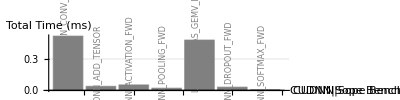

```mathematica
BarChart[
KeyValueMap[
Function[{k,v},
If[ToLowerCase[k]=="total",
Nothing,
Labeled[v/1000000,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
]
],
Merge[Map[nameOf[#]->timeOf[#]&,data],Total]
],
ChartStyle->Gray,
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN|Sope Bench","Total Time (ms)"}
]
```

## Distribution of Conv Algorithms

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/v100/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
```

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
```

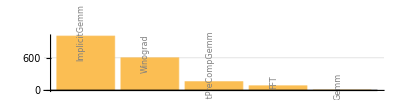

```mathematica
hist=Reverse[Sort[Counts[Lookup[convLayers,"advised_convolution_algorithm"]]]];
BarChart[
KeyValueMap[Function[{k,v},
Labeled[v,Rotate[Style[convAlgorithmNames[Floor[k]],Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

## Predicting Conv Compute (all algorithms)

can we find a curve that predicts the time given some flops?

hopeless if you look at all the conv algorithms

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/v100/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
convLayers=Select[convLayers,#["predicted_flops_count"]>0&&#["advised_convolution_algorithm"]===#["convolution_algorithm"]&];
```

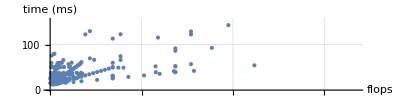

```mathematica
ListPlot[
Transpose[{Lookup[convLayers,"predicted_advised_flops_count"],Lookup[convLayers,"real_time"]/1000}],
AxesLabel->{"flops","time (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]
]
```

## Predicting Conv Compute (Implicit Gemm)

can we find a curve that predicts the time given some flops?

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/k80/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
convLayers=Select[convLayers,#["predicted_flops_count"]>0&&#["advised_convolution_algorithm"]===0.&];
```

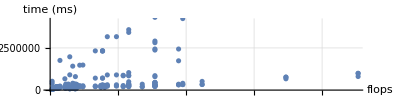

```mathematica
ListPlot[
Transpose[{Lookup[convLayers,"predicted_advised_flops_count"],Lookup[convLayers,"real_time"]}],
AxesLabel->{"flops","time (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]
]
```

```mathematica
nCrossValidation[dataset0_,n_]:=Module[{dataset=RandomSample[dataset0], trainSet,testSet,size,i,res={},c},size=IntegerPart[Length[dataset]/n];
For[i=0,i<n,i++,trainSet=Join[dataset[[1;;i*size]],dataset[[(i+1)*size+1;;]]];
testSet=dataset[[i*size+1;;(i+1)*size]];
AppendTo[res,<|"train"->trainSet,"test"->testSet|>]
];
res
]
```

```mathematica
info=Table[
<|
"flops"->Lookup[layer,"predicted_advised_flops_count"],
"time"->Quantity[Lookup[layer,"real_time"],"ms"]
|>,
{layer,convLayers}
];
```

```mathematica
nCross=nCrossValidation[info,5];
```

### Using nearest (a simple example)

```mathematica
trinfo=nCross[[1]]["train"];
nfinfo=Apply[Rule,Lookup[trinfo,{"flops","time"}],{1}];
train=Association[nfinfo];
nf=Nearest[Keys[train]]
```

NearestFunction[…]

```mathematica
test=nCross[[1]]["test"];
```

```mathematica
t1=test[[1]]
```

<|flops→8.30669×10^6,time→28922.2 ms|>

```mathematica
f=nf[t1["flops"],4];
AssociationThread[f->Lookup[train,f]]
```

<|8.42957×10^6→119362. ms,8.02816×10^6→115938. ms,8.83098×10^6→123595. ms,7.66771×10^6→137408. ms|>

```mathematica
closestFlops=nf[t1[[1]],1][[1]];
closestTime=Lookup[train,closestFlops]
```

119362. ms

```mathematica
testFlop=t1["flops"];
```

```mathematica
<|"closestFlops"->closestFlops,
"closestTime"->closestTime,
"targetFlop"->targetFlop,
"targetTime"->t1[[1]]
|>
```

<|closestFlops→8.42957×10^6,closestTime→119362. ms,targetFlop→28922.2,targetTime→8.30669×10^6|>

```mathematica
closestTime*(targetFlop/closestFlops)
```

409.537 ms

### Using nearest (full example)

```mathematica
trinfo=nCross[[1]]["train"];
nfinfo=Apply[Rule,Lookup[trinfo,{"flops","time"}],{1}];
train=Association[nfinfo];
nf=Nearest[Keys[train]]
```

NearestFunction[…]

```mathematica
testInstances=nCross[[1]]["test"];
testFlops=Lookup[testInstances,"flops"];
testActual=Lookup[testInstances,"time"];
closest=Flatten[nf[testFlops,1]];
predicted=Lookup[train,closest]*(closest/testFlops);
```

formula is predictedTime=predictedFlops closestTime/closestFlops

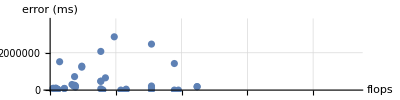

```mathematica
ListPlot[MapThread[List,{testFlops,Abs[predicted-testActual]}],
AxesLabel->{"flops","error (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]]
```

### Using gradient boosting

```mathematica
predictionData=Rule@@Transpose[Values[nCross[[1]]["train"]]];
```

```mathematica
pred=Predict[predictionData,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
testInstances=nCross[[1]]["test"];
testFlops=Lookup[testInstances,"flops"];
testTimes=Lookup[testInstances,"time"];
```

```mathematica
Abs[testTimes-(pred/@testFlops)][[;;10]]
```

{532251. ms,618728. ms,3.99049×10^7 ms,682942. ms,173082. ms,1.32925×10^6 ms,2.93553×10^6 ms,473687. ms,439026. ms,212375. ms}

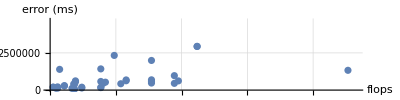

```mathematica
ListPlot[Transpose[{testFlops,Abs[testTimes-(pred/@testFlops)]}],
AxesLabel->{"flops","error (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]]
```

## Obfuscation

```mathematica
net=NetModel["Inception V1 Trained on ImageNet Competition Data"];
net=NetFlatten[net];
layers=net[[All]];
```

```mathematica
layers[[1]]
```

ConvolutionLayer[<>]

```mathematica
layerInfos=Select[
Table[
Prepend[
Association[
KeyValueMap[
Function[{k,v},
k[[1]]->v
],
NetInformation[layer,"ArraysDimensions"]
]],
"Type"->Head[layer]
],
{layer,layers}
],
KeyExistsQ["Weights"]
];
```

```mathematica
weightsData=GroupBy[Select[Union[Lookup[layerInfos,"Weights"]],Length[#]>2&],Take[#,-3]&]
```

<|{192,1,1}→{{16,192,1,1},{32,192,1,1},{64,192,1,1},{96,192,1,1}},{480,1,1}→{{16,480,1,1},{64,480,1,1},{96,480,1,1},{192,480,1,1}},{512,1,1}→{{24,512,1,1},{32,512,1,1},{64,512,1,1},{112,512,1,1},{128,512,1,1},{144,512,1,1},{160,512,1,1}},{16,5,5}→{{32,16,5,5},{48,16,5,5}},{256,1,1}→{{32,256,1,1},{64,256,1,1},{128,256,1,1}},{528,1,1}→{{32,528,1,1},{128,528,1,1},{160,528,1,1},{256,528,1,1}},{832,1,1}→{{32,832,1,1},{48,832,1,1},{128,832,1,1},{160,832,1,1},{192,832,1,1},{256,832,1,1},{384,832,1,1}},{3,7,7}→{{64,3,7,7}},{24,5,5}→{{64,24,5,5}},{32,5,5}→{{64,32,5,5},{96,32,5,5},{128,32,5,5}},{64,1,1}→{{64,64,1,1}},{48,5,5}→{{128,48,5,5}},{96,3,3}→{{128,96,3,3},{208,96,3,3}},{64,3,3}→{{192,64,3,3}},{128,3,3}→{{192,128,3,3},{256,128,3,3}},{112,3,3}→{{224,112,3,3}},{144,3,3}→{{288,144,3,3}},{160,3,3}→{{320,160,3,3}},{192,3,3}→{{384,192,3,3}}|>

```mathematica
Map[First,
weightsData,
{2}
]
```

<|{192,1,1}→{16,32,64,96},{480,1,1}→{16,64,96,192},{512,1,1}→{24,32,64,112,128,144,160},{16,5,5}→{32,48},{256,1,1}→{32,64,128},{528,1,1}→{32,128,160,256},{832,1,1}→{32,48,128,160,192,256,384},{3,7,7}→{64},{24,5,5}→{64},{32,5,5}→{64,96,128},{64,1,1}→{64},{48,5,5}→{128},{96,3,3}→{128,208},{64,3,3}→{192},{128,3,3}→{192,256},{112,3,3}→{224},{144,3,3}→{288},{160,3,3}→{320},{192,3,3}→{384}|>

## Using our layer information data to only look at inner loops

-Graphics-

essentially, if we take N as fixed, then we can just say that a layer is pK with p as a parameter. So we can ignore k and decrease the number of unique layers

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/inception-v1.json","RawJSON"];
```

```mathematica
shapeinfo=Map[Most,Lookup[Lookup[Select[data,#["type"]==="Conv"&],"input_dimensions"],"input_shapes"]];
```

```mathematica
N[Length[Union[shapeinfo]]/Length[shapeinfo]]
```

0.859649

```mathematica
tshapeinfo=Map[
{#[[1,2;;]],#[[2,2;;]]}&,
shapeinfo
];
```

```mathematica
N[Length[Union[tshapeinfo]]/Length[shapeinfo]]
```

0.438596

## Theoretical vs Predicted flops

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
algorithms={"ImplicitGemm",
"ImplicitPreCompGemm",
"Gemm",
"Direct",
"FFT",
"FFTTiling",
"Winograd",
"WinogradNonFused"};
shortenLabel["ImplicitPreCompGemm"]:="ImplicitGemm";
shortenLabel[s_]:=s;
```

This plot compares the algorithm against the theoretical flops

```mathematica
<<GeneralUtilities`
```

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/v100/16/ResNet050-v1.json","RawJSON"];
data=Select[data,#["layer"]["operator_type"]==="Conv"&];
```

```mathematica
info=Table[
time=elem["benchmark"];
If[MissingQ[time]||time["convolution_algorithm"]=!=time["advised_convolution_algorithm"]||time["predicted_flops"]<10,
Nothing,
Labeled[{
Tooltip[
v100PeekGflop*time["RealTime"]/10.0^6,
InformationPanel["configuration",Normal[time]]
],
Tooltip[
time["predicted_flops"]/10.0^9,
InformationPanel["configuration",Normal[time]]
]
},
Rotate[Style[shortenLabel[time["convolution_algorithm"]],Gray,FontSize->8],90Degree],
Above
]
],
{elem,data}
];
```

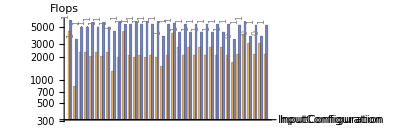

```mathematica
BarChart[info,
Ticks->{None,Automatic},
ScalingFunctions->"Log",
BarSpacing->{0,1},
AspectRatio->1/3,
ImageSize->Scaled[0.75],
AxesLabel->{"InputConfiguration","Flops"},
ChartLegends->{"measured","predicted"}]
```

Each group represents an input configuration. The y axis is the flops it takes to compute the task (the actual flops are ones that are measured and the predicted and the ones computed)

```mathematica
ndata=info/.Tooltip[x_,__]:>x/.Labeled[x_,__]:>x
```

{{4382.14,6032.45},{835.996,3441.74},{2323.05,4954.32},{2323.05,4954.32},{2056.88,5595.43},{2323.05,4954.32},{2056.88,5595.43},{2323.05,4954.32},{1319.12,4362.39},{1997.76,5761.04},{4303.36,5348.91},{2125.42,5414.98},{1997.76,5761.04},{2125.42,5414.98},{1997.76,5761.04},{2125.42,5414.98},{1997.76,5761.04},{1527.65,3766.93},{2134.09,5393.01},{4133.33,5568.95},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{1692.71,3399.61},{2189.6,5256.27},{3998.33,5756.99},{3045.7,3778.82},{2189.6,5256.27},{3045.7,3778.82},{2189.6,5256.27}}

```mathematica
Max[ndata]
```

6032.45

```mathematica
ExportString[Table[Prepend[ndata[[ii]],ii],{ii,Length[ndata]}],"CSV"]//CopyToClipboard
```

### Normalized

```mathematica
Max[ndata[[All,2]]/ndata[[All,1]]]
```

4.11693

```mathematica
ExportString[Table[Prepend[{1,ndata[[ii,2]]/ndata[[ii,1]]},ii],{ii,Length[ndata]}],"CSV"]//CopyToClipboard
```

## Total Time for batchsize 1 on v100

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_1/Tesla_V100-SXM2-16GB/";
files=FileNames["*.json",dir];
nets=Table[
net=Import[file,"RawJSON"];
totalEntry=SelectFirst[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]==="Total"]];
{FileBaseName[file],totalEntry["benchmark"]["RealTime"]/10.0^6},
{file,files}
];
```

```mathematica
ExportString[nets,"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]
```

9.600726
0.5685669999999999
0.569263
3.621218
0.543295
9.754686
164.900007
0.97136
3.604634
5.763496
0.08857899999999999
1.975898
1.803529
1.8276109999999999
3.336483
3.360565
4.726749
4.765897
9.175955
8.921733999999999
13.476789
12.921546999999999
0.829888
1.1322269999999999
1.460134
3.353847
2.852748
4.113766
3.55388
1.260626

```mathematica
Grid[nets,Frame->All]
```

ArcFace | 9.60073
BVLC_AlexNet | 0.568567
BVLC_CaffeNet | 0.569263
BVLC_GoogleNet | 3.62122
BVLC_RCNN_ILSVRC13 | 0.543295
DenseNet-121 | 9.75469
DUC | 164.9
Emotion-FerPlus | 0.97136
Inception-v1 | 3.60463
Inception-v2 | 5.7635
MNIST | 0.088579
MobileNet-v2 | 1.9759
ResNet018-v1 | 1.80353
ResNet018-v2 | 1.82761
ResNet034-v1 | 3.33648
ResNet034-v2 | 3.36057
ResNet050-v1 | 4.72675
ResNet050-v2 | 4.7659
ResNet101-v1 | 9.17596
ResNet101-v2 | 8.92173
ResNet152-v1 | 13.4768
ResNet152-v2 | 12.9215
Shufflenet | 0.829888
Squeezenet-v1.1 | 1.13223
Tiny_YOLO-v2 | 1.46013
VGG16-BN | 3.35385
VGG16 | 2.85275
VGG19-BN | 4.11377
VGG19 | 3.55388
Zfnet512 | 1.26063

## Scratch Timing

id | name | mxnet | our
0 | ArcFace | 9.4847 | 9.60073
1 | BVLC_AlexNet | 1.12915 | 0.568567
2 | BVLC_CaffeNet | 1.10331 | 0.569263
3 | BVLC_GoogleNet | 4.57878 | 3.62122
4 | BVLC_RCNN_ILSVRC13 | 1.04244 | 0.543295
5 | DenseNet-121 | 13.2721 | 9.75469
6 | DUC | 25.0651 | 164.9
8 | Inception-v1 | 4.20809 | 3.60463
9 | Inception-v2 | 5.44679 | 5.7635
11 | MobileNet-v2 | 2.7437 | 1.9759
12 | ResNet018-v1 | 1.94492 | 1.80353
13 | ResNet018-v2 | 2.0185 | 1.82761
14 | ResNet034-v1 | 3.175 | 3.33648
15 | ResNet034-v2 | 3.25832 | 3.36057
16 | ResNet050-v1 | 4.5454 | 4.72675
17 | ResNet050-v2 | 4.62861 | 4.7659
18 | ResNet101-v1 | 8.91621 | 9.17596
19 | ResNet101-v2 | 8.17084 | 8.92173
20 | ResNet152-v1 | 11.7995 | 13.4768
21 | ResNet152-v2 | 11.7474 | 12.9215
22 | Shufflenet | 3.05011 | 0.829888
23 | Squeezenet-v1.1 | 1.29426 | 1.13223
25 | VGG16-BN | 4.00224 | 3.35385
26 | VGG16 | 3.55844 | 2.85275
27 | VGG19-BN | 4.66921 | 4.11377
28 | VGG19 | 4.32878 | 3.55388
29 | Zfnet512 | 1.56591 | 1.26063

## Total Time for batchsize 8 on v100

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_8/Tesla_V100-SXM2-16GB/";
files=FileNames["*.json",dir];
nets=Table[
net=Import[file,"RawJSON"];
totalEntry=SelectFirst[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]==="Total"]];
{FileBaseName[file],totalEntry["benchmark"]["RealTime"]/10.0^6},
{file,files}
];
```

```mathematica
ExportString[nets,"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]
```

18.741360999999998
0.9091239999999999
0.9166789999999999
5.6753849999999995
0.8903869999999999
9.779988
1164.151998
1.586249
3.5878729999999996
8.675227999999999
0.088991
4.071515
3.798536
3.869029
6.736896
6.807389
11.456199
11.441782
20.467779999999998
19.946882
29.855269
28.770705999999997
1.035539
2.060339
5.702405
17.522924
15.201649
21.376624
18.82472
2.857265

## ArcFace on V100 with BatchSize=8 Graph

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/v100/8/ArcFace.json";
net=Import[file,"RawJSON"];
```

Ignore the total entry

```mathematica
data=Select[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]=!="Total"]];
```

Build graph

```mathematica
verts=Union[Flatten[Lookup[Lookup[data,"layer"],{"input_names","output_names"}]]];
```

```mathematica
edges=Union@Flatten[
Table[
Table[
inputName->outputName,
{inputName,Lookup[layer,"input_names"]},
{outputName,Lookup[layer,"output_names"]}
],
{layer,Lookup[data,"layer"]}
]
];
```

```mathematica
vertexTimes=Association[Table[elem["layer"]["name"]->elem["benchmark"]["RealTime"]/10.0^6,{elem,data}]];
vertexType=Association[Table[elem["layer"]["name"]->elem["layer"]["operator_type"],{elem,data}]];
totalVertTimes=Total[Values[vertexTimes]];
vertexTimes=Map[#/totalVertTimes&,vertexTimes];
numClusters=10;
clusters=FindClusters[vertexTimes,numClusters];
clusterMapping=Association[Flatten[Table[Table[elem->ii,{elem,clusters[[ii]]}],{ii,Length[clusters]}]]];
clusterSizes=Association[Table[ii->Scaled[0.5-ii*0.1],{ii,numClusters}]];
vertexShapes=KeyValueMap[Function[{k,v},k->(Tooltip[Disk[#1,0.1v],vertexType[k]]&)],clusterMapping];
```

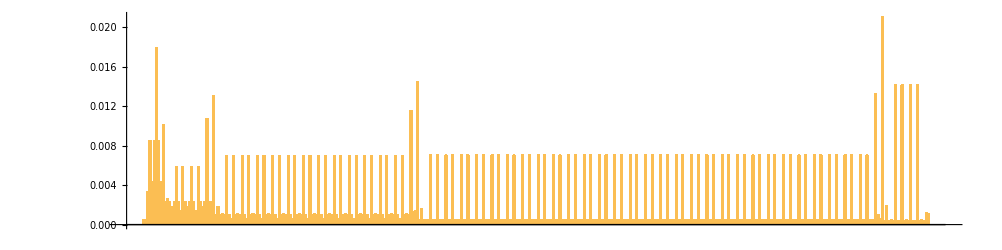

```mathematica
BarChart[vertexTimes,AspectRatio->1/4,ImageSize->Scaled[0.75]]
```

```mathematica
gr=Graph[verts,edges,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top},EdgeShapeFunction->"Line", ImagePadding->15,VertexLabels->Placed["Name",Before],VertexShapeFunction->vertexShapes,ImageSize->{Scaled[0.75]}];
```

vertices with in degree = 1

```mathematica
inputVerts=Table[If[VertexInDegree[gr,vert]===0,vert,Nothing],{vert,VertexList[gr]}];
```

delete the input verts

```mathematica
grt=VertexDelete[gr,inputVerts];
grt=WeaklyConnectedGraphComponents[grt][[1]];
```

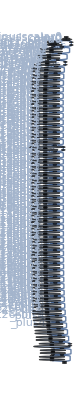

```mathematica
grt
```

## Theoretical vs CUPTI Actual for ResNet50

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
MapThread[Function[{layer,theoretical,actual},
{Tooltip[Labeled[theoretical,Style[N[actual/theoretical],Gray,FontSize->8],Above ],layer],Tooltip[actual,layer]}
],
{layerNames,theoreticalFlops,cuptiSPFlops}
]
```

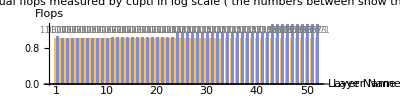

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
sflopsPos=First@FirstPosition[header,"flop_count_sp"];
rows=Select[Rest[rdata],#[[2]]==="Conv"&];
theoreticalFlops=rows[[All,tflopsPos]];
cuptiSPFlops=rows[[All,sflopsPos]];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[First/@GroupBy[rows[[All,{layerNamePos,tflopsPos,sflopsPos}]],First]];
(*data[[All,1]]/=2;*)
BarChart[
plotData=MapThread[Function[{layer,theoretical,actual},
{Tooltip[Labeled[theoretical/theoretical,Style[N[actual/theoretical],Gray,FontSize->8],Above ],N[actual/theoretical]],Tooltip[actual/theoretical,layer]}
],
Prepend[Transpose@data,layerNames]
],
AxesLabel->{"Layer Name","Flops"},
(*PlotTheme->"Grid",*)
Ticks->{None,Automatic} ,
PlotLabel->"Comparison between the theortical total flops and the actual flops measured by cupti in log scale \n( the numbers between show the times different between the actual and theoretical)",
AspectRatio->1/4,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
BarSpacing->{0,1},
(*ScalingFunctions->"Log",*)
ChartLegends->{"theortical","cupti(actual)"},
ImageSize->{Scaled[0.75],Scaled[2]},
Ticks->{None,Automatic}(*,
BarOrigin->Left*)
]
```

## CUPTI Actual Decomposition for ResNet50

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

```mathematica
ClearAll[hatchF]
hatchF[mf_List:{#&,#2&},mesh_List:{50,50},style_:GrayLevel[.5],opts:OptionsPattern[]]:=ParametricPlot[{x,y},{x,0,1},{y,0,1},Mesh->mesh,MeshFunctions->mf,MeshStyle->style,BoundaryStyle->None,opts,Frame->False,PlotRangePadding->0,ImagePadding->0,Axes->False]
```

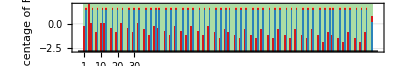

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
colors={RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]};
(*colors={Black,Gray,Darker@Gray,LightGray};*)
fig=BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Percentile",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

```mathematica
Export["/Users/abduld/Desktop/resnet50_metrics.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/resnet50_metrics.pdf

## CUPTI Actual Decomposition for ResNet50 (Theoretical Latency) -- counts cycles

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

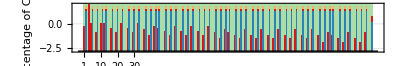

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Percentile",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Cycles",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

```mathematica
Export["/Users/abduld/Desktop/resnet50_cycles.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/resnet50_cycles.pdf

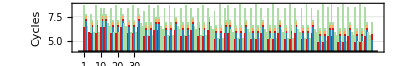

```mathematica
BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Stacked",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Cycles",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## CUPTI Actual Decomposition for Tiny Yolo

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

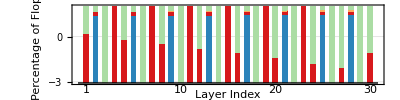

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Tiny_YOLO-v2.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Tiny Yolo (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

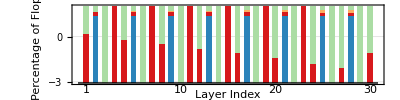

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Tiny_YOLO-v2.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Emotion-FerPlus

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

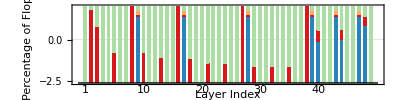

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Emotion-FerPlus.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Emotion-FerPlus (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

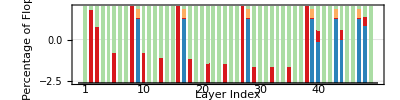

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Emotion-FerPlus.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for DUC

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

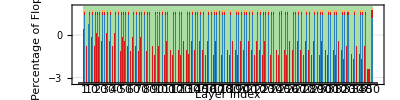

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","DUC.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for DUC (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

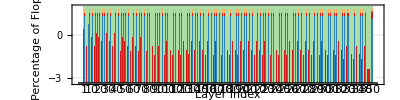

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","DUC.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## Kernel Names for ResNet50 for V100

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --kernels_only=true --trim_layer_name=false

```mathematica
rawData=;
data=Rest[ImportString[rawData,"CSV"]];
```

```mathematica
layerNames=data[[All,1]];
kernelNames=Flatten[StringSplit[#,";"]]&/@data[[All,3;;]];
```

```mathematica
mapping=AssociationThread[layerNames->kernelNames];
```

```mathematica
maxColumns=Max[Length/@kernelNames]+1;
paddedList=MapThread[Module[{lst=Flatten[{#1,#2}]},PadRight[lst,maxColumns,""]]&,{layerNames,kernelNames}];
```

```mathematica
ExportString[paddedList,"CSV"]//CopyToClipboard
```

example pasted in gist https://gist.github.com/abduld/fa24725370da54905ee041d44275da15

```mathematica
Dataset[paddedList]
```

## Theoretical vs Actual Flops for models

generate data using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ --benchmark_database results/k80/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=./assets/flop_count_sp/batchsize_8/k80 --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/flop_count_sp";
v100=Import[#,"CSV"]&/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","v100"}]];
k80=Import[#,"CSV"]&/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","k80"}]];
```

```mathematica
(FileBaseName/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","v100"}]])[[12]]
```

MobileNet-v2

```mathematica
v100[[1,1]]
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp}

```mathematica
theoreticalFlops=Total[Rest[#[[All,-2]]]]&/@k80;
```

```mathematica
v100Flops=Total[Rest[#[[All,-1]]]]&/@v100;
k80Flops=Total[Rest[#[[All,-1]]]]&/@k80;
```

```mathematica
Grid[MapThread[List,{Range[Length[k80Flops]],N[k80Flops/(1024*1024)],N[theoreticalFlops/(1024*1024)]}],Frame->All]
```

1 | 23122.7 | 20582.8
2 | 2150.86 | 2386.31
3 | 2377.45 | 2638.34
4 | 3316.21 | 6041.67
5 | 2370.88 | 2632.08
6 | 6154.08 | 5512.95
7 | 1.37235×10^6 | 1.20834×10^8
8 | 1535.02 | 1673.49
9 | 3043.27 | 5464.75
10 | 4377.57 | 3882.89
11 | 2.7493 | 1.52717
12 | 17707. | 15685.6
13 | 3888.88 | 3469.93
14 | 3890.39 | 3470.65
15 | 7849.69 | 7003.31
16 | 7851.2 | 7004.03
17 | 8458.36 | 10316.8
18 | 8881.21 | 7842.47
19 | 16668. | 20752.1
20 | 17085.5 | 14945.7
21 | 24703.4 | 31192.7
22 | 25114.7 | 22054.4
23 | 5455. | 265.868
24 | 759.017 | 1337.01
25 | 5203.97 | 6024.08
26 | 18336.2 | 58638.3
27 | 18090.7 | 58612.4
28 | 23388.3 | 74519.2
29 | 23119.2 | 74490.9
30 | 3043.29 | 5501.31

```mathematica
ExportString[MapThread[List,N@{Range[Length[k80Flops]],k80Flops/theoreticalFlops,v100Flops/theoreticalFlops,theoreticalFlops/theoreticalFlops}],"CSV"]
```

1.,1.1233985373719786,1.1252306121129703,1.
2.,0.9013336177178585,0.8745073636609445,1.
3.,0.9011159641629742,0.8769230843748765,1.
4.,0.5488895660466598,0.5548915038230001,1.
5.,0.9007610165328085,0.8766031598280664,1.
6.,1.116296319170699,1.1197414136369013,1.
7.,0.011357341455946721,0.011014349308507965,1.
8.,0.9172559980157144,0.9185421275773344,1.
9.,0.5568910929183,0.5662941682833013,1.
10.,1.127400280318708,1.1068703314436934,1.
11.,1.8002590307951896,1.8041270075198863,1.
12.,1.1288704908559513,1.114757440691444,1.
13.,1.12073758377426,1.1629858966336557,1.
14.,1.1209405296525783,1.1632352550564489,1.
15.,1.1208541435553363,1.1419152933327013,1.
16.,1.1209546956310483,1.1420410150781761,1.
17.,0.8198647221781035,0.8587303261524115,1.
18.,1.132450254355983,1.1847613819072786,1.
19.,0.8031951995765192,0.8231242345440648,1.
20.,1.1431668890653464,1.1707260358052396,1.
21.,0.7919617512546712,0.805746063834971,1.
22.,1.138762307089317,1.1575542973109523,1.
23.,20.517737745096493,19.181463432733757,1.
24.,0.5676974686573635,0.5750461073139608,1.
25.,0.8638620106843811,0.928062256875649,1.
26.,0.31270029560381357,0.39533394109112086,1.
27.,0.3086499874683109,0.39132006278128534,1.
28.,0.31385552322967897,0.39850232375939165,1.
29.,0.3103621274384002,0.3950411182713966,1.
30.,0.5531933040325133,0.5542203869091742,1.

```mathematica
ExportString[MapThread[List,{k80Flops,v100Flops,theoreticalFlops}],"CSV"]
```

24245895424,24285436416,21582630400
2255341408,2188216028,2502227104
2492935008,2426005468,2766497440
3477295530,3515318682,6335145984
2486046396,2419372160,2759940040
6453025464,6472940680,5780745984
1439014779488,1395556477972,126703488230032
1609582172,1611839046,1754779664
3191102170,3244983754,5730208672
4590213380,4506625636,4071502784
2882852,2889046,1601354
18567096712,18334972328,16447499392
4077785704,4231505512,3638483944
4079367784,4233288296,3639236584
8230997864,8385660520,7343504872
8232579944,8387443304,7344257512
8869237672,9289682984,10817928168
9312622632,9742799400,8223427560
17477615528,17911273512,21760109544
17915429928,18347330088,15671753704
25903414184,26354270248,32707910632
26334674984,26769252904,23125699560
5719985156,5347455332,278782448
795886559,806189023,1401955448
5456758628,5862292432,6316701696
19226902704,24307771140,61486679016
18969499824,24050368260,61459583976
24524384944,31138608900,78139089896
24242195120,30856419076,78109385704
3191117348,3197042116,5768539360

## ResNet50 Analysis

Generated using

go run main.go benchinfo --model_path /Users/abduld/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/Tesla_V100-SXM2-16GB/profile/1.json --short=false --batch_size=1 --human=false --strategy=parallel --metrics --output_file=test.json --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=json --trim_layer_name=fal
se

```mathematica
data=;
```

```mathematica
Keys@data[[1]]
```

{type,benchmark,flops_information}

```mathematica
Lookup[Lookup[data,"benchmark"],{"Name","Flops"}]
```

{{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10561411637126037500<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:3/input[2]:224/input[3]:224/filter_count:64/filter_height:7/filter_width:7/pad_height:3/pad_width:3/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,118013952},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8485617627681512661<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8731790411514196767<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_POOLING_FWD_FLOAT32__BatchSize_1__8317600655594697260<CUDNN_POOLING_MAX>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:2/stride_width:2/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__17452696648446571200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,12845056},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__6271735633126097759/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8887210388371323745<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16026190895114242814/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8887210388371323745<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16026190895114242814/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__2698634678934534712<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__9245529975646030759/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9900471406965659822<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__5696751150347348050<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16875882305802639821/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__2863503841521678117<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10645803091547187777<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__3927346633012288478/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10357631549930852067<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9173660249711801802<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15740821849914442837/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9173660249711801802<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15740821849914442837/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUBLAS_GEMV_FWD_FLOAT32__BatchSize_1__1841169376419394758/input[0]:1000/input[1]:2048/input[2]:1/input[3]:1/input[4]:1/input[5]:-1/input[6]:0/input[7]:0/batch_size:1/iterations:10/manual_time,2048000}}

## MXNet Padding Overhead

```mathematica
profile=Import["/tmp/e.json","RawJSON"]["traceEvents"];
```

```mathematica
gpuPid=SelectFirst[profile,Lookup[Lookup[#,"args",<||>],"name",None]==="gpu/0"&]["pid"]
```

8

```mathematica
allTimeSpans=Select[profile,Lookup[#,"pid"]==gpuPid&&KeyExistsQ[#,"ts"]&];
padTimeSpans=Select[profile,Lookup[#,"name"]==="Pad"&&Lookup[#,"pid"]==gpuPid&];
```

```mathematica
allTime=N@Total[
MapThread[
#2["ts"]-#1["ts"]&,
Transpose[Partition[allTimeSpans,2]]
]
]
```

171730.

```mathematica
padTime=N@Total[
MapThread[
#2["ts"]-#1["ts"]&,
Transpose[Partition[padTimeSpans,2]]
]
]
```

1010.

```mathematica
padTime/allTime
```

0.0639119

## Onnx Runtime Results

```mathematica
Manipulate[
Module[{},
batchSize=ToString[bs];
csvFiles=FileNames["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/*_"<>batchSize<>".csv"];
data=Association[Table[
name=StringTrim[FileBaseName[file],"_"<>batchSize];
content=Import[file,"Text"];
content=StringRiffle[Select[StringSplit[content,"\n"],StringMatchQ[#,StartOfString~~DigitCharacter..~~","~~___]&],"\n"];
content=ImportString[content,"CSV"];
content=AssociationThread[content[[All,1]]->content[[All,2;;]]];
name->content
,{file,csvFiles}
]];
data2=data;
data=Table[Last[Lookup[#,model,{0}]]&/@data,{model,Range[0,29]}];
BarChart[Values/@data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[0,29],5]],0],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Model Index",14],Style["Latency",14]},
ChartLegends->Placed[Keys[data[[1]]],Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]],
{bs,2^Range[0,8]}
]
```

```mathematica
data2["mxnet"][14]
```

{ResNet034-v1,290.773}

```mathematica
data[[16]]
```

<|caffe2→5.82931,mxnet→3.67742,onnxruntime→3.86598|>

## ResNet 34-v1

```mathematica
model=15;
batchSizes=2^Range[0,8];
```

```mathematica
ts=Association@Table[
batchSize=ToString[bs];
csvFiles=FileNames["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/*_"<>batchSize<>".csv"];
data=Association[Table[
name=StringTrim[FileBaseName[file],"_"<>batchSize];
content=Import[file,"Text"];
content=StringRiffle[Select[StringSplit[content,"\n"],StringMatchQ[#,StartOfString~~DigitCharacter..~~","~~___]&],"\n"];
content=ImportString[content,"CSV"];
content=AssociationThread[content[[All,1]]->content[[All,2;;]]];
name->content
,{file,csvFiles}
]];
data2=data;
data=Last[Lookup[#,model,{0}]]&/@data;
bs->data,
{bs,batchSizes}
];
```

```mathematica
frameworks=Keys[ts[1]]
```

{caffe2,mxnet,onnxruntime}

```mathematica
ts
```

<|1→<|caffe2→5.43201,mxnet→3.25832,onnxruntime→3.45395|>,2→<|caffe2→5.82931,mxnet→3.67742,onnxruntime→3.86598|>,4→<|caffe2→6.57687,mxnet→4.60899,onnxruntime→4.76716|>,8→<|caffe2→9.99315,mxnet→7.93002,onnxruntime→8.27951|>,16→<|caffe2→15.6991,mxnet→12.1723,onnxruntime→13.7484|>,32→<|caffe2→27.6339,mxnet→21.498,onnxruntime→26.7169|>,64→<|caffe2→45.2183,mxnet→44.8094,onnxruntime→70.7363|>,128→<|mxnet→88.1913,onnxruntime→91.4276|>,256→<|mxnet→171.436,onnxruntime→276.004|>|>

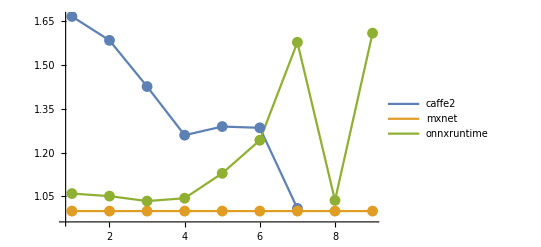

```mathematica
ListLinePlot[
Table[
Lookup[ts[bs],framework]/Lookup[ts[bs],"mxnet"]
,
{framework,frameworks},
{bs,batchSizes}
],
Mesh->All,
PlotRange->Full,
(*ScalingFunctions->"Log2",*)
PlotLegends->frameworks,
ImageSize->Scaled[0.75]
]
```

## Batch Optimization

finding the best convolution parameters / decomposition.

when we see a conv layer, we find the best entry in the database that matches its dimensions.
But this may not be the fastest way to run the convolution algorithm.

conv = find[NHWC]=2 find[N/2 HWC]

## Layer Unique % per Year Results

```mathematica
inputFile="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/layers_per_year.json";
rdata=Import[inputFile,"RawJSON"];
```

```mathematica
colors={RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]};
colors={Black,Gray};
```

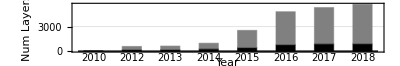

```mathematica
fig=Legended[
BarChart[
Transpose[{
Lookup[rdata,"unique"],
Lookup[rdata,"total"]-Lookup[rdata,"unique"]
}],
ChartLayout->"Stacked",
PlotTheme->"Grid",
Ticks->None,
ChartStyle->colors,
AspectRatio->1/6,
BarSpacing->{0,1},
Axes->{True,False},
(*ScalingFunctions->"Log10",*)
PlotRangePadding->None,
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
Frame->True,
ChartLabels->{Style[#,FontFamily->"Arial",FontColor->Black,FontSize->10]&/@Lookup[rdata,"year"],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Year",14],Style["Num Layers",14]},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
],
Placed[SwatchLegend[colors,Style[#,FontFamily->"Latin Modern Roman",FontSize->14]&/@{"Unique","Duplicate"},Background->Opacity[0.6,White],LegendLayout->"Row",LegendMarkerSize->10,LegendMargins->0,LabelStyle->{FontFamily->"Latin Modern Roman"}],{{0.6,0.95},{2.8,0.9}}]
]
```

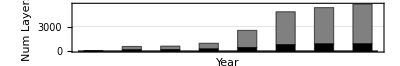

```mathematica
fig=BarChart[
Transpose[{
Lookup[rdata,"unique"],
Lookup[rdata,"total"]-Lookup[rdata,"unique"]
}],
ChartLayout->"Stacked",
PlotTheme->"Grid",
Ticks->None,
ChartStyle->colors,
AspectRatio->1/6,
BarSpacing->{0,1},
Axes->{True,False},
(*ScalingFunctions->"Log10",*)
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
ChartLabels->{Style[#,FontFamily->"Arial",FontColor->Black,FontSize->10]&/@Lookup[rdata,"year"],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Year",14],Style["Num Layers",14]},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10},
ChartLegends->Placed[SwatchLegend[colors,Style[#,FontFamily->"Latin Modern Roman",FontSize->14]&/@{"Unique","Duplicate"},Background->Opacity[0.6,White],LegendLayout->"Row",LegendMarkerSize->10,LegendMargins->0,LabelStyle->{FontFamily->"Latin Modern Roman"}],Above],
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1]
]
```

```mathematica
CloudExport[fig,"NB",Permissions->"Public",CloudObjectURLType->"Object"]
```

CloudObject[https://www.wolframcloud.com/obj/ceaa41a0-2e0f-4c5e-8be8-bb82f2c0b403]

```mathematica
pth=Export["/Users/abduld/Desktop/unique_layer_year.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/unique_layer_year.pdf

```mathematica
e=First@Import[pth,"PDF"];
e=e//.HoldPattern[ImageSize->x_]->(ImageSize->Scaled[0.75]);
CloudExport[e,"NB",Permissions->"Public",CloudObjectURLType->"Object"]
```

CloudObject[https://www.wolframcloud.com/obj/5bb64dc1-066c-4926-990f-e9d9650df577]

## Looking at Transformer Networks

```mathematica
gpt=NetFlatten@NetModel["GPT Transformer Trained on BookCorpus Data"];
gpt2=NetFlatten@NetModel["GPT-2 Transformer Trained on WebText Data"];
bert=NetFlatten@NetModel["BERT Trained on BookCorpus and English Wikipedia Data"];
```

```mathematica
ClearAll[proc,trimArraysConstant,inputs,inputs0];
trimArraysConstant[assoc0_]:=Module[{assoc=assoc0,arrays},
If[KeyExistsQ[assoc,"Arrays"],
arrays=Lookup[assoc,"Arrays"];
If[KeyExistsQ[arrays,"Scaling"],
AssociateTo[arrays,"Scaling"->Dimensions[Lookup[arrays,"Scaling"]]]
];
If[KeyExistsQ[arrays,"Weights"],
AssociateTo[arrays,"Weights"->Dimensions[Lookup[arrays,"Weights"]]]
];
If[KeyExistsQ[arrays,"Biases"],
AssociateTo[arrays,"Biases"->Dimensions[Lookup[arrays,"Biases"]]]
];
AssociateTo[assoc,"Arrays"->arrays];
assoc
]
];
proc[lyr_[assoc0_,r___]]:=Module[{assoc=assoc0,trimArrys,arrays,params,net},
If[KeyExistsQ[assoc,"Arrays"],
AssociateTo[assoc,"Arrays"->trimArraysConstant[Lookup[assoc,"Arrays"]]]
];
If[KeyExistsQ[assoc,"Parameters"]&&KeyExistsQ[Lookup[assoc,"Parameters"],"Arrays"],
AssociateTo[assoc,"Parameters"->Append[Lookup[Lookup[assoc,"Parameters"],"Arrays"],"Arrays"->trimArraysConstant[Lookup[Lookup[assoc,"Parameters"],"Arrays"]]]]
];
If[KeyExistsQ[assoc,"Parameters"]&&KeyExistsQ[Lookup[assoc,"Parameters"],"Net"],
params=Lookup[assoc,"Parameters"];
net=Lookup[params,"Net"];
If[KeyExistsQ[net,"Arrays"],
AssociateTo[net,"Arrays"->trimArraysConstant[Lookup[net,"Arrays"]]];
];
AssociateTo[params,"Net"->net];
AssociateTo[assoc,"Parameters"->params]
];
(*KeyDropFrom[assoc,"Inputs"];
KeyDropFrom[assoc,"Output"];*)
Inactive[lyr][assoc,r]
];
proc[atom_]:=
With[{hd=ToString[Head[atom]]},
proc@ToExpression[StringReplace[ToBoxes[InputForm@atom][[1,1]],hd->ToLowerCase[hd]]]
];
inputs0[lyr_[assoc_,___]]:=Module[{in=Values@Lookup[assoc,"Inputs"]},
in//.{
NeuralNetworks`TensorT[x___]:>{x},
NeuralNetworks`IndexIntegerT[x_]:>x,
NeuralNetworks`LengthVar[x_]:>x
}
];
inputs[lyr_[assoc_,___]]:=Module[{in=Lookup[assoc,"Inputs"]},
in
]
```

```mathematica
bertLyrs=NetExtract[bert,All];
bertLyrsProc=proc/@Values[bertLyrs];
bertLyerIns=inputs/@bertLyrsProc;
```

```mathematica
gptLyrs=NetExtract[gpt,All];
gptLyrsProc=proc/@Values[gptLyrs];
gptLyerIns=inputs/@gptLyrsProc;
```

```mathematica
gpt2Lyrs=NetExtract[gpt2,All];
gpt2LyrsProc=proc/@Values[gpt2Lyrs];
gpt2LyerIns=inputs/@gpt2LyrsProc;
```

```mathematica
Length[Join[bertLyrsProc,gptLyrsProc,gpt2LyrsProc]]
```

2551

```mathematica
Length[Union[Join[bertLyrsProc,gptLyrsProc,gpt2LyrsProc]]]
```

48

```mathematica
48./2551
```

0.0188162

```mathematica
N[Length[Union[gpt2LyrsProc]]/Length[gpt2LyrsProc]]
```

0.0168269

```mathematica
Length[Union[plyrs]]
```

19

```mathematica
lyrs//Length
```

862

```mathematica
Activate[lyrs[[20]]]
```

AttentionLayer[<>]

```mathematica
NetModel["GPT Transformer Trained on BookCorpus Data","ParametersInformation"]
```

```mathematica
lm=NetModel[{"GPT Transformer Trained on BookCorpus Data","Task"->"FeatureExtraction"}]
```

NetChain[<>]

```mathematica
NetInformation[Activate[lyrs[[20]]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
input=<|"Key"->RandomReal[1,{10,64}],"Value"->RandomReal[1,{10,64}],"Query"->RandomReal[1,{10,64}]|>;
lyr=Activate[lyrs[[20]]];
```

```mathematica
RepeatedTiming[ lyr[input];]
```

{0.00043,Null}

```mathematica
proc[lyrs[[20]]]
```

AttentionLayer[<|Type→Attention,Arrays→Null,Parameters→<|ScoringNet→<|Type→Graph,Inputs→<|Query→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT],Input→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{},NeuralNetworks`RealT]|>,Nodes→<|1→<|Type→Dot,Arrays→<||>,Parameters→<||>,Inputs→<|1→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT],2→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{},NeuralNetworks`RealT]|>|>|>,Edges→{NeuralNetworks`NetPath[Nodes,1,Inputs,1]→NeuralNetworks`NetPath[Inputs,Query],NeuralNetworks`NetPath[Nodes,1,Inputs,2]→NeuralNetworks`NetPath[Inputs,Input],NeuralNetworks`NetPath[Outputs,Output]→NeuralNetworks`NetPath[Nodes,1,Outputs,Output]}|>,Mask→None,ScoreRescaling→None,$InputPorts→KeyValueQuery,$InputShape→{NeuralNetworks`LengthVar[1234191656]},$QueryShape→{NeuralNetworks`LengthVar[1234191656]},$QueryChannels→{64},$KeyChannels→{64},$ValueChannels→{64}|>,Inputs→<|Key→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT],Value→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT],Query→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT]|>|>,<|Version→12.0.12,Unstable→False|>]

## Make Draw Dot CMD

```mathematica
models=Select[
FileNames["*.onnx","~/data/carml/dlperf/",Infinity],
!StringStartsQ[FileBaseName[#],"."]&
]
```

{~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx,~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx,~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx,~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx,~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx,~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx,~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx,~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx,~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx,~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx,~/data/carml/dlperf/MNIST/mnist/model.onnx,~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx,~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx,~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx,~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx,~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx,~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx,~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx,~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx,~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx,~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx,~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx,~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx,~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx,~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx,~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx,~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx,~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx,~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx,~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx}

```mathematica
mkCmd[model_,batch_]:="./dlperf dot --model_path " <> model <> " --batch_size="<>ToString[batch]
```

```mathematica
StringRiffle[
Flatten@Table[
mkCmd[model,batch],
{model,models},
{batch,{1,2,4,8,16,32,64,128,256,512,1024}}
],"\n"
]
```

./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ArcFace/resnet100/resnet100.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_AlexNet/bvlc_alexnet/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_CaffeNet/bvlc_reference_caffenet/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_GoogleNet/bvlc_googlenet/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/BVLC_RCNN_ILSVRC13/bvlc_reference_rcnn_ilsvrc13/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/DenseNet-121/densenet121/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/DUC/ResNet101_DUC_HDC/ResNet101_DUC_HDC.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Emotion-FerPlus/emotion_ferplus/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v1/inception_v1/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Inception-v2/inception_v2/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/MNIST/mnist/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/MobileNet-v2/mobilenetv2-1.0/mobilenetv2-1.0.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v1/resnet101v1/resnet101v1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet101-v2/resnet101v2/resnet101v2.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v1/resnet152v1/resnet152v1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet152-v2/resnet152v2/resnet152v2.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v1/resnet18v1/resnet18v1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet18-v2/resnet18v2/resnet18v2.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-2/resnet34v2/resnet34v2.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet34-v1/resnet34v1/resnet34v1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/ResNet50-v2/resnet50v2/resnet50v2.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Shufflenet/shufflenet/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Squeezenet-v1.1/squeezenet1.1/squeezenet1.1.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Tiny_YOLO-v2/tiny_yolov2/model.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/VGG16-BN/vgg16-bn/vgg16-bn.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/VGG16/vgg16/vgg16.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/VGG19-BN/vgg19-bn/vgg19-bn.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/VGG19/vgg19/vgg19.onnx --batch_size=1024
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=1
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=2
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=4
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=8
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=16
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=32
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=64
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=128
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=256
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=512
./dlperf dot --model_path ~/data/carml/dlperf/Zfnet512/zfnet512/model.onnx --batch_size=1024

## Hatched BarChart

https://mathematica.stackexchange.com/questions/34035/hatched-bars-and-bar-specific-background-in-barchart

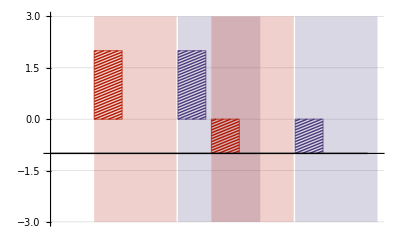

```mathematica
barFilled[gap_,h_,seg_][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{width,line,yt,yb,lend},{yb,yt}=Sort[{ymin,ymax}];
width=xmax-xmin;
line=Table[{{xmin,i},{xmax,i+width}},{i,yb,yt-width,h/seg}];
lend=line[[-1,1,2]];
line={Line[line],Line[Table[{{xmin+i,yb},{xmax,yb+width-i}},{i,h/seg,width,h/seg}]],Line[Table[{{xmin,lend+i},{xmax-(lend+width-yt)-i,yt}},{i,h/seg,width+h/seg,h/seg}]]};
{{Opacity[.2],EdgeForm[],Rectangle[{xmin,-h},{xmax+gap,h}]},{CapForm["Butt"],line},{FaceForm[],Rectangle[{xmin,ymin},{xmax,ymax}]}}]

BarChart[{{2,2},{-1,-1}},BarSpacing->2,ChartElementFunction->barFilled[.65,3,35],ChartStyle->61,GridLines->{None,Automatic}]
```

https://mathematica.stackexchange.com/questions/31221/how-do-i-plot-a-histogram-with-hatched-shading

Nearest::nearuf: The user-supplied distance function If[#2-#1>0,#2-#1,$MaxMachineNumber]& does not give a real numeric distance when applied to the point pair 2 Automatic and -23/5.

Nearest::near1: DistanceFunction→(If[#2-#1>0,#2-#1,$MaxMachineNumber]&) is neither a list of real points nor a valid list of rules.

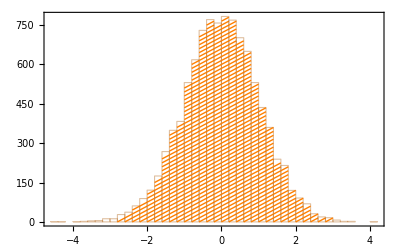

```mathematica
g[{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{yval,line},yval=Range[ymin,ymax,15];
line=Line/@Transpose@{Most@({xmin,#}&/@yval),Rest@({xmax,#}&/@yval)};
{FaceForm[White],Polygon[{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax}}],Orange,line}];
T=RandomVariate[NormalDistribution[0,1],10000];
Histogram[T,30,ChartElementFunction->g,ChartBaseStyle->EdgeForm[{Thin,Darker@Orange}],Frame->True]
```

Nearest::nearuf: The user-supplied distance function If[#2-#1>0,#2-#1,$MaxMachineNumber]& does not give a real numeric distance when applied to the point pair 2 Automatic and -4.

Nearest::near1: DistanceFunction→(If[#2-#1>0,#2-#1,$MaxMachineNumber]&) is neither a list of real points nor a valid list of rules.

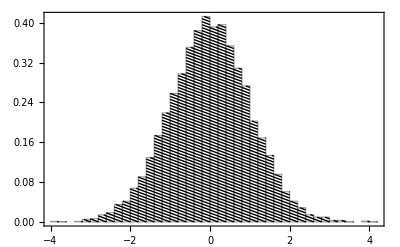

```mathematica
g[step_?NumberQ][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{yval,lines,xstart,xend},yval=Range[ymin,ymax,Abs[step]];
If[step>0,{xstart,xend}={xmin,xmax},{xstart,xend}={xmax,xmin}];
lines=Transpose@{{xstart,#}&/@Most[yval],{xend,#}&/@Rest[yval]};
lines=Join[lines,{{{xstart,Last@yval},{xstart+((xend-xstart) (ymax-Last@yval))/Abs[step],ymax}}}];
{FaceForm[None],Rectangle[{xmin,ymin},{xmax,ymax}],CapForm["Butt"],Line[lines]}];
data=RandomVariate[NormalDistribution[0,1],10000];
Histogram[data,30,"PDF",ChartElementFunction->g[-.006],ChartBaseStyle->{Directive[{EdgeForm[{Thin,Black}],Black}]},Frame->True]
```

## Figs...

```mathematica
words=
Select[
DeleteCases[
DeleteStopwords[Flatten[{StringSplit[#, " "]&/@ NetModel[]}]],
"Trained"|"Net"|"Data"|""|"Competition"|"Model"|"ImageNet"|"V17.06"|"(Raw"|"Model)"|"Image"|"Claims,"|"Clinical"|"Wolfram"
],
StringLength[#]>3&
]
```

{Face,Alignment,300W,Large,Pose,Face,Alignment,300W,Large,Pose,AdaIN-Style,MS-COCO,Painter,Numbers,Ademxapp,ADE20K,Ademxapp,Cityscapes,Ademxapp,PASCAL,VOC2012,MS-COCO,Ademxapp,Estimation,VGG-16,IMDB-WIKI,Looking,People,Estimation,VGG-16,IMDB-WIKI,BERT,BookCorpus,English,Wikipedia,BPEmb,Subword,Embeddings,Wikipedia,CapsNet,MNIST,Concept,Embeddings,Health,Insurance,Narratives,Stanford,PubMed,Journal,Articles,Colorful,Colorization,ColorNet,Colorization,ColorNet,Colorization,Places,ConceptNet,Numberbatch,Word,Vectors,ConceptNet,Numberbatch,Word,Vectors,CREPE,Pitch,Detection,Monophonic,Signal,CycleGAN,Apple-to-Orange,Translation,CycleGAN,Horse-to-Zebra,Translation,CycleGAN,Monet-to-Photo,Translation,CycleGAN,Orange-to-Apple,Translation,CycleGAN,Photo-to-Cezanne,Translation,CycleGAN,Photo-to-Monet,Translation,CycleGAN,Photo-to-Van,Gogh,Translation,CycleGAN,Summer-to-Winter,Translation,CycleGAN,Winter-to-Summer,Translation,CycleGAN,Zebra-to-Horse,Translation,Deep,Speech,Baidu,English,Dilated,ResNet-105,Cityscapes,Dilated,ResNet-22,Cityscapes,Dilated,ResNet-38,Cityscapes,ELMo,Contextual,Word,Representations,Word,Benchmark,Enhanced,Super-Resolution,DIV2K,,Flickr2K,Gender,Prediction,VGG-16,IMDB-WIKI,GloVe,100-Dimensional,Word,Vectors,Tweets,GloVe,100-Dimensional,Word,Vectors,Wikipedia,Gigaword,GloVe,200-Dimensional,Word,Vectors,Tweets,GloVe,25-Dimensional,Word,Vectors,Tweets,GloVe,300-Dimensional,Word,Vectors,Common,Crawl,GloVe,300-Dimensional,Word,Vectors,Common,Crawl,840B,GloVe,300-Dimensional,Word,Vectors,Wikipedia,Gigaword,GloVe,50-Dimensional,Word,Vectors,Tweets,GloVe,50-Dimensional,Word,Vectors,Wikipedia,Gigaword,GPT-2,Transformer,WebText,Transformer,BookCorpus,Inception,Extended,Salient,Object,Subitizing,Inception,Inception,Places365,Inception,LeNet,LeNet,MNIST,MobileNet,Multi-scale,Context,Aggregation,CamVid,Multi-scale,Context,Aggregation,Cityscapes,Multi-scale,Context,Aggregation,PASCAL,VOC2012,OpenFace,Face,Recognition,CASIA-WebFace,FaceScrub,Pix2pix,Photo-to-Street-Map,Translation,Pix2pix,Street-Map-to-Photo,Translation,ResNet-101,Augmented,CASIA-WebFace,ResNet-101,ResNet-101,YFCC100m,Geotagged,ResNet-152,ResNet-50,Self-Normalizing,Numeric,Sentiment,Language,Amazon,Product,Review,Single-Image,Depth,Perception,Depth,Wild,Single-Image,Depth,Perception,Depth,Depth,Wild,Single-Image,Depth,Perception,Depth,Squeeze-and-Excitation,SqueezeNet,V1.1,SSD-VGG-300,PASCAL,SSD-VGG-512,MS-COCO,SSD-VGG-512,PASCAL,VOC2007,,PASCAL,VOC2012,MS-COCO,U-Net,Glioblastoma-Astrocytoma,U373,Cells,Polyacrylamide,Substrate,Unguided,Volumetric,Regression,Face,Reconstruction,Vanilla,Facial,Landmark,Regression,Deep,Super-Resolution,VGG-16,VGG-19,VGGish,Feature,Extractor,YouTube,Wide,ResNet-50-2,AudioIdentify,AudioSet,Character-Level,Language,English,Character-Level,Language,ImageIdentify,JavaScript,Character-Level,Language,LaTeX,Character-Level,Language,Python,Character-Level,Language,Yahoo,Open,NSFW,YOLO,MS-COCO}

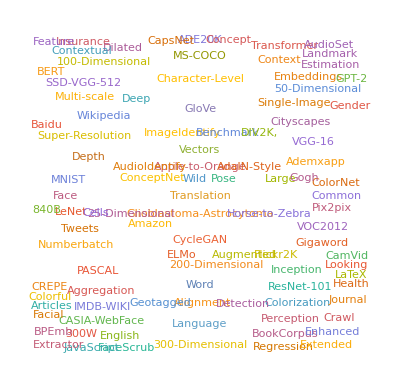

```mathematica
WordCloud[Counts[words]]
```